# Analysis of Thai Capital Market Linkage

#### Part I. Bivariate Copula Approach

Poomjai Nacaskul, Ph.D.

2023.02.23

## 1. Data, Stats & Fitted Univariate Distributions

Set Session

```mathematica
dateToday="2023.02.23";
OUTPUTDIR0=INPUTDIR0=NotebookDirectory[];
{EXPORTTABLES,EXPORTPICS,DEPLOYAPP}={False,False,False};
SeedRandom[RANDOMSEED0=1234];
```

Set Global Defaults

```mathematica
VERTEXSIZE0=.5;
LISTGRAPHLAYOUT0={Automatic,
"CircularEmbedding","DiscreteSpiralEmbedding","GridEmbedding",
"BalloonEmbedding",GRAPHLAYOUT0="RadialEmbedding","LayeredEmbedding",
"GravityEmbedding","HighDimensionalEmbedding","SpectralEmbedding",
"SphericalEmbedding","SpringEmbedding","SpringElectricalEmbedding"};
LISTIMAGESIZE0={Automatic,Small,IMAGESIZE0=Medium,Large};
LISTCENTRALITYMETHOD0={CENTRALITYMETHOD0="Betweenness","Katz[.1]","PageRank[.1]"};
LISTDIMREDUCT0={"Linear",DIMREDUCT0="TSNE","Autoencoder"};
```

Capital Market Data

```mathematica
dataThaiCapitalMktLink=Import[INPUTDIR0<>"(input)ThaiCapitalMktLink-TimeSeries.csv"];
```

```mathematica
𝒫𝒩Associate2Data[data_]:=AssociationThread[data[[1]]->Transpose@data[[2;;]]]
𝒫𝒩Associate2Stat[data_,stat_]:=stat/@𝒫𝒩Associate2Data[data]
𝒫𝒩Associate2Matrix[matrix_]:=Module[{dim=Dimensions[matrix]},
Association@Table[matrix[[i,1]]->Association@Table[matrix[[1,j]]->matrix[[i,j]],{j,2,dim[[2]]}],{i,2,dim[[1]]}]]
```

```mathematica
𝓍=𝒫𝒩Associate2Data[dataThaiCapitalMktLink];
varName=Keys@𝓍[[2;;]]
vertexLabel=Thread[Range[Length@varName]->varName]
vertexNumberLabel=Thread[Range[Length@varName]->(#[[1]]<>"|"<>#[[2]]&/@Transpose@{(ToString/@Range[Length@varName]),varName})]
listDistr=
{NormalDistribution,StudentTDistribution,
CauchyDistribution,LogisticDistribution,
LaplaceDistribution,GammaDistribution};
{minmax,mean,stdev,skewness,kurtosis,JarqueBera,ShapiroWilk,histogram,ℋ,𝒟}=
𝒫𝒩Associate2Stat[dataThaiCapitalMktLink[[All,2;;]],#]&/@{MinMax,
Mean,StandardDeviation,Skewness,Kurtosis,JarqueBeraALMTest,ShapiroWilkTest,
Histogram,HistogramDistribution,FindDistribution[#,TargetFunctions->listDistr]&};
```

{SET,MAI,ZeroShort,ZeroLong,CorpBond,THB,EquityFlow,BondFlow,EMAsiaEquity,SP500,EMBond,USBond,EMAsiaFX,USD}

{1→SET,2→MAI,3→ZeroShort,4→ZeroLong,5→CorpBond,6→THB,7→EquityFlow,8→BondFlow,9→EMAsiaEquity,10→SP500,11→EMBond,12→USBond,13→EMAsiaFX,14→USD}

{1→1|SET,2→2|MAI,3→3|ZeroShort,4→4|ZeroLong,5→5|CorpBond,6→6|THB,7→7|EquityFlow,8→8|BondFlow,9→9|EMAsiaEquity,10→10|SP500,11→11|EMBond,12→12|USBond,13→13|EMAsiaFX,14→14|USD}

```mathematica
tableBasicStat=
Grid[Prepend[Transpose@{Keys@𝒟,
Round[#,0.0001]&/@Values@mean,Round[#,0.001]&/@Values@stdev,
Round[#,0.001]&/@Values@skewness,Round[#,0.01]&/@Values@kurtosis,
Values@ShapiroWilk},
Style[#,Bold]&/@{"Series","Mean","StDev","Skewness","Kurtosis","Sharpiro-Wilk"}],
Alignment->Left,Frame->All]
```

Series | Mean | StDev | Skewness | Kurtosis | Sharpiro-Wilk
SET | 0.0367 | 1.059 | -0.923 | 14.91 | 7.48232×10^-43
MAI | 0.0368 | 1.102 | -1.07 | 11.51 | 3.26721×10^-43
ZeroShort | -0.0004 | 0.013 | -5.679 | 99.13 | 1.34446×10^-72
ZeroLong | -0.0003 | 0.027 | 0.652 | 13.96 | 3.07975×10^-50
CorpBond | -0.0001 | 0.011 | -0.008 | 19.58 | 1.67774×10^-58
THB | 0.0015 | 0.286 | -0.068 | 4.87 | 8.66112×10^-22
EquityFlow | -7.2057 | 66.876 | 0.584 | 16.92 | 1.94264×10^-41
BondFlow | 1082.91 | 4571.04 | 1.553 | 10.4 | 8.69989×10^-48
EMAsiaEquity | 0.0384 | 1.107 | -0.341 | 6.24 | 2.95441×10^-29
SP500 | 0.0483 | 1.125 | -0.692 | 16.76 | 2.13793×10^-46
EMBond | 0.0289 | 0.252 | -2.538 | 37.42 | 1.00693×10^-52
USBond | 0.0164 | 0.198 | -0.735 | 10.59 | 2.31124×10^-31
EMAsiaFX | 0.0005 | 0.234 | -0.219 | 5.74 | 1.12451×10^-23
USD | 0.0031 | 0.397 | 0.038 | 5.29 | 5.4775×10^-22

```mathematica
If[EXPORTTABLES,Export[OUTPUTDIR0<>"(table)BasicStat"<>#,tableBasicStat]&/@{".png",".pdf",".csv"}]
```

```mathematica
tableFittedDistr=
Grid[Prepend[Transpose@{Keys@𝒟,Values@𝒟},Style[#,Bold]&/@{"Series","Fitted Distribution"}],Alignment->{{Right,Left}},Frame->All]
```

Series | Fitted Distribution
SET | LaplaceDistribution[0.0367677,0.695446]
MAI | StudentTDistribution[0.134668,0.663328,2.90602]
ZeroShort | MixtureDistribution[{0.479098,0.520902},{CauchyDistribution[-0.0027739,0.00219492],CauchyDistribution[0.00238848,0.00207419]}]
ZeroLong | StudentTDistribution[-0.00295099,0.0127107,1.64441]
CorpBond | StudentTDistribution[-0.000985347,0.00612234,2.2003]
THB | LaplaceDistribution[0.00153022,0.210708]
EquityFlow | LaplaceDistribution[-7.20567,44.8822]
BondFlow | MixtureDistribution[{0.817365,0.182635},{LaplaceDistribution[-374.544,2000.03],GammaDistribution[2.62953,3461.55]}]
EMAsiaEquity | StudentTDistribution[0.0451953,0.758197,3.17598]
SP500 | LaplaceDistribution[0.0520962,0.726968]
EMBond | StudentTDistribution[0.0253962,0.140558,2.45137]
USBond | StudentTDistribution[0.0315655,0.141051,3.30262]
EMAsiaFX | LogisticDistribution[0.00297931,0.125365]
USD | LogisticDistribution[-0.0062515,0.224481]

```mathematica
If[EXPORTTABLES,Export[OUTPUTDIR0<>"(table)FittedDistr"<>#,tableFittedDistr]&/@{".png",".pdf",".csv"}]
```

Interactive Display

```mathematica
𝒫𝒩FittedUnivarDistr[series_:"SET",sizeImage_:Medium,sizeContent_:Automatic]:=
Manipulate[
Grid[
{{Plot[{PDF[𝒟[X],x],PDF[ℋ[X],x]},
{x,minmax[X][[1]],minmax[X][[2]]},
Filling->{1->{2}},
PlotRange->All,
ImageSize->sizeImage]},
{Grid[
{{"Mean",Round[mean[X],0.0001]},
{"StDev",Round[stdev[X],0.001]},
{"Skewness",Round[skewness[X],0.001]},
{"Kurtosis",Round[kurtosis[X],0.01]},
{"Sharpiro-Wilk",ShapiroWilk[X]},
{"fitted distribution",𝒟[X]}},
Alignment->{{Right,Left}},Frame->All]}}],
(*Style["Fitted Univariate Distribution",Bold,Large,RGBColor[0.25, 0.5, 0.75]],
Style["Poomjai Nacaskul, Ph.D.",Bold,Medium,RGBColor[0, 0, 0.75]],
Style["2021.02.12",Bold,Small,RGBColor[0.45, 0.3, 0.15]],
Delimiter,*)
{{X,series},Keys@𝒟},
ContentSize->sizeContent,
ControlPlacement->Right]
```

```mathematica
{𝒫𝒩FittedUnivarDistr[],𝒫𝒩FittedUnivarDistr["BondFlow",600,{600,Automatic}]}
```

{,}

```mathematica
If[EXPORTPICS,Timing[Export[OUTPUTDIR0<>"(figure)FittedUnivariateDistr-"<>#<>".png",𝒫𝒩FittedUnivarDistr[#,600,{600,Automatic}]]&/@varName]]
```

```mathematica
NotebookSave[];EmitSound[Sound[SoundNote["C",.5,"Violin"]]]
```

## 2. Pair-Plot (Lower-Triangle/Diagonal/Upper-Triangle)

L/D/U-Plot Template

```mathematica
𝒫𝒩PairOprnL[x_,OprnL_]:=
Table[
Table[OprnL[x[[i]],x[[j]]],{j,1,i-1}],
{i,2,Length@x}];
𝒫𝒩PairOprnLD[x_,OprnL_,OprnD_]:=
Table[
Join[Table[OprnL[x[[i]],x[[j]]],{j,1,i-1}],{OprnD[x[[i]]]}],
{i,1,Length@x}];
𝒫𝒩PairOprnLDU[x_,OprnL_,OprnD_,OprnU_]:=
Table[
Join[Table[OprnL[x[[i]],x[[j]]],{j,1,i-1}],{OprnD[x[[i]]]},Table[OprnU[x[[i]],x[[j]]],{j,i+1,Length@x}]],
{i,1,Length@x}];
𝒫𝒩Grid[table_,colheader_,rowheader_,title_:"",headerstyle_:{Large,Bold,RGBColor[0, 0, 1]}]:=
Grid[Prepend[Table[Prepend[table[[i]],Style[colheader[[i]],headerstyle]],{i,Length@table}],Style[#,headerstyle]&/@Prepend[rowheader,title]],Alignment->{Center,Center},ItemSize->All,Frame->All]
```

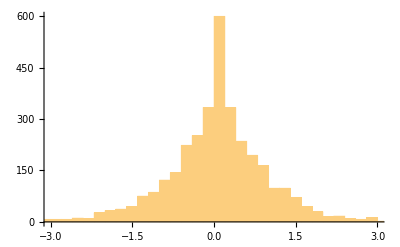
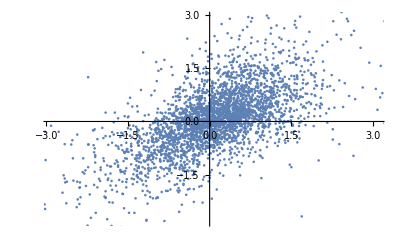
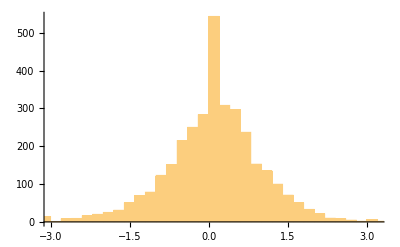
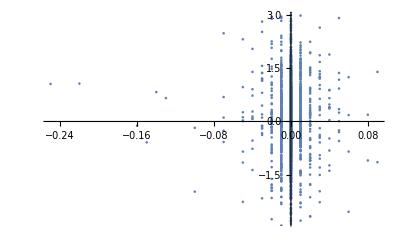
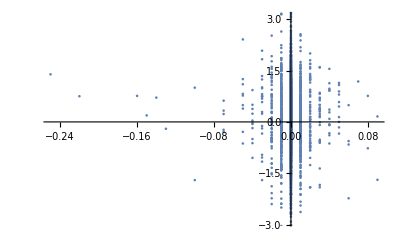
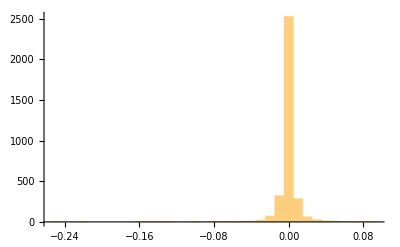
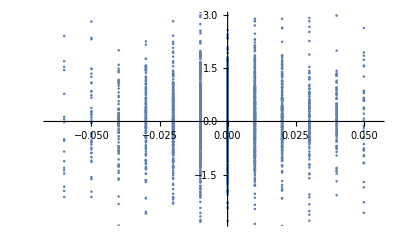
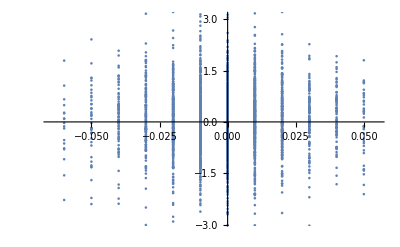
Pearson[U]
 Histogram[D]
Scatter[L] | SET | MAI | ZeroShort | ZeroLong | CorpBond | THB | EquityFlow | BondFlow | EMAsiaEquity | SP500 | EMBond | USBond | EMAsiaFX | USD
SET | -Graphics- | 0.692 | 0.036 | 0.029 | -0.021 | 0.244 | 0.272 | 0.063 | 0.564 | 0.249 | 0.357 | -0.014 | 0.238 | -0.11
MAI | -Graphics- | -Graphics- | 0.005 | -0.046 | 0.016 | 0.171 | 0.121 | 0.086 | 0.336 | 0.147 | 0.251 | 0.02 | 0.133 | -0.036
ZeroShort | -Graphics- | -Graphics- | -Graphics- | 0.335 | -0.102 | 0.029 | 0.05 | 0.012 | 0.016 | -0.009 | -0.024 | -0.037 | 0.007 | 0.
ZeroLong | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -0.565 | -0.092 | -0.006 | -0.099 | 0.006 | 0.029 | -0.144 | -0.156 | -0.058 | 0.051
CorpBond | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 0.043 | -0.02 | 0.036 | -0.003 | -0.021 | 0.048 | 0.052 | 0.013 | -0.006
THB | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 0.136 | 0.094 | 0.272 | 0.237 | 0.256 | 0.09 | 0.602 | -0.445
EquityFlow | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 0.17 | 0.235 | 0.041 | 0.197 | 0.047 | 0.062 | -0.025
BondFlow | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 0.1 | 0.021 | 0.131 | 0.04 | 0.037 | -0.035
EMAsiaEquity | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 0.323 | 0.424 | -0.017 | 0.4 | -0.182
SP500 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 0.249 | -0.224 | 0.487 | -0.342
EMBond | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 0.455 | 0.253 | -0.237
USBond | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -0.014 | -0.134
EMAsiaFX | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -0.67
USD | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
gridPearsonHistogramScatter=
𝒫𝒩Grid[
𝒫𝒩PairOprnLDU[
Values@𝓍[[2;;]],
ListPlot[Transpose[{#1,#2}]]&,Histogram,
Style[Round[Correlation[#1,#2],0.001],Large]&],
varName,varName,"  Pearson[U]\n Histogram[D]\nScatter[L]"]
```

```mathematica
If[EXPORTPICS,Timing[Export[OUTPUTDIR0<>"(figure)Scatter[L]-Histogram[D]-Pearson[U].png",gridPearsonHistogramScatter]]]
```

Mean/StDev/Pearson/Spearman/Kendall Stats

```mathematica
𝒫𝒩μσ[x_,rounding_:{0.001,0.001},style_:Large]:=
Grid[
{Style[#,style]&/@{"mean",Round[Mean[x],rounding[[1]]]},
Style[#,style]&/@{"stdev",Round[StandardDeviation[x],rounding[[2]]]}},
Alignment->Left]
𝒫𝒩ρρτ[x1_,x2_,rounding_:{0.001,0.001,0.001},style_:Large]:=
Grid[
{Style[#,style]&/@{"^Pearsonρ",Round[Correlation[x1,x2],rounding[[1]]]},
Style[#,style]&/@{"^Spearmanρ",Round[SpearmanRho[x1,x2],rounding[[2]]]},
Style[#,style]&/@{"^Kendallτ",Round[KendallTau[x1,x2],rounding[[3]]]}},
Alignment->Left]
```

```mathematica
gridPearsonSpearmanKendall=
𝒫𝒩Grid[
𝒫𝒩PairOprnL[Values@𝓍[[2;;]],𝒫𝒩ρρτ[#1[[2;;]],#2[[2;;]]]&],
varName[[2;;]],varName[[;;-2]],"{ρ,ρ,τ}[L]"]
```

{ρ,ρ,τ}[L] | SET | MAI | ZeroShort | ZeroLong | CorpBond | THB | EquityFlow | BondFlow | EMAsiaEquity | SP500 | EMBond | USBond | EMAsiaFX
MAI | ^Pearsonρ | 0.692
^Spearmanρ | 0.627
^Kendallτ | 0.46 |  |  |  |  |  |  |  |  |  |  |  | 
ZeroShort | ^Pearsonρ | 0.035
^Spearmanρ | 0.017
^Kendallτ | 0.014 | ^Pearsonρ | 0.005
^Spearmanρ | -0.007
^Kendallτ | -0.006 |  |  |  |  |  |  |  |  |  |  | 
ZeroLong | ^Pearsonρ | 0.03
^Spearmanρ | 0.026
^Kendallτ | 0.02 | ^Pearsonρ | -0.046
^Spearmanρ | -0.001
^Kendallτ | 0. | ^Pearsonρ | 0.338
^Spearmanρ | 0.296
^Kendallτ | 0.254 |  |  |  |  |  |  |  |  |  | 
CorpBond | ^Pearsonρ | -0.021
^Spearmanρ | -0.011
^Kendallτ | -0.009 | ^Pearsonρ | 0.016
^Spearmanρ | -0.001
^Kendallτ | -0.002 | ^Pearsonρ | -0.102
^Spearmanρ | -0.113
^Kendallτ | -0.102 | ^Pearsonρ | -0.565
^Spearmanρ | -0.521
^Kendallτ | -0.455 |  |  |  |  |  |  |  |  | 
THB | ^Pearsonρ | 0.244
^Spearmanρ | 0.219
^Kendallτ | 0.15 | ^Pearsonρ | 0.171
^Spearmanρ | 0.145
^Kendallτ | 0.098 | ^Pearsonρ | 0.029
^Spearmanρ | 0.001
^Kendallτ | 0. | ^Pearsonρ | -0.092
^Spearmanρ | -0.088
^Kendallτ | -0.065 | ^Pearsonρ | 0.043
^Spearmanρ | 0.053
^Kendallτ | 0.041 |  |  |  |  |  |  |  | 
EquityFlow | ^Pearsonρ | 0.272
^Spearmanρ | 0.299
^Kendallτ | 0.208 | ^Pearsonρ | 0.121
^Spearmanρ | 0.142
^Kendallτ | 0.097 | ^Pearsonρ | 0.05
^Spearmanρ | 0.029
^Kendallτ | 0.023 | ^Pearsonρ | -0.006
^Spearmanρ | -0.02
^Kendallτ | -0.015 | ^Pearsonρ | -0.02
^Spearmanρ | -0.023
^Kendallτ | -0.018 | ^Pearsonρ | 0.136
^Spearmanρ | 0.117
^Kendallτ | 0.08 |  |  |  |  |  |  | 
BondFlow | ^Pearsonρ | 0.063
^Spearmanρ | 0.054
^Kendallτ | 0.036 | ^Pearsonρ | 0.086
^Spearmanρ | 0.079
^Kendallτ | 0.054 | ^Pearsonρ | 0.012
^Spearmanρ | -0.01
^Kendallτ | -0.008 | ^Pearsonρ | -0.099
^Spearmanρ | -0.1
^Kendallτ | -0.072 | ^Pearsonρ | 0.036
^Spearmanρ | 0.055
^Kendallτ | 0.042 | ^Pearsonρ | 0.094
^Spearmanρ | 0.073
^Kendallτ | 0.049 | ^Pearsonρ | 0.17
^Spearmanρ | 0.147
^Kendallτ | 0.101 |  |  |  |  |  | 
EMAsiaEquity | ^Pearsonρ | 0.564
^Spearmanρ | 0.508
^Kendallτ | 0.361 | ^Pearsonρ | 0.336
^Spearmanρ | 0.284
^Kendallτ | 0.194 | ^Pearsonρ | 0.017
^Spearmanρ | -0.005
^Kendallτ | -0.004 | ^Pearsonρ | 0.006
^Spearmanρ | 0.028
^Kendallτ | 0.021 | ^Pearsonρ | -0.003
^Spearmanρ | -0.019
^Kendallτ | -0.015 | ^Pearsonρ | 0.272
^Spearmanρ | 0.274
^Kendallτ | 0.188 | ^Pearsonρ | 0.235
^Spearmanρ | 0.258
^Kendallτ | 0.175 | ^Pearsonρ | 0.1
^Spearmanρ | 0.073
^Kendallτ | 0.049 |  |  |  |  | 
SP500 | ^Pearsonρ | 0.249
^Spearmanρ | 0.189
^Kendallτ | 0.132 | ^Pearsonρ | 0.147
^Spearmanρ | 0.117
^Kendallτ | 0.08 | ^Pearsonρ | -0.009
^Spearmanρ | 0.008
^Kendallτ | 0.006 | ^Pearsonρ | 0.028
^Spearmanρ | 0.033
^Kendallτ | 0.024 | ^Pearsonρ | -0.021
^Spearmanρ | -0.043
^Kendallτ | -0.033 | ^Pearsonρ | 0.237
^Spearmanρ | 0.221
^Kendallτ | 0.151 | ^Pearsonρ | 0.041
^Spearmanρ | 0.028
^Kendallτ | 0.019 | ^Pearsonρ | 0.021
^Spearmanρ | 0.013
^Kendallτ | 0.008 | ^Pearsonρ | 0.323
^Spearmanρ | 0.256
^Kendallτ | 0.179 |  |  |  | 
EMBond | ^Pearsonρ | 0.358
^Spearmanρ | 0.248
^Kendallτ | 0.172 | ^Pearsonρ | 0.251
^Spearmanρ | 0.159
^Kendallτ | 0.109 | ^Pearsonρ | -0.022
^Spearmanρ | -0.015
^Kendallτ | -0.012 | ^Pearsonρ | -0.146
^Spearmanρ | -0.107
^Kendallτ | -0.079 | ^Pearsonρ | 0.048
^Spearmanρ | 0.024
^Kendallτ | 0.018 | ^Pearsonρ | 0.257
^Spearmanρ | 0.229
^Kendallτ | 0.158 | ^Pearsonρ | 0.196
^Spearmanρ | 0.205
^Kendallτ | 0.14 | ^Pearsonρ | 0.131
^Spearmanρ | 0.111
^Kendallτ | 0.075 | ^Pearsonρ | 0.424
^Spearmanρ | 0.366
^Kendallτ | 0.255 | ^Pearsonρ | 0.249
^Spearmanρ | 0.143
^Kendallτ | 0.098 |  |  | 
USBond | ^Pearsonρ | -0.013
^Spearmanρ | -0.029
^Kendallτ | -0.02 | ^Pearsonρ | 0.02
^Spearmanρ | 0.003
^Kendallτ | 0.002 | ^Pearsonρ | -0.035
^Spearmanρ | -0.029
^Kendallτ | -0.023 | ^Pearsonρ | -0.158
^Spearmanρ | -0.116
^Kendallτ | -0.085 | ^Pearsonρ | 0.052
^Spearmanρ | 0.06
^Kendallτ | 0.047 | ^Pearsonρ | 0.09
^Spearmanρ | 0.064
^Kendallτ | 0.044 | ^Pearsonρ | 0.047
^Spearmanρ | 0.046
^Kendallτ | 0.031 | ^Pearsonρ | 0.04
^Spearmanρ | 0.022
^Kendallτ | 0.014 | ^Pearsonρ | -0.017
^Spearmanρ | -0.037
^Kendallτ | -0.026 | ^Pearsonρ | -0.224
^Spearmanρ | -0.269
^Kendallτ | -0.189 | ^Pearsonρ | 0.454
^Spearmanρ | 0.439
^Kendallτ | 0.319 |  | 
EMAsiaFX | ^Pearsonρ | 0.239
^Spearmanρ | 0.206
^Kendallτ | 0.141 | ^Pearsonρ | 0.133
^Spearmanρ | 0.11
^Kendallτ | 0.075 | ^Pearsonρ | 0.009
^Spearmanρ | 0.019
^Kendallτ | 0.016 | ^Pearsonρ | -0.059
^Spearmanρ | -0.023
^Kendallτ | -0.017 | ^Pearsonρ | 0.013
^Spearmanρ | 0.007
^Kendallτ | 0.006 | ^Pearsonρ | 0.602
^Spearmanρ | 0.617
^Kendallτ | 0.448 | ^Pearsonρ | 0.062
^Spearmanρ | 0.056
^Kendallτ | 0.038 | ^Pearsonρ | 0.037
^Spearmanρ | 0.03
^Kendallτ | 0.02 | ^Pearsonρ | 0.4
^Spearmanρ | 0.364
^Kendallτ | 0.255 | ^Pearsonρ | 0.487
^Spearmanρ | 0.416
^Kendallτ | 0.294 | ^Pearsonρ | 0.252
^Spearmanρ | 0.216
^Kendallτ | 0.151 | ^Pearsonρ | -0.015
^Spearmanρ | -0.035
^Kendallτ | -0.024 | 
USD | ^Pearsonρ | -0.111
^Spearmanρ | -0.092
^Kendallτ | -0.063 | ^Pearsonρ | -0.036
^Spearmanρ | -0.044
^Kendallτ | -0.03 | ^Pearsonρ | -0.001
^Spearmanρ | -0.01
^Kendallτ | -0.008 | ^Pearsonρ | 0.051
^Spearmanρ | 0.029
^Kendallτ | 0.021 | ^Pearsonρ | -0.006
^Spearmanρ | -0.01
^Kendallτ | -0.008 | ^Pearsonρ | -0.445
^Spearmanρ | -0.466
^Kendallτ | -0.327 | ^Pearsonρ | -0.025
^Spearmanρ | -0.019
^Kendallτ | -0.013 | ^Pearsonρ | -0.035
^Spearmanρ | -0.02
^Kendallτ | -0.013 | ^Pearsonρ | -0.182
^Spearmanρ | -0.15
^Kendallτ | -0.102 | ^Pearsonρ | -0.342
^Spearmanρ | -0.304
^Kendallτ | -0.212 | ^Pearsonρ | -0.236
^Spearmanρ | -0.205
^Kendallτ | -0.143 | ^Pearsonρ | -0.134
^Spearmanρ | -0.083
^Kendallτ | -0.058 | ^Pearsonρ | -0.67
^Spearmanρ | -0.661
^Kendallτ | -0.486

```mathematica
If[EXPORTPICS,Export[OUTPUTDIR0<>"(table)Pearson,Spearman,Kendall[L].png",gridPearsonSpearmanKendall]]
```

```mathematica
gridPearsonSpearmanKendallMuSigma=
𝒫𝒩Grid[
𝒫𝒩PairOprnLD[Values@𝓍[[2;;]],𝒫𝒩ρρτ[#1[[2;;]],#2[[2;;]]]&,𝒫𝒩μσ[#]&],
varName,varName," {μ,σ}[D]\n{ρ,ρ,τ}[L]"]
```

{μ,σ}[D]
{ρ,ρ,τ}[L] | SET | MAI | ZeroShort | ZeroLong | CorpBond | THB | EquityFlow | BondFlow | EMAsiaEquity | SP500 | EMBond | USBond | EMAsiaFX | USD
SET | mean | 0.037
stdev | 1.059 |  |  |  |  |  |  |  |  |  |  |  |  | 
MAI | ^Pearsonρ | 0.692
^Spearmanρ | 0.627
^Kendallτ | 0.46 | mean | 0.037
stdev | 1.102 |  |  |  |  |  |  |  |  |  |  |  | 
ZeroShort | ^Pearsonρ | 0.035
^Spearmanρ | 0.017
^Kendallτ | 0.014 | ^Pearsonρ | 0.005
^Spearmanρ | -0.007
^Kendallτ | -0.006 | mean | 0.
stdev | 0.013 |  |  |  |  |  |  |  |  |  |  | 
ZeroLong | ^Pearsonρ | 0.03
^Spearmanρ | 0.026
^Kendallτ | 0.02 | ^Pearsonρ | -0.046
^Spearmanρ | -0.001
^Kendallτ | 0. | ^Pearsonρ | 0.338
^Spearmanρ | 0.296
^Kendallτ | 0.254 | mean | 0.
stdev | 0.027 |  |  |  |  |  |  |  |  |  | 
CorpBond | ^Pearsonρ | -0.021
^Spearmanρ | -0.011
^Kendallτ | -0.009 | ^Pearsonρ | 0.016
^Spearmanρ | -0.001
^Kendallτ | -0.002 | ^Pearsonρ | -0.102
^Spearmanρ | -0.113
^Kendallτ | -0.102 | ^Pearsonρ | -0.565
^Spearmanρ | -0.521
^Kendallτ | -0.455 | mean | 0.
stdev | 0.011 |  |  |  |  |  |  |  |  | 
THB | ^Pearsonρ | 0.244
^Spearmanρ | 0.219
^Kendallτ | 0.15 | ^Pearsonρ | 0.171
^Spearmanρ | 0.145
^Kendallτ | 0.098 | ^Pearsonρ | 0.029
^Spearmanρ | 0.001
^Kendallτ | 0. | ^Pearsonρ | -0.092
^Spearmanρ | -0.088
^Kendallτ | -0.065 | ^Pearsonρ | 0.043
^Spearmanρ | 0.053
^Kendallτ | 0.041 | mean | 0.001
stdev | 0.286 |  |  |  |  |  |  |  | 
EquityFlow | ^Pearsonρ | 0.272
^Spearmanρ | 0.299
^Kendallτ | 0.208 | ^Pearsonρ | 0.121
^Spearmanρ | 0.142
^Kendallτ | 0.097 | ^Pearsonρ | 0.05
^Spearmanρ | 0.029
^Kendallτ | 0.023 | ^Pearsonρ | -0.006
^Spearmanρ | -0.02
^Kendallτ | -0.015 | ^Pearsonρ | -0.02
^Spearmanρ | -0.023
^Kendallτ | -0.018 | ^Pearsonρ | 0.136
^Spearmanρ | 0.117
^Kendallτ | 0.08 | mean | -7.206
stdev | 66.876 |  |  |  |  |  |  | 
BondFlow | ^Pearsonρ | 0.063
^Spearmanρ | 0.054
^Kendallτ | 0.036 | ^Pearsonρ | 0.086
^Spearmanρ | 0.079
^Kendallτ | 0.054 | ^Pearsonρ | 0.012
^Spearmanρ | -0.01
^Kendallτ | -0.008 | ^Pearsonρ | -0.099
^Spearmanρ | -0.1
^Kendallτ | -0.072 | ^Pearsonρ | 0.036
^Spearmanρ | 0.055
^Kendallτ | 0.042 | ^Pearsonρ | 0.094
^Spearmanρ | 0.073
^Kendallτ | 0.049 | ^Pearsonρ | 0.17
^Spearmanρ | 0.147
^Kendallτ | 0.101 | mean | 1082.91
stdev | 4571.04 |  |  |  |  |  | 
EMAsiaEquity | ^Pearsonρ | 0.564
^Spearmanρ | 0.508
^Kendallτ | 0.361 | ^Pearsonρ | 0.336
^Spearmanρ | 0.284
^Kendallτ | 0.194 | ^Pearsonρ | 0.017
^Spearmanρ | -0.005
^Kendallτ | -0.004 | ^Pearsonρ | 0.006
^Spearmanρ | 0.028
^Kendallτ | 0.021 | ^Pearsonρ | -0.003
^Spearmanρ | -0.019
^Kendallτ | -0.015 | ^Pearsonρ | 0.272
^Spearmanρ | 0.274
^Kendallτ | 0.188 | ^Pearsonρ | 0.235
^Spearmanρ | 0.258
^Kendallτ | 0.175 | ^Pearsonρ | 0.1
^Spearmanρ | 0.073
^Kendallτ | 0.049 | mean | 0.038
stdev | 1.107 |  |  |  |  | 
SP500 | ^Pearsonρ | 0.249
^Spearmanρ | 0.189
^Kendallτ | 0.132 | ^Pearsonρ | 0.147
^Spearmanρ | 0.117
^Kendallτ | 0.08 | ^Pearsonρ | -0.009
^Spearmanρ | 0.008
^Kendallτ | 0.006 | ^Pearsonρ | 0.028
^Spearmanρ | 0.033
^Kendallτ | 0.024 | ^Pearsonρ | -0.021
^Spearmanρ | -0.043
^Kendallτ | -0.033 | ^Pearsonρ | 0.237
^Spearmanρ | 0.221
^Kendallτ | 0.151 | ^Pearsonρ | 0.041
^Spearmanρ | 0.028
^Kendallτ | 0.019 | ^Pearsonρ | 0.021
^Spearmanρ | 0.013
^Kendallτ | 0.008 | ^Pearsonρ | 0.323
^Spearmanρ | 0.256
^Kendallτ | 0.179 | mean | 0.048
stdev | 1.125 |  |  |  | 
EMBond | ^Pearsonρ | 0.358
^Spearmanρ | 0.248
^Kendallτ | 0.172 | ^Pearsonρ | 0.251
^Spearmanρ | 0.159
^Kendallτ | 0.109 | ^Pearsonρ | -0.022
^Spearmanρ | -0.015
^Kendallτ | -0.012 | ^Pearsonρ | -0.146
^Spearmanρ | -0.107
^Kendallτ | -0.079 | ^Pearsonρ | 0.048
^Spearmanρ | 0.024
^Kendallτ | 0.018 | ^Pearsonρ | 0.257
^Spearmanρ | 0.229
^Kendallτ | 0.158 | ^Pearsonρ | 0.196
^Spearmanρ | 0.205
^Kendallτ | 0.14 | ^Pearsonρ | 0.131
^Spearmanρ | 0.111
^Kendallτ | 0.075 | ^Pearsonρ | 0.424
^Spearmanρ | 0.366
^Kendallτ | 0.255 | ^Pearsonρ | 0.249
^Spearmanρ | 0.143
^Kendallτ | 0.098 | mean | 0.029
stdev | 0.252 |  |  | 
USBond | ^Pearsonρ | -0.013
^Spearmanρ | -0.029
^Kendallτ | -0.02 | ^Pearsonρ | 0.02
^Spearmanρ | 0.003
^Kendallτ | 0.002 | ^Pearsonρ | -0.035
^Spearmanρ | -0.029
^Kendallτ | -0.023 | ^Pearsonρ | -0.158
^Spearmanρ | -0.116
^Kendallτ | -0.085 | ^Pearsonρ | 0.052
^Spearmanρ | 0.06
^Kendallτ | 0.047 | ^Pearsonρ | 0.09
^Spearmanρ | 0.064
^Kendallτ | 0.044 | ^Pearsonρ | 0.047
^Spearmanρ | 0.046
^Kendallτ | 0.031 | ^Pearsonρ | 0.04
^Spearmanρ | 0.022
^Kendallτ | 0.014 | ^Pearsonρ | -0.017
^Spearmanρ | -0.037
^Kendallτ | -0.026 | ^Pearsonρ | -0.224
^Spearmanρ | -0.269
^Kendallτ | -0.189 | ^Pearsonρ | 0.454
^Spearmanρ | 0.439
^Kendallτ | 0.319 | mean | 0.016
stdev | 0.198 |  | 
EMAsiaFX | ^Pearsonρ | 0.239
^Spearmanρ | 0.206
^Kendallτ | 0.141 | ^Pearsonρ | 0.133
^Spearmanρ | 0.11
^Kendallτ | 0.075 | ^Pearsonρ | 0.009
^Spearmanρ | 0.019
^Kendallτ | 0.016 | ^Pearsonρ | -0.059
^Spearmanρ | -0.023
^Kendallτ | -0.017 | ^Pearsonρ | 0.013
^Spearmanρ | 0.007
^Kendallτ | 0.006 | ^Pearsonρ | 0.602
^Spearmanρ | 0.617
^Kendallτ | 0.448 | ^Pearsonρ | 0.062
^Spearmanρ | 0.056
^Kendallτ | 0.038 | ^Pearsonρ | 0.037
^Spearmanρ | 0.03
^Kendallτ | 0.02 | ^Pearsonρ | 0.4
^Spearmanρ | 0.364
^Kendallτ | 0.255 | ^Pearsonρ | 0.487
^Spearmanρ | 0.416
^Kendallτ | 0.294 | ^Pearsonρ | 0.252
^Spearmanρ | 0.216
^Kendallτ | 0.151 | ^Pearsonρ | -0.015
^Spearmanρ | -0.035
^Kendallτ | -0.024 | mean | 0.
stdev | 0.234 | 
USD | ^Pearsonρ | -0.111
^Spearmanρ | -0.092
^Kendallτ | -0.063 | ^Pearsonρ | -0.036
^Spearmanρ | -0.044
^Kendallτ | -0.03 | ^Pearsonρ | -0.001
^Spearmanρ | -0.01
^Kendallτ | -0.008 | ^Pearsonρ | 0.051
^Spearmanρ | 0.029
^Kendallτ | 0.021 | ^Pearsonρ | -0.006
^Spearmanρ | -0.01
^Kendallτ | -0.008 | ^Pearsonρ | -0.445
^Spearmanρ | -0.466
^Kendallτ | -0.327 | ^Pearsonρ | -0.025
^Spearmanρ | -0.019
^Kendallτ | -0.013 | ^Pearsonρ | -0.035
^Spearmanρ | -0.02
^Kendallτ | -0.013 | ^Pearsonρ | -0.182
^Spearmanρ | -0.15
^Kendallτ | -0.102 | ^Pearsonρ | -0.342
^Spearmanρ | -0.304
^Kendallτ | -0.212 | ^Pearsonρ | -0.236
^Spearmanρ | -0.205
^Kendallτ | -0.143 | ^Pearsonρ | -0.134
^Spearmanρ | -0.083
^Kendallτ | -0.058 | ^Pearsonρ | -0.67
^Spearmanρ | -0.661
^Kendallτ | -0.486 | mean | 0.003
stdev | 0.397

```mathematica
If[EXPORTPICS,Export[OUTPUTDIR0<>"(table)Pearson,Spearman,Kendall[L]-Mu,Sigma[D].png",gridPearsonSpearmanKendallMuSigma]]
```

```mathematica
gridScatterHistogramPearsonSpearmanKendall=
𝒫𝒩Grid[
𝒫𝒩PairOprnLDU[Values@𝓍[[2;;]],ListPlot[Transpose[{#1,#2}]]&,Histogram,𝒫𝒩ρρτ],
varName,varName,"  ρ|ρ|τ[U]\n Histogram[D]\nScatter[L]"]
```

ρ|ρ|τ[U]
 Histogram[D]
Scatter[L] | SET | MAI | ZeroShort | ZeroLong | CorpBond | THB | EquityFlow | BondFlow | EMAsiaEquity | SP500 | EMBond | USBond | EMAsiaFX | USD
SET | -Graphics- | ^Pearsonρ | 0.692
^Spearmanρ | 0.626
^Kendallτ | 0.459 | ^Pearsonρ | 0.036
^Spearmanρ | 0.018
^Kendallτ | 0.014 | ^Pearsonρ | 0.029
^Spearmanρ | 0.026
^Kendallτ | 0.019 | ^Pearsonρ | -0.021
^Spearmanρ | -0.011
^Kendallτ | -0.009 | ^Pearsonρ | 0.244
^Spearmanρ | 0.219
^Kendallτ | 0.15 | ^Pearsonρ | 0.272
^Spearmanρ | 0.298
^Kendallτ | 0.208 | ^Pearsonρ | 0.063
^Spearmanρ | 0.054
^Kendallτ | 0.036 | ^Pearsonρ | 0.564
^Spearmanρ | 0.508
^Kendallτ | 0.361 | ^Pearsonρ | 0.249
^Spearmanρ | 0.188
^Kendallτ | 0.131 | ^Pearsonρ | 0.357
^Spearmanρ | 0.247
^Kendallτ | 0.171 | ^Pearsonρ | -0.014
^Spearmanρ | -0.029
^Kendallτ | -0.02 | ^Pearsonρ | 0.238
^Spearmanρ | 0.205
^Kendallτ | 0.141 | ^Pearsonρ | -0.11
^Spearmanρ | -0.092
^Kendallτ | -0.063
MAI | -Graphics- | -Graphics- | ^Pearsonρ | 0.005
^Spearmanρ | -0.008
^Kendallτ | -0.006 | ^Pearsonρ | -0.046
^Spearmanρ | 0.
^Kendallτ | 0. | ^Pearsonρ | 0.016
^Spearmanρ | -0.001
^Kendallτ | -0.002 | ^Pearsonρ | 0.171
^Spearmanρ | 0.144
^Kendallτ | 0.098 | ^Pearsonρ | 0.121
^Spearmanρ | 0.142
^Kendallτ | 0.097 | ^Pearsonρ | 0.086
^Spearmanρ | 0.079
^Kendallτ | 0.054 | ^Pearsonρ | 0.336
^Spearmanρ | 0.284
^Kendallτ | 0.194 | ^Pearsonρ | 0.147
^Spearmanρ | 0.118
^Kendallτ | 0.08 | ^Pearsonρ | 0.251
^Spearmanρ | 0.159
^Kendallτ | 0.109 | ^Pearsonρ | 0.02
^Spearmanρ | 0.003
^Kendallτ | 0.002 | ^Pearsonρ | 0.133
^Spearmanρ | 0.11
^Kendallτ | 0.075 | ^Pearsonρ | -0.036
^Spearmanρ | -0.045
^Kendallτ | -0.03
ZeroShort | -Graphics- | -Graphics- | -Graphics- | ^Pearsonρ | 0.335
^Spearmanρ | 0.295
^Kendallτ | 0.253 | ^Pearsonρ | -0.102
^Spearmanρ | -0.113
^Kendallτ | -0.102 | ^Pearsonρ | 0.029
^Spearmanρ | 0.001
^Kendallτ | 0.001 | ^Pearsonρ | 0.05
^Spearmanρ | 0.029
^Kendallτ | 0.023 | ^Pearsonρ | 0.012
^Spearmanρ | -0.01
^Kendallτ | -0.008 | ^Pearsonρ | 0.016
^Spearmanρ | -0.005
^Kendallτ | -0.004 | ^Pearsonρ | -0.009
^Spearmanρ | 0.007
^Kendallτ | 0.006 | ^Pearsonρ | -0.024
^Spearmanρ | -0.016
^Kendallτ | -0.013 | ^Pearsonρ | -0.037
^Spearmanρ | -0.03
^Kendallτ | -0.024 | ^Pearsonρ | 0.007
^Spearmanρ | 0.018
^Kendallτ | 0.015 | ^Pearsonρ | 0.
^Spearmanρ | -0.01
^Kendallτ | -0.008
ZeroLong | -Graphics- | -Graphics- | -Graphics- | -Graphics- | ^Pearsonρ | -0.565
^Spearmanρ | -0.521
^Kendallτ | -0.455 | ^Pearsonρ | -0.092
^Spearmanρ | -0.089
^Kendallτ | -0.065 | ^Pearsonρ | -0.006
^Spearmanρ | -0.019
^Kendallτ | -0.015 | ^Pearsonρ | -0.099
^Spearmanρ | -0.099
^Kendallτ | -0.072 | ^Pearsonρ | 0.006
^Spearmanρ | 0.028
^Kendallτ | 0.021 | ^Pearsonρ | 0.029
^Spearmanρ | 0.034
^Kendallτ | 0.025 | ^Pearsonρ | -0.144
^Spearmanρ | -0.106
^Kendallτ | -0.078 | ^Pearsonρ | -0.156
^Spearmanρ | -0.115
^Kendallτ | -0.085 | ^Pearsonρ | -0.058
^Spearmanρ | -0.022
^Kendallτ | -0.016 | ^Pearsonρ | 0.051
^Spearmanρ | 0.029
^Kendallτ | 0.021
CorpBond | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | ^Pearsonρ | 0.043
^Spearmanρ | 0.053
^Kendallτ | 0.041 | ^Pearsonρ | -0.02
^Spearmanρ | -0.023
^Kendallτ | -0.018 | ^Pearsonρ | 0.036
^Spearmanρ | 0.055
^Kendallτ | 0.042 | ^Pearsonρ | -0.003
^Spearmanρ | -0.019
^Kendallτ | -0.015 | ^Pearsonρ | -0.021
^Spearmanρ | -0.043
^Kendallτ | -0.033 | ^Pearsonρ | 0.048
^Spearmanρ | 0.024
^Kendallτ | 0.018 | ^Pearsonρ | 0.052
^Spearmanρ | 0.06
^Kendallτ | 0.047 | ^Pearsonρ | 0.013
^Spearmanρ | 0.007
^Kendallτ | 0.006 | ^Pearsonρ | -0.006
^Spearmanρ | -0.01
^Kendallτ | -0.008
THB | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | ^Pearsonρ | 0.136
^Spearmanρ | 0.117
^Kendallτ | 0.08 | ^Pearsonρ | 0.094
^Spearmanρ | 0.073
^Kendallτ | 0.049 | ^Pearsonρ | 0.272
^Spearmanρ | 0.273
^Kendallτ | 0.187 | ^Pearsonρ | 0.237
^Spearmanρ | 0.221
^Kendallτ | 0.151 | ^Pearsonρ | 0.256
^Spearmanρ | 0.229
^Kendallτ | 0.157 | ^Pearsonρ | 0.09
^Spearmanρ | 0.064
^Kendallτ | 0.044 | ^Pearsonρ | 0.602
^Spearmanρ | 0.616
^Kendallτ | 0.448 | ^Pearsonρ | -0.445
^Spearmanρ | -0.466
^Kendallτ | -0.327
EquityFlow | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | ^Pearsonρ | 0.17
^Spearmanρ | 0.147
^Kendallτ | 0.101 | ^Pearsonρ | 0.235
^Spearmanρ | 0.259
^Kendallτ | 0.175 | ^Pearsonρ | 0.041
^Spearmanρ | 0.029
^Kendallτ | 0.019 | ^Pearsonρ | 0.197
^Spearmanρ | 0.205
^Kendallτ | 0.141 | ^Pearsonρ | 0.047
^Spearmanρ | 0.046
^Kendallτ | 0.031 | ^Pearsonρ | 0.062
^Spearmanρ | 0.056
^Kendallτ | 0.038 | ^Pearsonρ | -0.025
^Spearmanρ | -0.019
^Kendallτ | -0.013
BondFlow | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | ^Pearsonρ | 0.1
^Spearmanρ | 0.073
^Kendallτ | 0.049 | ^Pearsonρ | 0.021
^Spearmanρ | 0.013
^Kendallτ | 0.008 | ^Pearsonρ | 0.131
^Spearmanρ | 0.11
^Kendallτ | 0.075 | ^Pearsonρ | 0.04
^Spearmanρ | 0.022
^Kendallτ | 0.014 | ^Pearsonρ | 0.037
^Spearmanρ | 0.03
^Kendallτ | 0.02 | ^Pearsonρ | -0.035
^Spearmanρ | -0.02
^Kendallτ | -0.013
EMAsiaEquity | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | ^Pearsonρ | 0.323
^Spearmanρ | 0.256
^Kendallτ | 0.179 | ^Pearsonρ | 0.424
^Spearmanρ | 0.366
^Kendallτ | 0.255 | ^Pearsonρ | -0.017
^Spearmanρ | -0.037
^Kendallτ | -0.026 | ^Pearsonρ | 0.4
^Spearmanρ | 0.364
^Kendallτ | 0.255 | ^Pearsonρ | -0.182
^Spearmanρ | -0.15
^Kendallτ | -0.102
SP500 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | ^Pearsonρ | 0.249
^Spearmanρ | 0.143
^Kendallτ | 0.099 | ^Pearsonρ | -0.224
^Spearmanρ | -0.268
^Kendallτ | -0.189 | ^Pearsonρ | 0.487
^Spearmanρ | 0.416
^Kendallτ | 0.294 | ^Pearsonρ | -0.342
^Spearmanρ | -0.304
^Kendallτ | -0.212
EMBond | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | ^Pearsonρ | 0.455
^Spearmanρ | 0.439
^Kendallτ | 0.319 | ^Pearsonρ | 0.253
^Spearmanρ | 0.217
^Kendallτ | 0.151 | ^Pearsonρ | -0.237
^Spearmanρ | -0.205
^Kendallτ | -0.143
USBond | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | ^Pearsonρ | -0.014
^Spearmanρ | -0.034
^Kendallτ | -0.024 | ^Pearsonρ | -0.134
^Spearmanρ | -0.083
^Kendallτ | -0.058
EMAsiaFX | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | ^Pearsonρ | -0.67
^Spearmanρ | -0.661
^Kendallτ | -0.486
USD | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
If[EXPORTPICS,Timing[Export[OUTPUTDIR0<>"(figure)Scatter[L]-Histogram[D]-Pearson,Spearman,Kendall[U].png",gridScatterHistogramPearsonSpearmanKendall]]]
```

Various [L] Plots

```mathematica
(* Pearson's Rho (1D-lagged row variables VERSUS column variables) *)
𝒫𝒩Grid[𝒫𝒩PairOprnL[Values@𝓍[[2;;]],Round[Correlation[#1[[;;-2]],#2[[2;;]]],0.001]&],varName[[2;;]],varName[[;;-2]],"(row-1D-lagged)^Pearsonρ"]
```

(row-1D-lagged)^Pearsonρ | SET | MAI | ZeroShort | ZeroLong | CorpBond | THB | EquityFlow | BondFlow | EMAsiaEquity | SP500 | EMBond | USBond | EMAsiaFX
MAI | -0.03 |  |  |  |  |  |  |  |  |  |  |  | 
ZeroShort | -0.018 | -0.011 |  |  |  |  |  |  |  |  |  |  | 
ZeroLong | -0.017 | -0.028 | 0.102 |  |  |  |  |  |  |  |  |  | 
CorpBond | 0.012 | 0.004 | -0.027 | -0.082 |  |  |  |  |  |  |  |  | 
THB | 0.126 | 0.113 | -0.012 | -0.125 | 0.043 |  |  |  |  |  |  |  | 
EquityFlow | 0.096 | 0.094 | 0.077 | -0.002 | -0.017 | 0.113 |  |  |  |  |  |  | 
BondFlow | 0.026 | 0.059 | -0.004 | -0.045 | 0.026 | 0.023 | 0.13 |  |  |  |  |  | 
EMAsiaEquity | 0.03 | 0.051 | -0.032 | -0.033 | 0.006 | -0.005 | 0.205 | 0.108 |  |  |  |  | 
SP500 | 0.252 | 0.166 | 0.019 | 0.005 | -0.019 | -0.023 | 0.177 | 0.071 | 0.385 |  |  |  | 
EMBond | 0.083 | 0.102 | -0.051 | -0.169 | 0.067 | 0.061 | 0.226 | 0.174 | 0.136 | -0.038 |  |  | 
USBond | -0.016 | 0.01 | -0.056 | -0.298 | 0.142 | 0.103 | 0.007 | 0.065 | -0.008 | 0.049 | 0.142 |  | 
EMAsiaFX | 0.136 | 0.102 | -0.009 | -0.082 | 0.014 | 0.013 | 0.172 | 0.138 | 0.289 | -0.016 | 0.257 | 0.081 | 
USD | -0.14 | -0.072 | 0.003 | 0.088 | -0.04 | -0.09 | -0.128 | -0.118 | -0.283 | 0.003 | -0.249 | -0.065 | 0.006

```mathematica
(* Spearman's Rho (1D-lagged row variables VERSUS column variables) *)
𝒫𝒩Grid[𝒫𝒩PairOprnL[Values@𝓍[[2;;]],Round[SpearmanRho[#1[[;;-2]],#2[[2;;]]],0.001]&],varName[[2;;]],varName[[;;-2]],"(row-1D-lagged)^Spearmanρ"]
```

(row-1D-lagged)^Spearmanρ | SET | MAI | ZeroShort | ZeroLong | CorpBond | THB | EquityFlow | BondFlow | EMAsiaEquity | SP500 | EMBond | USBond | EMAsiaFX
MAI | 0.004 |  |  |  |  |  |  |  |  |  |  |  | 
ZeroShort | -0.004 | -0.016 |  |  |  |  |  |  |  |  |  |  | 
ZeroLong | -0.024 | -0.025 | 0.162 |  |  |  |  |  |  |  |  |  | 
CorpBond | 0.01 | 0.022 | -0.061 | -0.113 |  |  |  |  |  |  |  |  | 
THB | 0.127 | 0.092 | -0.024 | -0.105 | 0.044 |  |  |  |  |  |  |  | 
EquityFlow | 0.085 | 0.082 | 0.019 | -0.017 | -0.013 | 0.097 |  |  |  |  |  |  | 
BondFlow | 0.018 | 0.049 | -0.022 | -0.045 | 0.04 | 0.01 | 0.133 |  |  |  |  |  | 
EMAsiaEquity | 0.045 | 0.045 | -0.037 | -0.017 | -0.002 | -0.017 | 0.204 | 0.104 |  |  |  |  | 
SP500 | 0.233 | 0.14 | 0.011 | 0.051 | -0.041 | 0.004 | 0.172 | 0.062 | 0.398 |  |  |  | 
EMBond | 0.116 | 0.073 | -0.031 | -0.131 | 0.045 | 0.044 | 0.208 | 0.146 | 0.15 | 0.013 |  |  | 
USBond | -0.022 | -0.027 | -0.039 | -0.278 | 0.143 | 0.068 | -0.005 | 0.037 | -0.042 | 0.031 | 0.057 |  | 
EMAsiaFX | 0.153 | 0.101 | 0.007 | -0.072 | 0.009 | 0.015 | 0.169 | 0.112 | 0.294 | 0.013 | 0.247 | 0.056 | 
USD | -0.144 | -0.074 | 0.008 | 0.093 | -0.04 | -0.064 | -0.137 | -0.088 | -0.277 | -0.001 | -0.213 | -0.035 | 0.022

```mathematica
(* Spearman's Rho (row variables VERSUS 1D-lagged column variables) *)
𝒫𝒩Grid[𝒫𝒩PairOprnL[Values@𝓍[[2;;]],Round[SpearmanRho[#1[[2;;]],#2[[;;-2]]],0.001]&],varName[[2;;]],varName[[;;-2]],"(col-1D-lagged)^Spearmanρ"]
```

(col-1D-lagged)^Spearmanρ | SET | MAI | ZeroShort | ZeroLong | CorpBond | THB | EquityFlow | BondFlow | EMAsiaEquity | SP500 | EMBond | USBond | EMAsiaFX
MAI | 0.089 |  |  |  |  |  |  |  |  |  |  |  | 
ZeroShort | -0.001 | -0.015 |  |  |  |  |  |  |  |  |  |  | 
ZeroLong | -0.017 | -0.009 | 0.087 |  |  |  |  |  |  |  |  |  | 
CorpBond | 0.006 | 0.025 | -0.044 | -0.12 |  |  |  |  |  |  |  |  | 
THB | 0.022 | 0.018 | 0.024 | -0.009 | 0.03 |  |  |  |  |  |  |  | 
EquityFlow | 0.212 | 0.127 | 0.012 | -0.019 | -0.016 | 0.17 |  |  |  |  |  |  | 
BondFlow | 0.068 | 0.066 | 0.037 | -0.047 | 0.031 | 0.169 | 0.143 |  |  |  |  |  | 
EMAsiaEquity | 0.051 | 0.04 | -0.024 | -0.008 | 0.002 | 0.202 | 0.019 | 0.02 |  |  |  |  | 
SP500 | -0.054 | -0.026 | 0.007 | -0.008 | 0.003 | 0.03 | -0.003 | -0.007 | -0.002 |  |  |  | 
EMBond | 0.145 | 0.078 | 0.002 | -0.029 | 0.017 | 0.197 | 0.113 | 0.057 | 0.199 | 0.289 |  |  | 
USBond | 0.064 | 0.029 | -0.024 | 0.004 | 0.016 | 0.029 | 0.036 | 0.01 | 0.034 | 0.096 | 0.047 |  | 
EMAsiaFX | -0.056 | -0.034 | 0.022 | -0.006 | 0.023 | -0.027 | 0.043 | -0.005 | -0.033 | -0.051 | -0.003 | 0.06 | 
USD | 0.024 | 0.027 | -0.024 | 0.023 | -0.023 | -0.006 | -0.023 | 0.004 | -0.003 | 0.024 | -0.001 | -0.027 | 0.016

```mathematica
(* Spearman's Rho (1D-lagged row variables VERSUS column variables) DIVIDED BY one w/ zero lag *)
𝒫𝒩Grid[𝒫𝒩PairOprnL[Values@𝓍[[2;;]],Round[SpearmanRho[#1[[;;-2]],#2[[2;;]]]/SpearmanRho[#1[[2;;]],#2[[2;;]]],0.001]&],varName[[2;;]],varName[[;;-2]],"(row-1D-lagged/no-lag)^Spearmanρ"]
```

(row-1D-lagged/no-lag)^Spearmanρ | SET | MAI | ZeroShort | ZeroLong | CorpBond | THB | EquityFlow | BondFlow | EMAsiaEquity | SP500 | EMBond | USBond | EMAsiaFX
MAI | 0.006 |  |  |  |  |  |  |  |  |  |  |  | 
ZeroShort | -0.243 | 2.152 |  |  |  |  |  |  |  |  |  |  | 
ZeroLong | -0.922 | 45.963 | 0.547 |  |  |  |  |  |  |  |  |  | 
CorpBond | -0.955 | -18.861 | 0.544 | 0.217 |  |  |  |  |  |  |  |  | 
THB | 0.579 | 0.636 | -45.294 | 1.186 | 0.825 |  |  |  |  |  |  |  | 
EquityFlow | 0.284 | 0.577 | 0.657 | 0.848 | 0.585 | 0.826 |  |  |  |  |  |  | 
BondFlow | 0.329 | 0.624 | 2.237 | 0.454 | 0.741 | 0.134 | 0.904 |  |  |  |  |  | 
EMAsiaEquity | 0.089 | 0.158 | 7.954 | -0.602 | 0.091 | -0.062 | 0.788 | 1.412 |  |  |  |  | 
SP500 | 1.236 | 1.193 | 1.339 | 1.538 | 0.951 | 0.02 | 6.076 | 4.905 | 1.557 |  |  |  | 
EMBond | 0.467 | 0.457 | 2.104 | 1.218 | 1.893 | 0.192 | 1.017 | 1.316 | 0.409 | 0.089 |  |  | 
USBond | 0.767 | -8.381 | 1.363 | 2.402 | 2.385 | 1.062 | -0.102 | 1.733 | 1.111 | -0.115 | 0.131 |  | 
EMAsiaFX | 0.744 | 0.917 | 0.369 | 3.133 | 1.234 | 0.024 | 3.02 | 3.677 | 0.81 | 0.031 | 1.145 | -1.612 | 
USD | 1.555 | 1.666 | -0.76 | 3.189 | 3.972 | 0.136 | 7.273 | 4.466 | 1.848 | 0.002 | 1.04 | 0.419 | -0.033

```mathematica
(* Spearman's Rho (row variables VERSUS 1D-lagged column variables) DIVIDED BY one w/ zero lag *)
𝒫𝒩Grid[𝒫𝒩PairOprnL[Values@𝓍[[2;;]],Round[SpearmanRho[#1[[2;;]],#2[[;;-2]]]/SpearmanRho[#1[[2;;]],#2[[2;;]]],0.001]&],varName[[2;;]],varName[[;;-2]],"(col-1D-lagged/no-lag)^Spearmanρ"]
```

(col-1D-lagged/no-lag)^Spearmanρ | SET | MAI | ZeroShort | ZeroLong | CorpBond | THB | EquityFlow | BondFlow | EMAsiaEquity | SP500 | EMBond | USBond | EMAsiaFX
MAI | 0.143 |  |  |  |  |  |  |  |  |  |  |  | 
ZeroShort | -0.069 | 2.005 |  |  |  |  |  |  |  |  |  |  | 
ZeroLong | -0.638 | 16.368 | 0.293 |  |  |  |  |  |  |  |  |  | 
CorpBond | -0.525 | -22.054 | 0.392 | 0.23 |  |  |  |  |  |  |  |  | 
THB | 0.099 | 0.127 | 45.791 | 0.1 | 0.57 |  |  |  |  |  |  |  | 
EquityFlow | 0.709 | 0.892 | 0.415 | 0.987 | 0.705 | 1.444 |  |  |  |  |  |  | 
BondFlow | 1.251 | 0.828 | -3.669 | 0.477 | 0.559 | 2.31 | 0.975 |  |  |  |  |  | 
EMAsiaEquity | 0.101 | 0.139 | 5.155 | -0.295 | -0.099 | 0.738 | 0.073 | 0.269 |  |  |  |  | 
SP500 | -0.284 | -0.218 | 0.886 | -0.243 | -0.074 | 0.138 | -0.122 | -0.592 | -0.009 |  |  |  | 
EMBond | 0.584 | 0.488 | -0.129 | 0.266 | 0.73 | 0.861 | 0.551 | 0.517 | 0.545 | 2.02 |  |  | 
USBond | -2.235 | 9.005 | 0.829 | -0.033 | 0.267 | 0.447 | 0.787 | 0.466 | -0.895 | -0.356 | 0.107 |  | 
EMAsiaFX | -0.273 | -0.307 | 1.149 | 0.257 | 3.108 | -0.044 | 0.765 | -0.168 | -0.091 | -0.124 | -0.012 | -1.717 | 
USD | -0.257 | -0.6 | 2.328 | 0.78 | 2.312 | 0.014 | 1.218 | -0.201 | 0.018 | -0.079 | 0.007 | 0.322 | -0.024

Pearson/Spearman/Kendall Stats {w/ 1D-lagged row variables, w/ zero lag, w/ 1D-lagged column variables}

```mathematica
gridPearon=
𝒫𝒩Grid[
𝒫𝒩PairOprnL[Values[𝓍][[2;;]],
Grid[
{Style[#,Large]&/@{"(t-1,t) ",Round[Correlation[#1[[;;-2]],#2[[2;;]]],0.0001]},
Style[#,Large]&/@{"(t,t) ",Round[Correlation[#1[[2;;]],#2[[2;;]]],0.0001]},
Style[#,Large]&/@{"(t,t-1) ",Round[Correlation[#1[[2;;]],#2[[;;-2]]],0.0001]}},
Alignment->Left]&],
varName[[2;;]],varName[[;;-2]],"^Pearsonρ"]
```

^Pearsonρ | SET | MAI | ZeroShort | ZeroLong | CorpBond | THB | EquityFlow | BondFlow | EMAsiaEquity | SP500 | EMBond | USBond | EMAsiaFX
MAI | (t-1,t)  | -0.0297
(t,t)  | 0.6918
(t,t-1)  | 0.0761 |  |  |  |  |  |  |  |  |  |  |  | 
ZeroShort | (t-1,t)  | -0.018
(t,t)  | 0.0346
(t,t-1)  | -0.0218 | (t-1,t)  | -0.0114
(t,t)  | 0.0051
(t,t-1)  | -0.0251 |  |  |  |  |  |  |  |  |  |  | 
ZeroLong | (t-1,t)  | -0.0169
(t,t)  | 0.03
(t,t-1)  | -0.0381 | (t-1,t)  | -0.0278
(t,t)  | -0.0461
(t,t-1)  | -0.0278 | (t-1,t)  | 0.1022
(t,t)  | 0.3383
(t,t-1)  | 0.078 |  |  |  |  |  |  |  |  |  | 
CorpBond | (t-1,t)  | 0.012
(t,t)  | -0.0214
(t,t-1)  | 0.0105 | (t-1,t)  | 0.0038
(t,t)  | 0.0162
(t,t-1)  | 0.0097 | (t-1,t)  | -0.0271
(t,t)  | -0.1022
(t,t-1)  | -0.0258 | (t-1,t)  | -0.0824
(t,t)  | -0.5654
(t,t-1)  | -0.117 |  |  |  |  |  |  |  |  | 
THB | (t-1,t)  | 0.1263
(t,t)  | 0.2442
(t,t-1)  | 0.0204 | (t-1,t)  | 0.1131
(t,t)  | 0.1711
(t,t-1)  | 0.0265 | (t-1,t)  | -0.0122
(t,t)  | 0.0288
(t,t-1)  | 0.0059 | (t-1,t)  | -0.1255
(t,t)  | -0.0921
(t,t-1)  | -0.0225 | (t-1,t)  | 0.043
(t,t)  | 0.0429
(t,t-1)  | 0.0144 |  |  |  |  |  |  |  | 
EquityFlow | (t-1,t)  | 0.0961
(t,t)  | 0.2718
(t,t-1)  | 0.2067 | (t-1,t)  | 0.094
(t,t)  | 0.1213
(t,t-1)  | 0.1359 | (t-1,t)  | 0.0766
(t,t)  | 0.0504
(t,t-1)  | 0.0151 | (t-1,t)  | -0.0024
(t,t)  | -0.0063
(t,t-1)  | -0.0144 | (t-1,t)  | -0.017
(t,t)  | -0.0202
(t,t-1)  | -0.0071 | (t-1,t)  | 0.1131
(t,t)  | 0.1363
(t,t-1)  | 0.1603 |  |  |  |  |  |  | 
BondFlow | (t-1,t)  | 0.0261
(t,t)  | 0.063
(t,t-1)  | 0.0933 | (t-1,t)  | 0.0587
(t,t)  | 0.0862
(t,t-1)  | 0.0851 | (t-1,t)  | -0.0041
(t,t)  | 0.0119
(t,t-1)  | 0.0304 | (t-1,t)  | -0.0454
(t,t)  | -0.0986
(t,t-1)  | -0.0884 | (t-1,t)  | 0.0265
(t,t)  | 0.036
(t,t-1)  | 0.0309 | (t-1,t)  | 0.0233
(t,t)  | 0.0941
(t,t-1)  | 0.2148 | (t-1,t)  | 0.1302
(t,t)  | 0.1701
(t,t-1)  | 0.1416 |  |  |  |  |  | 
EMAsiaEquity | (t-1,t)  | 0.0301
(t,t)  | 0.5638
(t,t-1)  | 0.03 | (t-1,t)  | 0.0505
(t,t)  | 0.3364
(t,t-1)  | 0.0217 | (t-1,t)  | -0.0315
(t,t)  | 0.0168
(t,t-1)  | -0.0603 | (t-1,t)  | -0.0328
(t,t)  | 0.0062
(t,t-1)  | -0.0419 | (t-1,t)  | 0.0056
(t,t)  | -0.0027
(t,t-1)  | 0.0125 | (t-1,t)  | -0.0046
(t,t)  | 0.2723
(t,t-1)  | 0.192 | (t-1,t)  | 0.2053
(t,t)  | 0.2351
(t,t-1)  | 0.0355 | (t-1,t)  | 0.1077
(t,t)  | 0.0996
(t,t-1)  | 0.0267 |  |  |  |  | 
SP500 | (t-1,t)  | 0.2521
(t,t)  | 0.2492
(t,t-1)  | -0.0847 | (t-1,t)  | 0.1659
(t,t)  | 0.1466
(t,t-1)  | -0.0375 | (t-1,t)  | 0.0186
(t,t)  | -0.0087
(t,t-1)  | -0.0476 | (t-1,t)  | 0.005
(t,t)  | 0.0283
(t,t-1)  | -0.0693 | (t-1,t)  | -0.0188
(t,t)  | -0.0206
(t,t-1)  | 0.0418 | (t-1,t)  | -0.0233
(t,t)  | 0.2369
(t,t-1)  | 0.0079 | (t-1,t)  | 0.1775
(t,t)  | 0.0408
(t,t-1)  | 0.0095 | (t-1,t)  | 0.0706
(t,t)  | 0.0209
(t,t-1)  | 0.0104 | (t-1,t)  | 0.3847
(t,t)  | 0.3225
(t,t-1)  | -0.0074 |  |  |  | 
EMBond | (t-1,t)  | 0.0831
(t,t)  | 0.3584
(t,t-1)  | 0.1751 | (t-1,t)  | 0.1019
(t,t)  | 0.2507
(t,t-1)  | 0.1177 | (t-1,t)  | -0.0514
(t,t)  | -0.0219
(t,t-1)  | -0.035 | (t-1,t)  | -0.1685
(t,t)  | -0.1458
(t,t-1)  | -0.0472 | (t-1,t)  | 0.0668
(t,t)  | 0.0476
(t,t-1)  | 0.016 | (t-1,t)  | 0.0609
(t,t)  | 0.2567
(t,t-1)  | 0.1945 | (t-1,t)  | 0.2265
(t,t)  | 0.1964
(t,t-1)  | 0.1313 | (t-1,t)  | 0.1741
(t,t)  | 0.1315
(t,t-1)  | 0.0847 | (t-1,t)  | 0.1363
(t,t)  | 0.4244
(t,t-1)  | 0.239 | (t-1,t)  | -0.0381
(t,t)  | 0.2489
(t,t-1)  | 0.2997 |  |  | 
USBond | (t-1,t)  | -0.0161
(t,t)  | -0.0134
(t,t-1)  | 0.1229 | (t-1,t)  | 0.0105
(t,t)  | 0.0199
(t,t-1)  | 0.075 | (t-1,t)  | -0.0563
(t,t)  | -0.0349
(t,t-1)  | -0.0027 | (t-1,t)  | -0.2979
(t,t)  | -0.1577
(t,t-1)  | 0.0117 | (t-1,t)  | 0.1416
(t,t)  | 0.0516
(t,t-1)  | -0.01 | (t-1,t)  | 0.1031
(t,t)  | 0.0899
(t,t-1)  | 0.0466 | (t-1,t)  | 0.0069
(t,t)  | 0.0468
(t,t-1)  | 0.0511 | (t-1,t)  | 0.0652
(t,t)  | 0.0401
(t,t-1)  | 0.0171 | (t-1,t)  | -0.0083
(t,t)  | -0.0167
(t,t-1)  | 0.0973 | (t-1,t)  | 0.0494
(t,t)  | -0.2244
(t,t-1)  | 0.1388 | (t-1,t)  | 0.142
(t,t)  | 0.4544
(t,t-1)  | 0.1562 |  | 
EMAsiaFX | (t-1,t)  | 0.1356
(t,t)  | 0.2386
(t,t-1)  | -0.0574 | (t-1,t)  | 0.1016
(t,t)  | 0.1332
(t,t-1)  | -0.0395 | (t-1,t)  | -0.0087
(t,t)  | 0.0085
(t,t-1)  | -0.0046 | (t-1,t)  | -0.0823
(t,t)  | -0.0587
(t,t-1)  | -0.0354 | (t-1,t)  | 0.0141
(t,t)  | 0.0127
(t,t-1)  | 0.0271 | (t-1,t)  | 0.0128
(t,t)  | 0.6023
(t,t-1)  | -0.019 | (t-1,t)  | 0.1716
(t,t)  | 0.0619
(t,t-1)  | 0.0428 | (t-1,t)  | 0.1378
(t,t)  | 0.0374
(t,t-1)  | 0.0162 | (t-1,t)  | 0.289
(t,t)  | 0.4002
(t,t-1)  | -0.0291 | (t-1,t)  | -0.0158
(t,t)  | 0.4872
(t,t-1)  | -0.076 | (t-1,t)  | 0.2572
(t,t)  | 0.2518
(t,t-1)  | -0.0019 | (t-1,t)  | 0.0809
(t,t)  | -0.015
(t,t-1)  | 0.0812 | 
USD | (t-1,t)  | -0.1403
(t,t)  | -0.1106
(t,t-1)  | 0.0031 | (t-1,t)  | -0.0719
(t,t)  | -0.0358
(t,t-1)  | 0.0123 | (t-1,t)  | 0.0029
(t,t)  | -0.0008
(t,t-1)  | -0.0192 | (t-1,t)  | 0.0876
(t,t)  | 0.0515
(t,t-1)  | 0.0277 | (t-1,t)  | -0.0396
(t,t)  | -0.0059
(t,t-1)  | -0.0173 | (t-1,t)  | -0.0903
(t,t)  | -0.4453
(t,t-1)  | -0.0193 | (t-1,t)  | -0.1281
(t,t)  | -0.0253
(t,t-1)  | -0.0326 | (t-1,t)  | -0.1176
(t,t)  | -0.0351
(t,t-1)  | -0.0069 | (t-1,t)  | -0.283
(t,t)  | -0.1821
(t,t-1)  | -0.0382 | (t-1,t)  | 0.0028
(t,t)  | -0.3417
(t,t-1)  | -0.009 | (t-1,t)  | -0.2491
(t,t)  | -0.2364
(t,t-1)  | -0.0595 | (t-1,t)  | -0.0652
(t,t)  | -0.1341
(t,t-1)  | -0.0518 | (t-1,t)  | 0.0062
(t,t)  | -0.6701
(t,t-1)  | 0.0028

```mathematica
If[EXPORTPICS,Export[OUTPUTDIR0<>"(table)Pearson[L].png",gridPearon]]
```

```mathematica
gridSpearman=
𝒫𝒩Grid[
𝒫𝒩PairOprnL[Values[𝓍][[2;;]],
Grid[
{Style[#,Large]&/@{"(t-1,t) ",Round[SpearmanRho[#1[[;;-2]],#2[[2;;]]],0.0001]},
Style[#,Large]&/@{"(t,t) ",Round[SpearmanRho[#1[[2;;]],#2[[2;;]]],0.0001]},
Style[#,Large]&/@{"(t,t-1) ",Round[SpearmanRho[#1[[2;;]],#2[[;;-2]]],0.0001]}},
Alignment->Left]&],
varName[[2;;]],varName[[;;-2]],"^Spearmanρ"]
```

^Spearmanρ | SET | MAI | ZeroShort | ZeroLong | CorpBond | THB | EquityFlow | BondFlow | EMAsiaEquity | SP500 | EMBond | USBond | EMAsiaFX
MAI | (t-1,t)  | 0.0035
(t,t)  | 0.6265
(t,t-1)  | 0.0895 |  |  |  |  |  |  |  |  |  |  |  | 
ZeroShort | (t-1,t)  | -0.0041
(t,t)  | 0.017
(t,t-1)  | -0.0012 | (t-1,t)  | -0.0156
(t,t)  | -0.0073
(t,t-1)  | -0.0146 |  |  |  |  |  |  |  |  |  |  | 
ZeroLong | (t-1,t)  | -0.0242
(t,t)  | 0.0263
(t,t-1)  | -0.0167 | (t-1,t)  | -0.0253
(t,t)  | -0.0005
(t,t-1)  | -0.009 | (t-1,t)  | 0.1622
(t,t)  | 0.2964
(t,t-1)  | 0.0868 |  |  |  |  |  |  |  |  |  | 
CorpBond | (t-1,t)  | 0.0105
(t,t)  | -0.011
(t,t-1)  | 0.0058 | (t-1,t)  | 0.0217
(t,t)  | -0.0012
(t,t-1)  | 0.0254 | (t-1,t)  | -0.0613
(t,t)  | -0.1127
(t,t-1)  | -0.0442 | (t-1,t)  | -0.113
(t,t)  | -0.5212
(t,t-1)  | -0.12 |  |  |  |  |  |  |  |  | 
THB | (t-1,t)  | 0.1268
(t,t)  | 0.2192
(t,t-1)  | 0.0216 | (t-1,t)  | 0.092
(t,t)  | 0.1446
(t,t-1)  | 0.0183 | (t-1,t)  | -0.0237
(t,t)  | 0.0005
(t,t-1)  | 0.024 | (t-1,t)  | -0.1049
(t,t)  | -0.0884
(t,t-1)  | -0.0088 | (t-1,t)  | 0.0437
(t,t)  | 0.0529
(t,t-1)  | 0.0302 |  |  |  |  |  |  |  | 
EquityFlow | (t-1,t)  | 0.0848
(t,t)  | 0.299
(t,t-1)  | 0.2121 | (t-1,t)  | 0.0819
(t,t)  | 0.1419
(t,t-1)  | 0.1266 | (t-1,t)  | 0.0194
(t,t)  | 0.0294
(t,t-1)  | 0.0122 | (t-1,t)  | -0.0167
(t,t)  | -0.0197
(t,t-1)  | -0.0194 | (t-1,t)  | -0.0134
(t,t)  | -0.023
(t,t-1)  | -0.0162 | (t-1,t)  | 0.097
(t,t)  | 0.1175
(t,t-1)  | 0.1697 |  |  |  |  |  |  | 
BondFlow | (t-1,t)  | 0.0177
(t,t)  | 0.054
(t,t-1)  | 0.0675 | (t-1,t)  | 0.0494
(t,t)  | 0.0792
(t,t-1)  | 0.0656 | (t-1,t)  | -0.0224
(t,t)  | -0.01
(t,t-1)  | 0.0367 | (t-1,t)  | -0.0452
(t,t)  | -0.0995
(t,t-1)  | -0.0475 | (t-1,t)  | 0.0405
(t,t)  | 0.0546
(t,t-1)  | 0.0305 | (t-1,t)  | 0.0098
(t,t)  | 0.073
(t,t-1)  | 0.1685 | (t-1,t)  | 0.1329
(t,t)  | 0.147
(t,t-1)  | 0.1433 |  |  |  |  |  | 
EMAsiaEquity | (t-1,t)  | 0.045
(t,t)  | 0.508
(t,t-1)  | 0.0512 | (t-1,t)  | 0.0448
(t,t)  | 0.2844
(t,t-1)  | 0.0395 | (t-1,t)  | -0.0375
(t,t)  | -0.0047
(t,t-1)  | -0.0243 | (t-1,t)  | -0.0169
(t,t)  | 0.0281
(t,t-1)  | -0.0083 | (t-1,t)  | -0.0017
(t,t)  | -0.0189
(t,t-1)  | 0.0019 | (t-1,t)  | -0.0169
(t,t)  | 0.2735
(t,t-1)  | 0.2018 | (t-1,t)  | 0.2037
(t,t)  | 0.2585
(t,t-1)  | 0.019 | (t-1,t)  | 0.1038
(t,t)  | 0.0735
(t,t-1)  | 0.0198 |  |  |  |  | 
SP500 | (t-1,t)  | 0.2334
(t,t)  | 0.1888
(t,t-1)  | -0.0537 | (t-1,t)  | 0.1401
(t,t)  | 0.1174
(t,t-1)  | -0.0256 | (t-1,t)  | 0.0106
(t,t)  | 0.0079
(t,t-1)  | 0.007 | (t-1,t)  | 0.0512
(t,t)  | 0.0333
(t,t-1)  | -0.0081 | (t-1,t)  | -0.0407
(t,t)  | -0.0428
(t,t-1)  | 0.0032 | (t-1,t)  | 0.0043
(t,t)  | 0.2208
(t,t-1)  | 0.0304 | (t-1,t)  | 0.1724
(t,t)  | 0.0284
(t,t-1)  | -0.0035 | (t-1,t)  | 0.0617
(t,t)  | 0.0126
(t,t-1)  | -0.0074 | (t-1,t)  | 0.3983
(t,t)  | 0.2559
(t,t-1)  | -0.0023 |  |  |  | 
EMBond | (t-1,t)  | 0.1158
(t,t)  | 0.248
(t,t-1)  | 0.1449 | (t-1,t)  | 0.0726
(t,t)  | 0.1589
(t,t-1)  | 0.0776 | (t-1,t)  | -0.0312
(t,t)  | -0.0149
(t,t-1)  | 0.0019 | (t-1,t)  | -0.1305
(t,t)  | -0.1072
(t,t-1)  | -0.0285 | (t-1,t)  | 0.0447
(t,t)  | 0.0236
(t,t-1)  | 0.0172 | (t-1,t)  | 0.0439
(t,t)  | 0.2293
(t,t-1)  | 0.1973 | (t-1,t)  | 0.2081
(t,t)  | 0.2047
(t,t-1)  | 0.1127 | (t-1,t)  | 0.1455
(t,t)  | 0.1105
(t,t-1)  | 0.0571 | (t-1,t)  | 0.1496
(t,t)  | 0.3658
(t,t-1)  | 0.1994 | (t-1,t)  | 0.0127
(t,t)  | 0.1428
(t,t-1)  | 0.2885 |  |  | 
USBond | (t-1,t)  | -0.0219
(t,t)  | -0.0286
(t,t-1)  | 0.0639 | (t-1,t)  | -0.0268
(t,t)  | 0.0032
(t,t-1)  | 0.0288 | (t-1,t)  | -0.0393
(t,t)  | -0.0289
(t,t-1)  | -0.0239 | (t-1,t)  | -0.2782
(t,t)  | -0.1158
(t,t-1)  | 0.0038 | (t-1,t)  | 0.143
(t,t)  | 0.06
(t,t-1)  | 0.016 | (t-1,t)  | 0.0682
(t,t)  | 0.0642
(t,t-1)  | 0.0287 | (t-1,t)  | -0.0047
(t,t)  | 0.0456
(t,t-1)  | 0.0359 | (t-1,t)  | 0.0374
(t,t)  | 0.0216
(t,t-1)  | 0.01 | (t-1,t)  | -0.0416
(t,t)  | -0.0375
(t,t-1)  | 0.0335 | (t-1,t)  | 0.0309
(t,t)  | -0.2691
(t,t-1)  | 0.0959 | (t-1,t)  | 0.0573
(t,t)  | 0.4389
(t,t-1)  | 0.0471 |  | 
EMAsiaFX | (t-1,t)  | 0.1534
(t,t)  | 0.2062
(t,t-1)  | -0.0562 | (t-1,t)  | 0.1011
(t,t)  | 0.1103
(t,t-1)  | -0.0338 | (t-1,t)  | 0.0072
(t,t)  | 0.0194
(t,t-1)  | 0.0223 | (t-1,t)  | -0.0724
(t,t)  | -0.0231
(t,t-1)  | -0.0059 | (t-1,t)  | 0.009
(t,t)  | 0.0073
(t,t-1)  | 0.0226 | (t-1,t)  | 0.0148
(t,t)  | 0.617
(t,t-1)  | -0.0272 | (t-1,t)  | 0.1691
(t,t)  | 0.056
(t,t-1)  | 0.0429 | (t-1,t)  | 0.1116
(t,t)  | 0.0303
(t,t-1)  | -0.0051 | (t-1,t)  | 0.2943
(t,t)  | 0.3635
(t,t-1)  | -0.033 | (t-1,t)  | 0.0128
(t,t)  | 0.4157
(t,t-1)  | -0.0515 | (t-1,t)  | 0.2473
(t,t)  | 0.216
(t,t-1)  | -0.0027 | (t-1,t)  | 0.0563
(t,t)  | -0.0349
(t,t-1)  | 0.0599 | 
USD | (t-1,t)  | -0.1436
(t,t)  | -0.0924
(t,t-1)  | 0.0237 | (t-1,t)  | -0.0741
(t,t)  | -0.0445
(t,t-1)  | 0.0267 | (t-1,t)  | 0.008
(t,t)  | -0.0105
(t,t-1)  | -0.0244 | (t-1,t)  | 0.0929
(t,t)  | 0.0291
(t,t-1)  | 0.0227 | (t-1,t)  | -0.0395
(t,t)  | -0.01
(t,t-1)  | -0.023 | (t-1,t)  | -0.0637
(t,t)  | -0.4665
(t,t-1)  | -0.0065 | (t-1,t)  | -0.1366
(t,t)  | -0.0188
(t,t-1)  | -0.0229 | (t-1,t)  | -0.0885
(t,t)  | -0.0198
(t,t-1)  | 0.004 | (t-1,t)  | -0.2766
(t,t)  | -0.1497
(t,t-1)  | -0.0026 | (t-1,t)  | -0.0006
(t,t)  | -0.3037
(t,t-1)  | 0.024 | (t-1,t)  | -0.2133
(t,t)  | -0.2051
(t,t-1)  | -0.0014 | (t-1,t)  | -0.0347
(t,t)  | -0.0827
(t,t-1)  | -0.0266 | (t-1,t)  | 0.0219
(t,t)  | -0.6607
(t,t-1)  | 0.0159

```mathematica
If[EXPORTPICS,Export[OUTPUTDIR0<>"(table)Spearman[L].png",gridSpearman]]
```

```mathematica
𝒫𝒩Grid[
𝒫𝒩PairOprnL[Values@𝓍[[2;;]],
Grid[
{Style[#,Large]&/@{"(t-1,t) ",Round[KendallTau[#1[[;;-2]],#2[[2;;]]],0.0001]},
Style[#,Large]&/@{"(t,t) ",Round[KendallTau[#1[[2;;]],#2[[2;;]]],0.0001]},
Style[#,Large]&/@{"(t,t-1) ",Round[KendallTau[#1[[2;;]],#2[[;;-2]]],0.0001]}},
Alignment->Left]&],
varName[[2;;]],varName[[;;-2]],"^Kendallτ"]==
𝒫𝒩Grid[
𝒫𝒩PairOprnL[Values[𝓍][[2;;]],
Grid[
{Style[#,Large]&/@{"(t-1,t) ",Round[KendallTau[#1[[;;-2]],#2[[2;;]]],0.0001]},
Style[#,Large]&/@{"(t,t) ",Round[KendallTau[#1[[2;;]],#2[[2;;]]],0.0001]},
Style[#,Large]&/@{"(t,t-1) ",Round[KendallTau[#1[[2;;]],#2[[;;-2]]],0.0001]}},
Alignment->Left]&],
varName[[2;;]],varName[[;;-2]],"^Kendallτ"]
```

True

```mathematica
gridKendall=
𝒫𝒩Grid[
𝒫𝒩PairOprnL[Values[𝓍][[2;;]],
Grid[
{Style[#,Large]&/@{"(t-1,t) ",Round[KendallTau[#1[[;;-2]],#2[[2;;]]],0.0001]},
Style[#,Large]&/@{"(t,t) ",Round[KendallTau[#1[[2;;]],#2[[2;;]]],0.0001]},
Style[#,Large]&/@{"(t,t-1) ",Round[KendallTau[#1[[2;;]],#2[[;;-2]]],0.0001]}},
Alignment->Left]&],
varName[[2;;]],varName[[;;-2]],"^Kendallτ"]
```

^Kendallτ | SET | MAI | ZeroShort | ZeroLong | CorpBond | THB | EquityFlow | BondFlow | EMAsiaEquity | SP500 | EMBond | USBond | EMAsiaFX
MAI | (t-1,t)  | 0.0025
(t,t)  | 0.4599
(t,t-1)  | 0.0615 |  |  |  |  |  |  |  |  |  |  |  | 
ZeroShort | (t-1,t)  | -0.0033
(t,t)  | 0.0136
(t,t-1)  | -0.001 | (t-1,t)  | -0.0123
(t,t)  | -0.0055
(t,t-1)  | -0.0114 |  |  |  |  |  |  |  |  |  |  | 
ZeroLong | (t-1,t)  | -0.0178
(t,t)  | 0.0196
(t,t-1)  | -0.0123 | (t-1,t)  | -0.0184
(t,t)  | 0.0001
(t,t-1)  | -0.0063 | (t-1,t)  | 0.1374
(t,t)  | 0.2539
(t,t-1)  | 0.0735 |  |  |  |  |  |  |  |  |  | 
CorpBond | (t-1,t)  | 0.0082
(t,t)  | -0.0087
(t,t-1)  | 0.0044 | (t-1,t)  | 0.0169
(t,t)  | -0.0016
(t,t-1)  | 0.0196 | (t-1,t)  | -0.0551
(t,t)  | -0.1018
(t,t-1)  | -0.0397 | (t-1,t)  | -0.0948
(t,t)  | -0.455
(t,t-1)  | -0.1005 |  |  |  |  |  |  |  |  | 
THB | (t-1,t)  | 0.0856
(t,t)  | 0.1499
(t,t-1)  | 0.0144 | (t-1,t)  | 0.0623
(t,t)  | 0.0982
(t,t-1)  | 0.0123 | (t-1,t)  | -0.0186
(t,t)  | 0.0004
(t,t-1)  | 0.0188 | (t-1,t)  | -0.0764
(t,t)  | -0.0645
(t,t-1)  | -0.0063 | (t-1,t)  | 0.0336
(t,t)  | 0.0408
(t,t-1)  | 0.023 |  |  |  |  |  |  |  | 
EquityFlow | (t-1,t)  | 0.0573
(t,t)  | 0.2082
(t,t-1)  | 0.1449 | (t-1,t)  | 0.0554
(t,t)  | 0.0972
(t,t-1)  | 0.0859 | (t-1,t)  | 0.0151
(t,t)  | 0.0232
(t,t-1)  | 0.0095 | (t-1,t)  | -0.0122
(t,t)  | -0.0149
(t,t-1)  | -0.0141 | (t-1,t)  | -0.0101
(t,t)  | -0.0177
(t,t-1)  | -0.0124 | (t-1,t)  | 0.0659
(t,t)  | 0.0801
(t,t-1)  | 0.1159 |  |  |  |  |  |  | 
BondFlow | (t-1,t)  | 0.0118
(t,t)  | 0.0358
(t,t-1)  | 0.0456 | (t-1,t)  | 0.0335
(t,t)  | 0.0542
(t,t-1)  | 0.044 | (t-1,t)  | -0.0173
(t,t)  | -0.0079
(t,t-1)  | 0.0286 | (t-1,t)  | -0.0323
(t,t)  | -0.0722
(t,t-1)  | -0.0341 | (t-1,t)  | 0.0309
(t,t)  | 0.0423
(t,t-1)  | 0.0233 | (t-1,t)  | 0.0066
(t,t)  | 0.0494
(t,t-1)  | 0.1145 | (t-1,t)  | 0.0901
(t,t)  | 0.1006
(t,t-1)  | 0.0975 |  |  |  |  |  | 
EMAsiaEquity | (t-1,t)  | 0.0314
(t,t)  | 0.3613
(t,t-1)  | 0.035 | (t-1,t)  | 0.0303
(t,t)  | 0.1943
(t,t-1)  | 0.0269 | (t-1,t)  | -0.0297
(t,t)  | -0.004
(t,t-1)  | -0.019 | (t-1,t)  | -0.0122
(t,t)  | 0.0205
(t,t-1)  | -0.0059 | (t-1,t)  | -0.0013
(t,t)  | -0.0147
(t,t-1)  | 0.0015 | (t-1,t)  | -0.0113
(t,t)  | 0.1875
(t,t-1)  | 0.1374 | (t-1,t)  | 0.137
(t,t)  | 0.1751
(t,t-1)  | 0.0128 | (t-1,t)  | 0.0693
(t,t)  | 0.0494
(t,t-1)  | 0.0131 |  |  |  |  | 
SP500 | (t-1,t)  | 0.1608
(t,t)  | 0.1317
(t,t-1)  | -0.0371 | (t-1,t)  | 0.0949
(t,t)  | 0.0804
(t,t-1)  | -0.0175 | (t-1,t)  | 0.0083
(t,t)  | 0.0064
(t,t-1)  | 0.0055 | (t-1,t)  | 0.0375
(t,t)  | 0.0244
(t,t-1)  | -0.0059 | (t-1,t)  | -0.0317
(t,t)  | -0.0333
(t,t-1)  | 0.0023 | (t-1,t)  | 0.003
(t,t)  | 0.1514
(t,t-1)  | 0.0204 | (t-1,t)  | 0.117
(t,t)  | 0.019
(t,t-1)  | -0.0022 | (t-1,t)  | 0.0412
(t,t)  | 0.0082
(t,t-1)  | -0.0046 | (t-1,t)  | 0.2806
(t,t)  | 0.179
(t,t-1)  | -0.0014 |  |  |  | 
EMBond | (t-1,t)  | 0.0797
(t,t)  | 0.172
(t,t-1)  | 0.1 | (t-1,t)  | 0.0495
(t,t)  | 0.1088
(t,t-1)  | 0.0531 | (t-1,t)  | -0.0248
(t,t)  | -0.0118
(t,t-1)  | 0.0015 | (t-1,t)  | -0.097
(t,t)  | -0.0791
(t,t-1)  | -0.0209 | (t-1,t)  | 0.0349
(t,t)  | 0.018
(t,t-1)  | 0.0134 | (t-1,t)  | 0.0298
(t,t)  | 0.1579
(t,t-1)  | 0.1353 | (t-1,t)  | 0.1423
(t,t)  | 0.1403
(t,t-1)  | 0.0767 | (t-1,t)  | 0.0987
(t,t)  | 0.075
(t,t-1)  | 0.038 | (t-1,t)  | 0.1028
(t,t)  | 0.2553
(t,t-1)  | 0.1369 | (t-1,t)  | 0.0092
(t,t)  | 0.0985
(t,t-1)  | 0.2003 |  |  | 
USBond | (t-1,t)  | -0.015
(t,t)  | -0.0198
(t,t-1)  | 0.0436 | (t-1,t)  | -0.0184
(t,t)  | 0.0021
(t,t-1)  | 0.0196 | (t-1,t)  | -0.0312
(t,t)  | -0.0231
(t,t-1)  | -0.0193 | (t-1,t)  | -0.2053
(t,t)  | -0.0852
(t,t-1)  | 0.0028 | (t-1,t)  | 0.1115
(t,t)  | 0.0469
(t,t-1)  | 0.0125 | (t-1,t)  | 0.0462
(t,t)  | 0.0444
(t,t-1)  | 0.0194 | (t-1,t)  | -0.0031
(t,t)  | 0.031
(t,t-1)  | 0.0242 | (t-1,t)  | 0.0249
(t,t)  | 0.0144
(t,t-1)  | 0.0069 | (t-1,t)  | -0.0286
(t,t)  | -0.0259
(t,t-1)  | 0.0227 | (t-1,t)  | 0.0207
(t,t)  | -0.1891
(t,t-1)  | 0.0657 | (t-1,t)  | 0.0393
(t,t)  | 0.3188
(t,t-1)  | 0.0322 |  | 
EMAsiaFX | (t-1,t)  | 0.1052
(t,t)  | 0.1415
(t,t-1)  | -0.0385 | (t-1,t)  | 0.0685
(t,t)  | 0.0748
(t,t-1)  | -0.0228 | (t-1,t)  | 0.0057
(t,t)  | 0.0156
(t,t-1)  | 0.0177 | (t-1,t)  | -0.0529
(t,t)  | -0.0168
(t,t-1)  | -0.004 | (t-1,t)  | 0.0069
(t,t)  | 0.0056
(t,t-1)  | 0.0177 | (t-1,t)  | 0.0101
(t,t)  | 0.4485
(t,t-1)  | -0.0188 | (t-1,t)  | 0.1148
(t,t)  | 0.038
(t,t-1)  | 0.029 | (t-1,t)  | 0.0752
(t,t)  | 0.0204
(t,t-1)  | -0.0034 | (t-1,t)  | 0.2031
(t,t)  | 0.2549
(t,t-1)  | -0.0228 | (t-1,t)  | 0.0087
(t,t)  | 0.2936
(t,t-1)  | -0.0349 | (t-1,t)  | 0.1722
(t,t)  | 0.1506
(t,t-1)  | -0.0015 | (t-1,t)  | 0.0383
(t,t)  | -0.0244
(t,t-1)  | 0.041 | 
USD | (t-1,t)  | -0.0983
(t,t)  | -0.0629
(t,t-1)  | 0.0164 | (t-1,t)  | -0.0507
(t,t)  | -0.0301
(t,t-1)  | 0.0181 | (t-1,t)  | 0.0064
(t,t)  | -0.0084
(t,t-1)  | -0.0193 | (t-1,t)  | 0.0681
(t,t)  | 0.0212
(t,t-1)  | 0.0163 | (t-1,t)  | -0.0306
(t,t)  | -0.0077
(t,t-1)  | -0.0179 | (t-1,t)  | -0.0429
(t,t)  | -0.327
(t,t-1)  | -0.0044 | (t-1,t)  | -0.0921
(t,t)  | -0.0126
(t,t-1)  | -0.0154 | (t-1,t)  | -0.0596
(t,t)  | -0.0134
(t,t-1)  | 0.0024 | (t-1,t)  | -0.1901
(t,t)  | -0.1024
(t,t-1)  | -0.0017 | (t-1,t)  | -0.0004
(t,t)  | -0.2116
(t,t-1)  | 0.0163 | (t-1,t)  | -0.1473
(t,t)  | -0.1428
(t,t-1)  | -0.0009 | (t-1,t)  | -0.0235
(t,t)  | -0.0582
(t,t-1)  | -0.0182 | (t-1,t)  | 0.015
(t,t)  | -0.4861
(t,t-1)  | 0.0107

```mathematica
If[EXPORTPICS,Export[OUTPUTDIR0<>"(table)Kendall[L].png",gridKendall]]
```

```mathematica
pairwisePearson=𝒫𝒩PairOprnL[Values@𝓍[[2;;]],{Correlation[#1[[;;-2]],#2[[2;;]]],Correlation[#1[[2;;]],#2[[2;;]]],Correlation[#1[[2;;]],#2[[;;-2]]]}&];
pairwiseSpearman=𝒫𝒩PairOprnL[Values@𝓍[[2;;]],{SpearmanRho[#1[[;;-2]],#2[[2;;]]],SpearmanRho[#1[[2;;]],#2[[2;;]]],SpearmanRho[#1[[2;;]],#2[[;;-2]]]}&];
pairwiseKendall=𝒫𝒩PairOprnL[Values@𝓍[[2;;]],{KendallTau[#1[[;;-2]],#2[[2;;]]],KendallTau[#1[[2;;]],#2[[2;;]]],KendallTau[#1[[2;;]],#2[[;;-2]]]}&];
```

```mathematica
If[EXPORTTABLES,
Export[OUTPUTDIR0<>"(output)Pearson,Spearman,Kendall[L].xlsx",
{"Pearson(t-1,t)"->pairwisePearson[[All,All,1]],"Pearson(t,t)"->pairwisePearson[[All,All,2]],"Pearson(t,t-1)"->pairwisePearson[[All,All,3]],
"Spearman(t-1,t)"->pairwiseSpearman[[All,All,1]],"Spearman(t,t)"->pairwiseSpearman[[All,All,2]],"Spearman(t,t-1)"->pairwiseSpearman[[All,All,3]],
"Kendall(t-1,t)"->pairwiseKendall[[All,All,1]],"Kendall(t,t)"->pairwiseKendall[[All,All,2]],"Kendall(t,t-1)"->pairwiseKendall[[All,All,3]]}]]
```

```mathematica
NotebookSave[];EmitSound[Sound[SoundNote["C",.5,"Violin"]]]
```

## 3. Pairwise Correlation (can jump directly from 1.)

Correlation Matrices (No-lag)

```mathematica
𝒫𝒩RemoveDiagonal[mtrx_]:=mtrx-DiagonalMatrix@Diagonal@mtrx
```

```mathematica
MatrixForm[mtrxPearson0Diag=𝒫𝒩RemoveDiagonal[mtrxPearson=Correlation@Transpose@Values[𝓍][[2;;]]]](* [[2;;]] because the first row contains date *)
MatrixForm[mtrxSpearman0Diag=𝒫𝒩RemoveDiagonal[mtrxSpearman=SpearmanRho@Transpose@Values[𝓍][[2;;]]]]
MatrixForm[mtrxKendall0Diag=𝒫𝒩RemoveDiagonal[mtrxKendall=KendallTau@Transpose@Values[𝓍][[2;;]]]]
```

(0. | 0.691559 | 0.0357717 | 0.0293814 | -0.0213946 | 0.244291 | 0.271538 | 0.0630596 | 0.563566 | 0.248929 | 0.35731 | -0.0140776 | 0.238054 | -0.110406
0.691559 | 0. | 0.00473286 | -0.0459018 | 0.0162008 | 0.171034 | 0.121306 | 0.0861596 | 0.336461 | 0.146668 | 0.250744 | 0.0200417 | 0.133249 | -0.0358645
0.0357717 | 0.00473286 | 0. | 0.335273 | -0.101973 | 0.0292778 | 0.0495709 | 0.0121292 | 0.0164491 | -0.00946476 | -0.0244144 | -0.0370219 | 0.00689194 | -0.000232495
0.0293814 | -0.0459018 | 0.335273 | 0. | -0.565063 | -0.0923157 | -0.00592179 | -0.0986729 | 0.00631464 | 0.0286312 | -0.144355 | -0.156497 | -0.0578348 | 0.0511987
-0.0213946 | 0.0162008 | -0.101973 | -0.565063 | 0. | 0.0428651 | -0.0201852 | 0.0359849 | -0.00273897 | -0.0205528 | 0.0476048 | 0.051577 | 0.0126943 | -0.00588798
0.244291 | 0.171034 | 0.0292778 | -0.0923157 | 0.0428651 | 0. | 0.136206 | 0.0941703 | 0.272283 | 0.236809 | 0.256116 | 0.0895626 | 0.601905 | -0.445187
0.271538 | 0.121306 | 0.0495709 | -0.00592179 | -0.0201852 | 0.136206 | 0. | 0.170088 | 0.235177 | 0.0409101 | 0.196664 | 0.047125 | 0.0621433 | -0.025343
0.0630596 | 0.0861596 | 0.0121292 | -0.0986729 | 0.0359849 | 0.0941703 | 0.170088 | 0. | 0.0995912 | 0.0208587 | 0.131234 | 0.0399348 | 0.0372807 | -0.0351118
0.563566 | 0.336461 | 0.0164491 | 0.00631464 | -0.00273897 | 0.272283 | 0.235177 | 0.0995912 | 0. | 0.322538 | 0.424227 | -0.0165098 | 0.400208 | -0.182159
0.248929 | 0.146668 | -0.00946476 | 0.0286312 | -0.0205528 | 0.236809 | 0.0409101 | 0.0208587 | 0.322538 | 0. | 0.249169 | -0.22385 | 0.487283 | -0.34177
0.35731 | 0.250744 | -0.0244144 | -0.144355 | 0.0476048 | 0.256116 | 0.196664 | 0.131234 | 0.424227 | 0.249169 | 0. | 0.455081 | 0.252519 | -0.236553
-0.0140776 | 0.0200417 | -0.0370219 | -0.156497 | 0.051577 | 0.0895626 | 0.047125 | 0.0399348 | -0.0165098 | -0.22385 | 0.455081 | 0. | -0.0141785 | -0.134301
0.238054 | 0.133249 | 0.00689194 | -0.0578348 | 0.0126943 | 0.601905 | 0.0621433 | 0.0372807 | 0.400208 | 0.487283 | 0.252519 | -0.0141785 | 0. | -0.670113
-0.110406 | -0.0358645 | -0.000232495 | 0.0511987 | -0.00588798 | -0.445187 | -0.025343 | -0.0351118 | -0.182159 | -0.34177 | -0.236553 | -0.134301 | -0.670113 | 0.)

(0. | 0.62607 | 0.0179441 | 0.0255388 | -0.0110062 | 0.219444 | 0.298435 | 0.0539688 | 0.507636 | 0.188288 | 0.24714 | -0.0292754 | 0.205407 | -0.092031
0.62607 | 0. | -0.00762274 | -0.0002834 | -0.00113787 | 0.144408 | 0.142057 | 0.079247 | 0.284455 | 0.117575 | 0.159112 | 0.00345931 | 0.110487 | -0.0445936
0.0179441 | -0.00762274 | 0. | 0.294943 | -0.11268 | 0.00106351 | 0.0286763 | -0.00995085 | -0.00501447 | 0.00717083 | -0.0159574 | -0.0299287 | 0.0183666 | -0.00999243
0.0255388 | -0.0002834 | 0.294943 | 0. | -0.520939 | -0.0887502 | -0.0191238 | -0.0994938 | 0.0283071 | 0.0338304 | -0.106296 | -0.114928 | -0.0223485 | 0.0287793
-0.0110062 | -0.00113787 | -0.11268 | -0.520939 | 0. | 0.0528738 | -0.0229442 | 0.0546487 | -0.0188423 | -0.0428188 | 0.0236308 | 0.0599583 | 0.00728081 | -0.00996292
0.219444 | 0.144408 | 0.00106351 | -0.0887502 | 0.0528738 | 0. | 0.117206 | 0.0729491 | 0.273407 | 0.220528 | 0.228786 | 0.0638087 | 0.616398 | -0.466239
0.298435 | 0.142057 | 0.0286763 | -0.0191238 | -0.0229442 | 0.117206 | 0. | 0.146999 | 0.258539 | 0.0286975 | 0.205116 | 0.046162 | 0.0564771 | -0.0190095
0.0539688 | 0.079247 | -0.00995085 | -0.0994938 | 0.0546487 | 0.0729491 | 0.146999 | 0. | 0.0734598 | 0.0125468 | 0.110469 | 0.0215187 | 0.0303007 | -0.019787
0.507636 | 0.284455 | -0.00501447 | 0.0283071 | -0.0188423 | 0.273407 | 0.258539 | 0.0734598 | 0. | 0.255974 | 0.365843 | -0.0372218 | 0.363597 | -0.149741
0.188288 | 0.117575 | 0.00717083 | 0.0338304 | -0.0428188 | 0.220528 | 0.0286975 | 0.0125468 | 0.255974 | 0. | 0.143307 | -0.26843 | 0.415958 | -0.303899
0.24714 | 0.159112 | -0.0159574 | -0.106296 | 0.0236308 | 0.228786 | 0.205116 | 0.110469 | 0.365843 | 0.143307 | 0. | 0.439348 | 0.216603 | -0.2054
-0.0292754 | 0.00345931 | -0.0299287 | -0.114928 | 0.0599583 | 0.0638087 | 0.046162 | 0.0215187 | -0.0372218 | -0.26843 | 0.439348 | 0. | -0.0341549 | -0.08305
0.205407 | 0.110487 | 0.0183666 | -0.0223485 | 0.00728081 | 0.616398 | 0.0564771 | 0.0303007 | 0.363597 | 0.415958 | 0.216603 | -0.0341549 | 0. | -0.660729
-0.092031 | -0.0445936 | -0.00999243 | 0.0287793 | -0.00996292 | -0.466239 | -0.0190095 | -0.019787 | -0.149741 | -0.303899 | -0.2054 | -0.08305 | -0.660729 | 0.)

(0. | 0.4595 | 0.014317 | 0.0190984 | -0.0087213 | 0.150046 | 0.207731 | 0.0358478 | 0.360988 | 0.131344 | 0.171453 | -0.0203108 | 0.140979 | -0.0626468
0.4595 | 0. | -0.00581097 | 0.000340983 | -0.00163671 | 0.0981067 | 0.0973026 | 0.0542355 | 0.194358 | 0.0804919 | 0.108918 | 0.00227726 | 0.0748931 | -0.0301988
0.014317 | -0.00581097 | 0. | 0.252695 | -0.101729 | 0.000821396 | 0.0226391 | -0.00785433 | -0.00419407 | 0.00579774 | -0.0126448 | -0.0239424 | 0.0148104 | -0.00797309
0.0190984 | 0.000340983 | 0.252695 | 0. | -0.454801 | -0.0647686 | -0.0145247 | -0.0721843 | 0.020664 | 0.0247758 | -0.0784076 | -0.0845808 | -0.0162973 | 0.0208887
-0.0087213 | -0.00163671 | -0.101729 | -0.454801 | 0. | 0.0407863 | -0.0177315 | 0.0422762 | -0.0146996 | -0.0332493 | 0.0179773 | 0.0468564 | 0.00557176 | -0.00775147
0.150046 | 0.0981067 | 0.000821396 | -0.0647686 | 0.0407863 | 0. | 0.0798685 | 0.049438 | 0.187416 | 0.151173 | 0.157498 | 0.0441013 | 0.448018 | -0.326792
0.207731 | 0.0973026 | 0.0226391 | -0.0145247 | -0.0177315 | 0.0798685 | 0. | 0.100548 | 0.17515 | 0.0191874 | 0.140646 | 0.0313306 | 0.0383259 | -0.0127631
0.0358478 | 0.0542355 | -0.00785433 | -0.0721843 | 0.0422762 | 0.049438 | 0.100548 | 0. | 0.0494051 | 0.00820958 | 0.0749371 | 0.0144102 | 0.0203706 | -0.0133426
0.360988 | 0.194358 | -0.00419407 | 0.020664 | -0.0146996 | 0.187416 | 0.17515 | 0.0494051 | 0. | 0.179048 | 0.255321 | -0.0256856 | 0.254896 | -0.102439
0.131344 | 0.0804919 | 0.00579774 | 0.0247758 | -0.0332493 | 0.151173 | 0.0191874 | 0.00820958 | 0.179048 | 0. | 0.0988139 | -0.188609 | 0.29382 | -0.211699
0.171453 | 0.108918 | -0.0126448 | -0.0784076 | 0.0179773 | 0.157498 | 0.140646 | 0.0749371 | 0.255321 | 0.0988139 | 0. | 0.319216 | 0.150985 | -0.142966
-0.0203108 | 0.00227726 | -0.0239424 | -0.0845808 | 0.0468564 | 0.0441013 | 0.0313306 | 0.0144102 | -0.0256856 | -0.188609 | 0.319216 | 0. | -0.0238624 | -0.0584284
0.140979 | 0.0748931 | 0.0148104 | -0.0162973 | 0.00557176 | 0.448018 | 0.0383259 | 0.0203706 | 0.254896 | 0.29382 | 0.150985 | -0.0238624 | 0. | -0.486064
-0.0626468 | -0.0301988 | -0.00797309 | 0.0208887 | -0.00775147 | -0.326792 | -0.0127631 | -0.0133426 | -0.102439 | -0.211699 | -0.142966 | -0.0584284 | -0.486064 | 0.)

```mathematica
{MatrixForm[mtrxPearsonPositive0Diag=𝒫𝒩RemoveDiagonal[mtrxPearsonPositive=Map[If[#>0,1,0]&,mtrxPearson,{2}]]],
MatrixForm[mtrxSpearmanPositive0Diag=𝒫𝒩RemoveDiagonal[mtrxSpearmanPositive=Map[If[#>0,1,0]&,mtrxSpearman,{2}]]],
MatrixForm[mtrxKendallPositive0Diag=𝒫𝒩RemoveDiagonal[mtrxKendallPositive=Map[If[#>0,1,0]&,mtrxKendall,{2}]]]}
Round[N@Total@(Flatten[#]/(14(14-1))),.01]&/@{mtrxPearsonPositive0Diag,mtrxSpearmanPositive0Diag,mtrxKendallPositive0Diag}
```

{(0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 0
1 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
1 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0
1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 0
1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0
1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 0
1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0
1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 0
1 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
1 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0
1 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 0
1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0
1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 0
1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0
1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0
1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 0
1 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
1 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0
1 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 0
1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0
1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 0
1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0
1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)}

{0.65,0.62,0.63}

```mathematica
{MatrixForm[mtrxPearsonAbsOverPt10Diag=𝒫𝒩RemoveDiagonal[mtrxPearsonAbsOverPt1=Map[If[Abs[#]>.1,1,0]&,mtrxPearson,{2}]]],
MatrixForm[mtrxSpearmanAbsOverPt10Diag=𝒫𝒩RemoveDiagonal[mtrxSpearmanAbsOverPt1=Map[If[Abs[#]>.1,1,0]&,mtrxSpearman,{2}]]],
MatrixForm[mtrxKendallAbsOverPt10Diag=𝒫𝒩RemoveDiagonal[mtrxKendallAbsOverPt1=Map[If[Abs[#]>.1,1,0]&,mtrxKendall,{2}]]]}
Round[N@Total@(Flatten[#]/(14(14-1))),.01]&/@{mtrxPearsonAbsOverPt10Diag,mtrxSpearmanAbsOverPt10Diag,mtrxKendallAbsOverPt10Diag}
```

{(0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 1
1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 1
1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1
1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1
1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0),(0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 1
1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 1
1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1
1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0),(0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0)}

{0.46,0.44,0.34}

```mathematica
{MatrixForm[mtrxPearsonAbsOverPt20Diag=𝒫𝒩RemoveDiagonal[mtrxPearsonAbsOverPt2=Map[If[Abs[#]>.2,1,0]&,mtrxPearson,{2}]]],
MatrixForm[mtrxSpearmanAbsOverPt20Diag=𝒫𝒩RemoveDiagonal[mtrxSpearmanAbsOverPt2=Map[If[Abs[#]>.2,1,0]&,mtrxSpearman,{2}]]],
MatrixForm[mtrxKendallAbsOverPt20Diag=𝒫𝒩RemoveDiagonal[mtrxKendallAbsOverPt2=Map[If[Abs[#]>.2,1,0]&,mtrxKendall,{2}]]]}
Round[N@Total@(Flatten[#]/(14(14-1))),.01]&/@{mtrxPearsonAbsOverPt20Diag,mtrxSpearmanAbsOverPt20Diag,mtrxKendallAbsOverPt20Diag}
```

{(0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1
1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0),(0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0)}

{0.31,0.29,0.14}

```mathematica
{MatrixForm[mtrxPearsonAbsOverPt50Diag=𝒫𝒩RemoveDiagonal[mtrxPearsonAbsOverPt5=Map[If[Abs[#]>.5,1,0]&,mtrxPearson,{2}]]],
MatrixForm[mtrxSpearmanAbsOverPt50Diag=𝒫𝒩RemoveDiagonal[mtrxSpearmanAbsOverPt5=Map[If[Abs[#]>.5,1,0]&,mtrxSpearman,{2}]]],
MatrixForm[mtrxKendallAbsOverPt50Diag=𝒫𝒩RemoveDiagonal[mtrxKendallAbsOverPt5=Map[If[Abs[#]>.5,1,0]&,mtrxKendall,{2}]]]}
Round[N@Total@(Flatten[#]/(14(14-1))),.01]&/@{mtrxPearsonAbsOverPt50Diag,mtrxSpearmanAbsOverPt50Diag,mtrxKendallAbsOverPt50Diag}
```

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)}

{0.05,0.05,0.}

Correlation Matrices (1D-lag)

```mathematica
MatrixForm[mtrxPearson1DLag0Diag=𝒫𝒩RemoveDiagonal[mtrxPearson1DLag=Correlation[Transpose@Values[𝓍][[2;;,;;-2]],Transpose@Values[𝓍][[2;;,2;;]]]]]
MatrixForm[mtrxSpearman1DLag0Diag=𝒫𝒩RemoveDiagonal[mtrxSpearman1DLag=SpearmanRho[Transpose@Values[𝓍][[2;;,;;-2]],Transpose@Values[𝓍][[2;;,2;;]]]]]
MatrixForm[mtrxKendall1DLag0Diag=𝒫𝒩RemoveDiagonal[mtrxKendall1DLag=KendallTau[Transpose@Values[𝓍][[2;;,;;-2]],Transpose@Values[𝓍][[2;;,2;;]]]]]
```

(0. | 0.0760536 | -0.0218351 | -0.0381227 | 0.0105263 | 0.0203752 | 0.206733 | 0.0932923 | 0.0300188 | -0.0846684 | 0.175115 | 0.122876 | -0.0573655 | 0.00307715
-0.02972 | 0. | -0.0250782 | -0.0277769 | 0.00973689 | 0.0265159 | 0.135866 | 0.0851468 | 0.0217004 | -0.0375206 | 0.11774 | 0.0750034 | -0.0394508 | 0.0122629
-0.0179688 | -0.0113597 | 0. | 0.0780213 | -0.0258156 | 0.00594162 | 0.0151028 | 0.0303686 | -0.0603127 | -0.047627 | -0.0350482 | -0.00267478 | -0.00464824 | -0.0191577
-0.0169267 | -0.0277637 | 0.102189 | 0. | -0.117026 | -0.0224524 | -0.0144363 | -0.0883527 | -0.0418541 | -0.0692881 | -0.0471756 | 0.011695 | -0.0354193 | 0.0277165
0.0119802 | 0.00381665 | -0.0270933 | -0.082368 | 0. | 0.0143722 | -0.00709922 | 0.0308635 | 0.0125248 | 0.0417596 | 0.0160203 | -0.0100367 | 0.0270965 | -0.0173467
0.126276 | 0.113091 | -0.0121565 | -0.125463 | 0.0429787 | 0. | 0.1603 | 0.214843 | 0.192023 | 0.0078548 | 0.194482 | 0.0465568 | -0.0189676 | -0.019316
0.0960887 | 0.0939629 | 0.0765767 | -0.00244126 | -0.0169552 | 0.113082 | 0. | 0.141596 | 0.0355379 | 0.00950431 | 0.131314 | 0.0510765 | 0.0428394 | -0.0326217
0.0260976 | 0.0587349 | -0.00414276 | -0.0453944 | 0.0264917 | 0.0232873 | 0.130242 | 0. | 0.026693 | 0.0104141 | 0.0847061 | 0.0171031 | 0.0161694 | -0.00694859
0.0300935 | 0.0505072 | -0.0315306 | -0.0328175 | 0.00555269 | -0.00464094 | 0.205291 | 0.107684 | 0. | -0.00739277 | 0.239027 | 0.0973029 | -0.0291161 | -0.0381762
0.252088 | 0.165947 | 0.0185896 | 0.00495476 | -0.0188142 | -0.0232516 | 0.177489 | 0.0706227 | 0.384692 | 0. | 0.299662 | 0.138814 | -0.0760488 | -0.00902465
0.0831193 | 0.101901 | -0.0514162 | -0.168528 | 0.0668362 | 0.0609367 | 0.226474 | 0.174084 | 0.136285 | -0.038058 | 0. | 0.156211 | -0.00188045 | -0.0594637
-0.0161291 | 0.0104814 | -0.0563057 | -0.297862 | 0.14161 | 0.103054 | 0.00689611 | 0.0652109 | -0.008313 | 0.0493894 | 0.141968 | 0. | 0.0812072 | -0.0518125
0.135634 | 0.101639 | -0.00869474 | -0.0823068 | 0.0140671 | 0.0128077 | 0.17162 | 0.137838 | 0.288996 | -0.0157601 | 0.257205 | 0.0808849 | 0. | 0.0028109
-0.140323 | -0.0719288 | 0.00288908 | 0.0875506 | -0.039559 | -0.0902762 | -0.128055 | -0.117645 | -0.283021 | 0.00282679 | -0.24911 | -0.0652301 | 0.00622135 | 0.)

(0. | 0.0894553 | -0.00116869 | -0.0167466 | 0.00577339 | 0.0216319 | 0.212137 | 0.0675074 | 0.051248 | -0.0536535 | 0.144941 | 0.0639177 | -0.0562127 | 0.0237134
0.00351241 | 0. | -0.0145506 | -0.00899759 | 0.0253751 | 0.0183357 | 0.126593 | 0.0655976 | 0.0395471 | -0.0256325 | 0.0776325 | 0.0288415 | -0.033844 | 0.0266866
-0.00413501 | -0.0156193 | 0. | 0.0868015 | -0.0441656 | 0.0239823 | 0.0122112 | 0.0366766 | -0.0242971 | 0.00701672 | 0.00191201 | -0.0239421 | 0.0222948 | -0.024392
-0.0242203 | -0.0252662 | 0.162239 | 0. | -0.120031 | -0.00882917 | -0.0194264 | -0.0474931 | -0.00828762 | -0.00810178 | -0.0285315 | 0.00384687 | -0.0059305 | 0.0227341
0.0105 | 0.0217002 | -0.0612788 | -0.112968 | 0. | 0.0301619 | -0.0161951 | 0.0305472 | 0.00186627 | 0.00317178 | 0.0172498 | 0.0159972 | 0.0225811 | -0.0230136
0.126827 | 0.0920057 | -0.0237224 | -0.104873 | 0.0436504 | 0. | 0.169651 | 0.168515 | 0.201827 | 0.0304365 | 0.197331 | 0.0287279 | -0.0272197 | -0.00648596
0.0848237 | 0.0818943 | 0.0193565 | -0.0166938 | -0.0134298 | 0.0970396 | 0. | 0.143316 | 0.0189623 | -0.00345664 | 0.112727 | 0.0359207 | 0.0428702 | -0.0228751
0.0177349 | 0.0494357 | -0.0223613 | -0.0452086 | 0.0404692 | 0.00977766 | 0.132944 | 0. | 0.0197709 | -0.00744292 | 0.0571465 | 0.0100324 | -0.00510323 | 0.0039814
0.0450224 | 0.0447978 | -0.0374892 | -0.016916 | -0.00170992 | -0.0168544 | 0.203745 | 0.103756 | 0. | -0.00228897 | 0.199441 | 0.0335477 | -0.0329515 | -0.00264856
0.233423 | 0.14011 | 0.0106009 | 0.0512376 | -0.0407492 | 0.00434431 | 0.172368 | 0.0616779 | 0.398345 | 0. | 0.288524 | 0.0958682 | -0.0514926 | 0.0239546
0.115808 | 0.0726269 | -0.0312465 | -0.130533 | 0.0447115 | 0.04393 | 0.208102 | 0.145505 | 0.149606 | 0.0127366 | 0. | 0.0470825 | -0.00268934 | -0.00138581
-0.02194 | -0.0268426 | -0.0393348 | -0.278196 | 0.143023 | 0.0681932 | -0.00466447 | 0.0373563 | -0.041635 | 0.0308679 | 0.0573271 | 0. | 0.0599381 | -0.0266406
0.153417 | 0.101081 | 0.0071536 | -0.0723571 | 0.00896614 | 0.014758 | 0.169139 | 0.111568 | 0.294274 | 0.0127798 | 0.247296 | 0.056286 | 0. | 0.0158672
-0.143647 | -0.0741037 | 0.00796795 | 0.0929158 | -0.0395339 | -0.0636694 | -0.136582 | -0.0884519 | -0.27656 | -0.000585585 | -0.213277 | -0.034688 | 0.0219441 | 0.)

(0. | 0.0615415 | -0.00101881 | -0.0123302 | 0.00443031 | 0.0144259 | 0.144914 | 0.0455985 | 0.0350489 | -0.0371073 | 0.100036 | 0.0435658 | -0.0384998 | 0.0163719
0.00245636 | 0. | -0.0113692 | -0.00629109 | 0.0195683 | 0.0123256 | 0.0858897 | 0.0440442 | 0.0269268 | -0.0175433 | 0.0531224 | 0.019551 | -0.0228274 | 0.0181013
-0.00332389 | -0.0122691 | 0. | 0.0734515 | -0.0396844 | 0.0187731 | 0.00950855 | 0.0285599 | -0.018967 | 0.00546748 | 0.00149274 | -0.0192877 | 0.0177318 | -0.0192828
-0.0177651 | -0.0183613 | 0.137425 | 0. | -0.100528 | -0.00625691 | -0.0141207 | -0.0340956 | -0.00593017 | -0.00591369 | -0.0208662 | 0.00278231 | -0.00401043 | 0.0163237
0.0082128 | 0.0168718 | -0.0550677 | -0.0948221 | 0. | 0.0230367 | -0.0123947 | 0.0233472 | 0.00151384 | 0.00225879 | 0.0133835 | 0.0125267 | 0.0176659 | -0.0178788
0.0856035 | 0.0622844 | -0.018583 | -0.0763757 | 0.0335511 | 0. | 0.115947 | 0.114501 | 0.137399 | 0.0204264 | 0.135315 | 0.0194077 | -0.0187595 | -0.00436215
0.0572995 | 0.0553831 | 0.0150809 | -0.0122373 | -0.0101442 | 0.0658592 | 0. | 0.0975133 | 0.0127604 | -0.00216806 | 0.0766909 | 0.0241744 | 0.0289962 | -0.0153944
0.0118161 | 0.0334784 | -0.0172832 | -0.0323039 | 0.03094 | 0.00657234 | 0.0901101 | 0. | 0.013142 | -0.00457437 | 0.0380226 | 0.00686865 | -0.00338343 | 0.00244264
0.0314065 | 0.0303139 | -0.0297379 | -0.0122238 | -0.00134081 | -0.0113444 | 0.137014 | 0.0692896 | 0. | -0.00136065 | 0.136888 | 0.0227111 | -0.02282 | -0.00174043
0.160784 | 0.094884 | 0.00833885 | 0.0374822 | -0.0317189 | 0.00302611 | 0.11704 | 0.0411764 | 0.280605 | 0. | 0.200321 | 0.065672 | -0.0348633 | 0.0162601
0.0796803 | 0.0495133 | -0.0248148 | -0.0970337 | 0.03486 | 0.0298269 | 0.14227 | 0.0986748 | 0.102785 | 0.00920836 | 0. | 0.0322361 | -0.00154226 | -0.000859379
-0.0150025 | -0.0183652 | -0.0311966 | -0.205342 | 0.111537 | 0.0461842 | -0.00309475 | 0.0248967 | -0.0285656 | 0.020717 | 0.0393004 | 0. | 0.0410059 | -0.018228
0.105186 | 0.0685035 | 0.00568679 | -0.0528531 | 0.00690082 | 0.0100645 | 0.114784 | 0.0751559 | 0.203141 | 0.00869816 | 0.172174 | 0.0382829 | 0. | 0.0107051
-0.0983157 | -0.0506729 | 0.00641218 | 0.0681473 | -0.0306146 | -0.0429026 | -0.0921002 | -0.0595599 | -0.190109 | -0.000362486 | -0.147282 | -0.023509 | 0.0149822 | 0.)

```mathematica
{MatrixForm[mtrxPearson1DLagPositive0Diag=𝒫𝒩RemoveDiagonal[mtrxPearson1DLagPositive=Map[If[#>0,1,0]&,mtrxPearson1DLag,{2}]]],
MatrixForm[mtrxSpearman1DLagPositive0Diag=𝒫𝒩RemoveDiagonal[mtrxSpearman1DLagPositive=Map[If[#>0,1,0]&,mtrxSpearman1DLag,{2}]]],
MatrixForm[mtrxKendall1DLagPositive0Diag=𝒫𝒩RemoveDiagonal[mtrxKendall1DLagPositive=Map[If[#>0,1,0]&,mtrxKendall1DLag,{2}]]]}
Round[N@Total@(Flatten[#]/(14(14-1))),.01]&/@{mtrxPearson1DLagPositive0Diag,mtrxSpearman1DLagPositive0Diag,mtrxKendall1DLagPositive0Diag}
```

{(0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 0
1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0
1 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 0
1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0
1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0),(0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0
1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0
1 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 1
1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0
1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1
1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 0
1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0
1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0
1 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 1
1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0
1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1
1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 0
1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)}

{0.59,0.61,0.61}

```mathematica
{MatrixForm[mtrxPearson1DLagAbsOverPt10Diag=𝒫𝒩RemoveDiagonal[mtrxPearson1DLagAbsOverPt1=Map[If[Abs[#]>.1,1,0]&,mtrxPearson1DLag,{2}]]],
MatrixForm[mtrxSpearman1DLagAbsOverPt10Diag=𝒫𝒩RemoveDiagonal[mtrxSpearman1DLagAbsOverPt1=Map[If[Abs[#]>.1,1,0]&,mtrxSpearman1DLag,{2}]]],
MatrixForm[mtrxKendall1DLagAbsOverPt10Diag=𝒫𝒩RemoveDiagonal[mtrxKendall1DLagAbsOverPt1=Map[If[Abs[#]>.1,1,0]&,mtrxKendall1DLag,{2}]]]}
Round[N@Total@(Flatten[#]/(14(14-1))),.01]&/@{mtrxPearson1DLagAbsOverPt10Diag,mtrxSpearman1DLagAbsOverPt10Diag,mtrxKendall1DLagAbsOverPt10Diag}
```

{(0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0)}

{0.26,0.22,0.13}

```mathematica
{MatrixForm[mtrxPearson1DLagAbsOverPt20Diag=𝒫𝒩RemoveDiagonal[mtrxPearson1DLagAbsOverPt2=Map[If[Abs[#]>.2,1,0]&,mtrxPearson1DLag,{2}]]],
MatrixForm[mtrxSpearman1DLagAbsOverPt20Diag=𝒫𝒩RemoveDiagonal[mtrxSpearman1DLagAbsOverPt2=Map[If[Abs[#]>.2,1,0]&,mtrxSpearman1DLag,{2}]]],
MatrixForm[mtrxKendall1DLagAbsOverPt20Diag=𝒫𝒩RemoveDiagonal[mtrxKendall1DLagAbsOverPt2=Map[If[Abs[#]>.2,1,0]&,mtrxKendall1DLag,{2}]]]}
Round[N@Total@(Flatten[#]/(14(14-1))),.01]&/@{mtrxPearson1DLagAbsOverPt20Diag,mtrxSpearman1DLagAbsOverPt20Diag,mtrxKendall1DLagAbsOverPt20Diag}
```

{(0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)}

{0.07,0.07,0.02}

```mathematica
{MatrixForm[mtrxPearson1DLagAbsOverPt50Diag=𝒫𝒩RemoveDiagonal[mtrxPearson1DLagAbsOverPt5=Map[If[Abs[#]>.5,1,0]&,mtrxPearson1DLag,{2}]]],
MatrixForm[mtrxSpearman1DLagAbsOverPt50Diag=𝒫𝒩RemoveDiagonal[mtrxSpearman1DLagAbsOverPt5=Map[If[Abs[#]>.5,1,0]&,mtrxSpearman1DLag,{2}]]],
MatrixForm[mtrxKendall1DLagAbsOverPt50Diag=𝒫𝒩RemoveDiagonal[mtrxKendall1DLagAbsOverPt5=Map[If[Abs[#]>.5,1,0]&,mtrxKendall1DLag,{2}]]]}
Round[N@Total@(Flatten[#]/(14(14-1))),.01]&/@{mtrxPearson1DLagAbsOverPt50Diag,mtrxSpearman1DLagAbsOverPt50Diag,mtrxKendall1DLagAbsOverPt50Diag}
```

{(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)}

{0.,0.,0.}

Correlation Matrices (2Days)

```mathematica
MatrixForm[mtrxPearson2Days0Diag=𝒫𝒩RemoveDiagonal[mtrxPearson2Days=Map[Max[-1,Min[1,#]]&,mtrxPearson+mtrxPearson1DLag,{2}]]]
MatrixForm[mtrxSpearman2Days0Diag=𝒫𝒩RemoveDiagonal[mtrxSpearman2Days=Map[Max[-1,Min[1,#]]&,mtrxSpearman+mtrxSpearman1DLag,{2}]]]
MatrixForm[mtrxKendall2Days0Diag=𝒫𝒩RemoveDiagonal[mtrxKendall2Days=Map[Max[-1,Min[1,#]]&,mtrxKendall+mtrxKendall1DLag,{2}]]]
```

(0. | 0.767612 | 0.0139366 | -0.00874124 | -0.0108683 | 0.264666 | 0.478272 | 0.156352 | 0.593585 | 0.164261 | 0.532424 | 0.108799 | 0.180689 | -0.107329
0.661839 | 0. | -0.0203454 | -0.0736787 | 0.0259377 | 0.19755 | 0.257173 | 0.171306 | 0.358162 | 0.109147 | 0.368484 | 0.0950451 | 0.093798 | -0.0236017
0.0178029 | -0.0066268 | 0. | 0.413295 | -0.127789 | 0.0352194 | 0.0646736 | 0.0424978 | -0.0438636 | -0.0570918 | -0.0594625 | -0.0396967 | 0.0022437 | -0.0193902
0.0124547 | -0.0736655 | 0.437463 | 0. | -0.682089 | -0.114768 | -0.0203581 | -0.187026 | -0.0355395 | -0.0406569 | -0.19153 | -0.144802 | -0.0932541 | 0.0789152
-0.00941437 | 0.0200175 | -0.129066 | -0.647431 | 0. | 0.0572373 | -0.0272845 | 0.0668484 | 0.00978587 | 0.0212068 | 0.0636251 | 0.0415403 | 0.0397908 | -0.0232347
0.370567 | 0.284125 | 0.0171214 | -0.217779 | 0.0858439 | 0. | 0.296506 | 0.309013 | 0.464305 | 0.244664 | 0.450598 | 0.136119 | 0.582938 | -0.464503
0.367627 | 0.215269 | 0.126148 | -0.00836305 | -0.0371404 | 0.249288 | 0. | 0.311683 | 0.270715 | 0.0504144 | 0.327978 | 0.0982015 | 0.104983 | -0.0579647
0.0891573 | 0.144895 | 0.00798644 | -0.144067 | 0.0624765 | 0.117458 | 0.30033 | 0. | 0.126284 | 0.0312728 | 0.21594 | 0.057038 | 0.0534501 | -0.0420604
0.593659 | 0.386968 | -0.0150815 | -0.0265029 | 0.00281372 | 0.267642 | 0.440468 | 0.207275 | 0. | 0.315145 | 0.663254 | 0.0807931 | 0.371092 | -0.220336
0.501018 | 0.312615 | 0.00912479 | 0.033586 | -0.0393671 | 0.213558 | 0.218399 | 0.0914814 | 0.70723 | 0. | 0.548831 | -0.0850367 | 0.411234 | -0.350795
0.440429 | 0.352645 | -0.0758306 | -0.312883 | 0.114441 | 0.317053 | 0.423138 | 0.305318 | 0.560512 | 0.211111 | 0. | 0.611292 | 0.250638 | -0.296017
-0.0302067 | 0.0305231 | -0.0933276 | -0.454359 | 0.193187 | 0.192617 | 0.0540211 | 0.105146 | -0.0248228 | -0.174461 | 0.597049 | 0. | 0.0670287 | -0.186113
0.373689 | 0.234888 | -0.0018028 | -0.140142 | 0.0267614 | 0.614713 | 0.233763 | 0.175118 | 0.689204 | 0.471523 | 0.509724 | 0.0667065 | 0. | -0.667302
-0.250729 | -0.107793 | 0.00265659 | 0.138749 | -0.045447 | -0.535463 | -0.153398 | -0.152757 | -0.465181 | -0.338943 | -0.485663 | -0.199531 | -0.663891 | 0.)

(0. | 0.715526 | 0.0167754 | 0.00879221 | -0.00523285 | 0.241076 | 0.510572 | 0.121476 | 0.558884 | 0.134635 | 0.392082 | 0.0346423 | 0.149194 | -0.0683176
0.629583 | 0. | -0.0221734 | -0.00928099 | 0.0242372 | 0.162743 | 0.268649 | 0.144845 | 0.324002 | 0.0919426 | 0.236745 | 0.0323008 | 0.0766427 | -0.017907
0.0138091 | -0.023242 | 0. | 0.381745 | -0.156846 | 0.0250458 | 0.0408876 | 0.0267257 | -0.0293116 | 0.0141875 | -0.0140454 | -0.0538708 | 0.0406614 | -0.0343844
0.00131848 | -0.0255496 | 0.457182 | 0. | -0.64097 | -0.0975793 | -0.0385502 | -0.146987 | 0.0200195 | 0.0257286 | -0.134828 | -0.111081 | -0.028279 | 0.0515134
-0.000506273 | 0.0205624 | -0.173959 | -0.633908 | 0. | 0.0830357 | -0.0391393 | 0.0851959 | -0.016976 | -0.039647 | 0.0408806 | 0.0759555 | 0.0298619 | -0.0329765
0.346271 | 0.236413 | -0.0226589 | -0.193623 | 0.0965242 | 0. | 0.286857 | 0.241464 | 0.475234 | 0.250964 | 0.426117 | 0.0925366 | 0.589179 | -0.472725
0.383259 | 0.223951 | 0.0480328 | -0.0358176 | -0.036374 | 0.214246 | 0. | 0.290315 | 0.277501 | 0.0252408 | 0.317843 | 0.0820827 | 0.0993473 | -0.0418846
0.0717037 | 0.128683 | -0.0323122 | -0.144702 | 0.0951179 | 0.0827268 | 0.279942 | 0. | 0.0932307 | 0.00510386 | 0.167616 | 0.0315511 | 0.0251975 | -0.0158056
0.552659 | 0.329253 | -0.0425036 | 0.0113911 | -0.0205522 | 0.256552 | 0.462284 | 0.177216 | 0. | 0.253685 | 0.565284 | -0.00367415 | 0.330645 | -0.15239
0.421711 | 0.257685 | 0.0177717 | 0.085068 | -0.083568 | 0.224872 | 0.201066 | 0.0742247 | 0.654318 | 0. | 0.431831 | -0.172562 | 0.364465 | -0.279944
0.362949 | 0.231739 | -0.0472039 | -0.236829 | 0.0683423 | 0.272716 | 0.413218 | 0.255974 | 0.515449 | 0.156044 | 0. | 0.486431 | 0.213914 | -0.206785
-0.0512154 | -0.0233832 | -0.0692635 | -0.393124 | 0.202981 | 0.132002 | 0.0414975 | 0.058875 | -0.0788569 | -0.237562 | 0.496675 | 0. | 0.0257832 | -0.109691
0.358824 | 0.211567 | 0.0255202 | -0.0947056 | 0.0162469 | 0.631156 | 0.225616 | 0.141868 | 0.657871 | 0.428738 | 0.463899 | 0.0221311 | 0. | -0.644862
-0.235678 | -0.118697 | -0.00202448 | 0.121695 | -0.0494968 | -0.529908 | -0.155592 | -0.108239 | -0.426302 | -0.304484 | -0.418676 | -0.117738 | -0.638785 | 0.)

(0. | 0.521041 | 0.0132982 | 0.00676816 | -0.004291 | 0.164472 | 0.352645 | 0.0814463 | 0.396037 | 0.0942371 | 0.271489 | 0.0232549 | 0.102479 | -0.046275
0.461956 | 0. | -0.0171801 | -0.00595011 | 0.0179315 | 0.110432 | 0.183192 | 0.0982797 | 0.221284 | 0.0629485 | 0.162041 | 0.0218283 | 0.0520658 | -0.0120975
0.0109931 | -0.0180801 | 0. | 0.326146 | -0.141413 | 0.0195945 | 0.0321476 | 0.0207056 | -0.0231611 | 0.0112652 | -0.0111521 | -0.0432302 | 0.0325422 | -0.0272559
0.00133331 | -0.0180203 | 0.39012 | 0. | -0.555329 | -0.0710255 | -0.0286453 | -0.10628 | 0.0147338 | 0.0188621 | -0.0992738 | -0.0817985 | -0.0203078 | 0.0372123
-0.000508499 | 0.0152351 | -0.156797 | -0.549623 | 0. | 0.063823 | -0.0301262 | 0.0656233 | -0.0131858 | -0.0309905 | 0.0313608 | 0.0593831 | 0.0232376 | -0.0256303
0.235649 | 0.160391 | -0.0177616 | -0.141144 | 0.0743375 | 0. | 0.195816 | 0.163939 | 0.324815 | 0.1716 | 0.292812 | 0.063509 | 0.429258 | -0.331154
0.265031 | 0.152686 | 0.03772 | -0.026762 | -0.0278756 | 0.145728 | 0. | 0.198062 | 0.187911 | 0.0170194 | 0.217337 | 0.055505 | 0.0673222 | -0.0281575
0.0476639 | 0.0877139 | -0.0251376 | -0.104488 | 0.0732161 | 0.0560103 | 0.190659 | 0. | 0.0625471 | 0.00363521 | 0.11296 | 0.0212788 | 0.0169872 | -0.0109
0.392395 | 0.224672 | -0.033932 | 0.00844022 | -0.0160404 | 0.176072 | 0.312165 | 0.118695 | 0. | 0.177687 | 0.392209 | -0.00297446 | 0.232076 | -0.10418
0.292128 | 0.175376 | 0.0141366 | 0.062258 | -0.0649682 | 0.154199 | 0.136227 | 0.049386 | 0.459653 | 0. | 0.299135 | -0.122937 | 0.258957 | -0.195439
0.251134 | 0.158432 | -0.0374597 | -0.175441 | 0.0528374 | 0.187325 | 0.282916 | 0.173612 | 0.358106 | 0.108022 | 0. | 0.351452 | 0.149443 | -0.143826
-0.0353133 | -0.0160879 | -0.0551391 | -0.289923 | 0.158393 | 0.0902855 | 0.0282358 | 0.0393069 | -0.0542512 | -0.167892 | 0.358517 | 0. | 0.0171436 | -0.0766563
0.246165 | 0.143397 | 0.0204972 | -0.0691504 | 0.0124726 | 0.458082 | 0.15311 | 0.0955265 | 0.458038 | 0.302519 | 0.32316 | 0.0144205 | 0. | -0.475359
-0.160963 | -0.0808717 | -0.00156091 | 0.089036 | -0.038366 | -0.369694 | -0.104863 | -0.0729026 | -0.292548 | -0.212062 | -0.290249 | -0.0819374 | -0.471081 | 0.)

```mathematica
{MatrixForm[mtrxPearson2DaysPositive0Diag=𝒫𝒩RemoveDiagonal[mtrxPearson2DaysPositive=Map[Min[1,#]&,mtrxPearsonPositive+mtrxPearson1DLagPositive,{2}]]],
MatrixForm[mtrxSpearman2DaysPositive0Diag=𝒫𝒩RemoveDiagonal[mtrxSpearman2DaysPositive=Map[Min[1,#]&,mtrxSpearmanPositive+mtrxSpearman1DLagPositive,{2}]]],
MatrixForm[mtrxKendall2DaysPositive0Diag=𝒫𝒩RemoveDiagonal[mtrxKendall2DaysPositive=Map[Min[1,#]&,mtrxKendallPositive+mtrxKendall1DLagPositive,{2}]]]}
Round[N@Total@(Flatten[#]/(14(14-1))),.01]&/@{mtrxPearson2DaysPositive0Diag,mtrxSpearman2DaysPositive0Diag,mtrxKendall2DaysPositive0Diag}
```

{(0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0
1 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
1 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0
1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0
1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 0
1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0
1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0),(0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0
1 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
1 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0
1 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0
1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1
1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0
1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0
1 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
1 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0
1 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0
1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1
1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0
1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)}

{0.75,0.74,0.75}

```mathematica
{MatrixForm[mtrxPearson2DaysAbsOverPt10Diag=𝒫𝒩RemoveDiagonal[mtrxPearson2DaysAbsOverPt1=Map[Min[1,#]&,mtrxPearsonAbsOverPt1+mtrxPearson1DLagAbsOverPt1,{2}]]],
MatrixForm[mtrxSpearman2DaysAbsOverPt10Diag=𝒫𝒩RemoveDiagonal[mtrxSpearman2DaysAbsOverPt1=Map[Min[1,#]&,mtrxSpearmanAbsOverPt1+mtrxSpearman1DLagAbsOverPt1,{2}]]],
MatrixForm[mtrxKendall2DaysAbsOverPt10Diag=𝒫𝒩RemoveDiagonal[mtrxKendall2DaysAbsOverPt1=Map[Min[1,#]&,mtrxKendallAbsOverPt1+mtrxKendall1DLagAbsOverPt1,{2}]]]}
Round[N@Total@(Flatten[#]/(14(14-1))),.01]&/@{mtrxPearson2DaysAbsOverPt10Diag,mtrxSpearman2DaysAbsOverPt10Diag,mtrxKendall2DaysAbsOverPt10Diag}
```

{(0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1
1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1
1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 1
1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1
0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1
1 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0),(0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1
1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1
1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 1
1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 0),(0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 1
1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0)}

{0.52,0.49,0.38}

```mathematica
{MatrixForm[mtrxPearson2DaysAbsOverPt20Diag=𝒫𝒩RemoveDiagonal[mtrxPearson2DaysAbsOverPt2=Map[Min[1,#]&,mtrxPearsonAbsOverPt2+mtrxPearson1DLagAbsOverPt2,{2}]]],
MatrixForm[mtrxSpearman2DaysAbsOverPt20Diag=𝒫𝒩RemoveDiagonal[mtrxSpearman2DaysAbsOverPt2=Map[Min[1,#]&,mtrxSpearmanAbsOverPt2+mtrxSpearman1DLagAbsOverPt2,{2}]]],
MatrixForm[mtrxKendall2DaysAbsOverPt20Diag=𝒫𝒩RemoveDiagonal[mtrxKendall2DaysAbsOverPt2=Map[Min[1,#]&,mtrxKendallAbsOverPt2+mtrxKendall1DLagAbsOverPt2,{2}]]]}
Round[N@Total@(Flatten[#]/(14(14-1))),.01]&/@{mtrxPearson2DaysAbsOverPt20Diag,mtrxSpearman2DaysAbsOverPt20Diag,mtrxKendall2DaysAbsOverPt20Diag}
```

{(0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1
1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0),(0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0)}

{0.33,0.31,0.16}

```mathematica
{MatrixForm[mtrxPearson2DaysAbsOverPt50Diag=𝒫𝒩RemoveDiagonal[mtrxPearson2DaysAbsOverPt5=Map[Min[1,#]&,mtrxPearsonAbsOverPt5+mtrxPearson1DLagAbsOverPt5,{2}]]],
MatrixForm[mtrxSpearman2DaysAbsOverPt50Diag=𝒫𝒩RemoveDiagonal[mtrxSpearman2DaysAbsOverPt5=Map[Min[1,#]&,mtrxSpearmanAbsOverPt5+mtrxSpearman1DLagAbsOverPt5,{2}]]],
MatrixForm[mtrxKendall2DaysAbsOverPt50Diag=𝒫𝒩RemoveDiagonal[mtrxKendall2DaysAbsOverPt5=Map[Min[1,#]&,mtrxKendallAbsOverPt5+mtrxKendall1DLagAbsOverPt5,{2}]]]}
Round[N@Total@(Flatten[#]/(14(14-1))),.01]&/@{mtrxPearson2DaysAbsOverPt50Diag,mtrxSpearman2DaysAbsOverPt50Diag,mtrxKendall2DaysAbsOverPt50Diag}
```

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)}

{0.05,0.05,0.}

Compile All Correlation Matrices, Check Properties

```mathematica
correlMtrx=
{{mtrxPearson,mtrxSpearman,mtrxKendall,mtrxPearson0Diag,mtrxSpearman0Diag,mtrxKendall0Diag},
{mtrxPearsonPositive,mtrxSpearmanPositive,mtrxKendallPositive,mtrxPearsonPositive0Diag,mtrxSpearmanPositive0Diag,mtrxKendallPositive0Diag},
{mtrxPearsonAbsOverPt1,mtrxSpearmanAbsOverPt1,mtrxKendallAbsOverPt1,mtrxPearsonAbsOverPt10Diag,mtrxSpearmanAbsOverPt10Diag,mtrxKendallAbsOverPt10Diag},
{mtrxPearsonAbsOverPt2,mtrxSpearmanAbsOverPt2,mtrxKendallAbsOverPt2,mtrxPearsonAbsOverPt20Diag,mtrxSpearmanAbsOverPt20Diag,mtrxKendallAbsOverPt20Diag},
{mtrxPearsonAbsOverPt5,mtrxSpearmanAbsOverPt5,mtrxKendallAbsOverPt5,mtrxPearsonAbsOverPt50Diag,mtrxSpearmanAbsOverPt50Diag,mtrxKendallAbsOverPt50Diag},
{mtrxPearson1DLag,mtrxSpearman1DLag,mtrxKendall1DLag,mtrxPearson1DLag0Diag,mtrxSpearman1DLag0Diag,mtrxKendall1DLag0Diag},
{mtrxPearson1DLagPositive,mtrxSpearman1DLagPositive,mtrxKendall1DLagPositive,mtrxPearson1DLagPositive0Diag,mtrxSpearman1DLagPositive0Diag,mtrxKendall1DLagPositive0Diag},
{mtrxPearson1DLagAbsOverPt1,mtrxSpearman1DLagAbsOverPt1,mtrxKendall1DLagAbsOverPt1,mtrxPearson1DLagAbsOverPt10Diag,mtrxSpearman1DLagAbsOverPt10Diag,mtrxKendall1DLagAbsOverPt10Diag},
{mtrxPearson1DLagAbsOverPt2,mtrxSpearman1DLagAbsOverPt2,mtrxKendall1DLagAbsOverPt2,mtrxPearson1DLagAbsOverPt20Diag,mtrxSpearman1DLagAbsOverPt20Diag,mtrxKendall1DLagAbsOverPt20Diag},
{mtrxPearson1DLagAbsOverPt5,mtrxSpearman1DLagAbsOverPt5,mtrxKendall1DLagAbsOverPt5,mtrxPearson1DLagAbsOverPt50Diag,mtrxSpearman1DLagAbsOverPt50Diag,mtrxKendall1DLagAbsOverPt50Diag},
{mtrxPearson2Days,mtrxSpearman2Days,mtrxKendall2Days,mtrxPearson2Days0Diag,mtrxSpearman2Days0Diag,mtrxKendall2Days0Diag},
{mtrxPearson2DaysPositive,mtrxSpearman2DaysPositive,mtrxKendall2DaysPositive,mtrxPearson2DaysPositive0Diag,mtrxSpearman2DaysPositive0Diag,mtrxKendall2DaysPositive0Diag},
{mtrxPearson2DaysAbsOverPt1,mtrxSpearman2DaysAbsOverPt1,mtrxKendall2DaysAbsOverPt1,mtrxPearson2DaysAbsOverPt10Diag,mtrxSpearman2DaysAbsOverPt10Diag,mtrxKendall2DaysAbsOverPt10Diag},
{mtrxPearson2DaysAbsOverPt2,mtrxSpearman2DaysAbsOverPt2,mtrxKendall2DaysAbsOverPt2,mtrxPearson2DaysAbsOverPt20Diag,mtrxSpearman2DaysAbsOverPt20Diag,mtrxKendall2DaysAbsOverPt20Diag},
{mtrxPearson2DaysAbsOverPt5,mtrxSpearman2DaysAbsOverPt5,mtrxKendall2DaysAbsOverPt5,mtrxPearson2DaysAbsOverPt50Diag,mtrxSpearman2DaysAbsOverPt50Diag,mtrxKendall2DaysAbsOverPt50Diag}};
```

```mathematica
{Map[SymmetricMatrixQ,correlMtrx,{2}]//MatrixForm,
Map[PositiveSemidefiniteMatrixQ,correlMtrx,{2}]//MatrixForm,
Map[PositiveDefiniteMatrixQ,correlMtrx,{2}]//MatrixForm,
Map[Min,correlMtrx,{2}]//MatrixForm,
Map[Max,correlMtrx,{2}]//MatrixForm}
```

{(True | True | True | True | True | True
True | True | True | True | True | True
True | True | True | True | True | True
True | True | True | True | True | True
True | True | True | True | True | True
False | False | False | False | False | False
False | False | False | False | False | False
False | False | False | False | False | False
False | False | False | False | False | False
True | True | True | True | True | True
False | False | False | False | False | False
False | False | False | False | False | False
False | False | False | False | False | False
False | False | False | False | False | False
True | True | True | True | True | True),(True | True | True | False | False | False
False | False | False | False | False | False
False | False | False | False | False | False
False | False | False | False | False | False
False | False | True | False | False | True
False | False | False | False | False | False
False | False | False | False | False | False
False | False | False | False | False | False
False | False | False | False | False | False
True | True | True | True | True | True
True | True | True | False | False | False
False | False | False | False | False | False
False | False | False | False | False | False
False | False | False | False | False | False
False | False | True | False | False | True),(True | True | True | False | False | False
False | False | False | False | False | False
False | False | False | False | False | False
False | False | False | False | False | False
False | False | True | False | False | False
False | False | False | False | False | False
False | False | False | False | False | False
False | False | False | False | False | False
False | False | False | False | False | False
False | False | False | False | False | False
True | True | True | False | False | False
False | False | False | False | False | False
False | False | False | False | False | False
False | False | False | False | False | False
False | False | True | False | False | False),(-0.670113 | -0.660729 | -0.486064 | -0.670113 | -0.660729 | -0.486064
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
-0.297862 | -0.278196 | -0.205342 | -0.297862 | -0.278196 | -0.205342
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
-0.682089 | -0.644862 | -0.555329 | -0.682089 | -0.644862 | -0.555329
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0),(1. | 1. | 1. | 0.691559 | 0.62607 | 0.4595
1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 0
0.416563 | 0.417146 | 0.297967 | 0.384692 | 0.398345 | 0.280605
1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0
1. | 1 | 1 | 0.767612 | 0.715526 | 0.521041
1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 0)}

```mathematica
Dimensions[
binaryMtrxCorrel=
Flatten[
{(*{mtrxPearson,mtrxSpearman,mtrxKendall,mtrxPearson0Diag,mtrxSpearman0Diag,mtrxKendall0Diag},*)
{mtrxPearsonPositive,mtrxSpearmanPositive,mtrxKendallPositive,mtrxPearsonPositive0Diag,mtrxSpearmanPositive0Diag,mtrxKendallPositive0Diag},
{mtrxPearsonAbsOverPt1,mtrxSpearmanAbsOverPt1,mtrxKendallAbsOverPt1,mtrxPearsonAbsOverPt10Diag,mtrxSpearmanAbsOverPt10Diag,mtrxKendallAbsOverPt10Diag},
{mtrxPearsonAbsOverPt2,mtrxSpearmanAbsOverPt2,mtrxKendallAbsOverPt2,mtrxPearsonAbsOverPt20Diag,mtrxSpearmanAbsOverPt20Diag,mtrxKendallAbsOverPt20Diag},
{mtrxPearsonAbsOverPt5,mtrxSpearmanAbsOverPt5,mtrxKendallAbsOverPt5,mtrxPearsonAbsOverPt50Diag,mtrxSpearmanAbsOverPt50Diag,mtrxKendallAbsOverPt50Diag},
(*{mtrxPearson1DLag,mtrxSpearman1DLag,mtrxKendall1DLag,mtrxPearson1DLag0Diag,mtrxSpearman1DLag0Diag,mtrxKendall1DLag0Diag},*)
{mtrxPearson1DLagPositive,mtrxSpearman1DLagPositive,mtrxKendall1DLagPositive,mtrxPearson1DLagPositive0Diag,mtrxSpearman1DLagPositive0Diag,mtrxKendall1DLagPositive0Diag},
{mtrxPearson1DLagAbsOverPt1,mtrxSpearman1DLagAbsOverPt1,mtrxKendall1DLagAbsOverPt1,mtrxPearson1DLagAbsOverPt10Diag,mtrxSpearman1DLagAbsOverPt10Diag,mtrxKendall1DLagAbsOverPt10Diag},
{mtrxPearson1DLagAbsOverPt2,mtrxSpearman1DLagAbsOverPt2,mtrxKendall1DLagAbsOverPt2,mtrxPearson1DLagAbsOverPt20Diag,mtrxSpearman1DLagAbsOverPt20Diag,mtrxKendall1DLagAbsOverPt20Diag},
{mtrxPearson1DLagAbsOverPt5,mtrxSpearman1DLagAbsOverPt5,mtrxKendall1DLagAbsOverPt5,mtrxPearson1DLagAbsOverPt50Diag,mtrxSpearman1DLagAbsOverPt50Diag,mtrxKendall1DLagAbsOverPt50Diag},(*{mtrxPearson2Days,mtrxSpearman2Days,mtrxKendall2Days,mtrxPearson2Days0Diag,mtrxSpearman2Days0Diag,mtrxKendall2Days0Diag},*)
{mtrxPearson2DaysPositive,mtrxSpearman2DaysPositive,mtrxKendall2DaysPositive,mtrxPearson2DaysPositive0Diag,mtrxSpearman2DaysPositive0Diag,mtrxKendall2DaysPositive0Diag},
{mtrxPearson2DaysAbsOverPt1,mtrxSpearman2DaysAbsOverPt1,mtrxKendall2DaysAbsOverPt1,mtrxPearson2DaysAbsOverPt10Diag,mtrxSpearman2DaysAbsOverPt10Diag,mtrxKendall2DaysAbsOverPt10Diag},
{mtrxPearson2DaysAbsOverPt2,mtrxSpearman2DaysAbsOverPt2,mtrxKendall2DaysAbsOverPt2,mtrxPearson2DaysAbsOverPt20Diag,mtrxSpearman2DaysAbsOverPt20Diag,mtrxKendall2DaysAbsOverPt20Diag},
{mtrxPearson2DaysAbsOverPt5,mtrxSpearman2DaysAbsOverPt5,mtrxKendall2DaysAbsOverPt5,mtrxPearson2DaysAbsOverPt50Diag,mtrxSpearman2DaysAbsOverPt50Diag,mtrxKendall2DaysAbsOverPt50Diag}},
1]]
```

{72,14,14}

```mathematica
AdjacencyGraph/@binaryMtrxCorrel
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
adjacencyMtrxCorrel=<|
"PearsonPositive"->mtrxPearsonPositive0Diag,
"SpearmanPositive"->mtrxSpearmanPositive0Diag,
"KendallPositive"->mtrxKendallPositive0Diag,
"PearsonAbsOverPt1"->mtrxPearsonAbsOverPt10Diag,
"SpearmanAbsOverPt1"->mtrxSpearmanAbsOverPt10Diag,
"KendallAbsOverPt1"->mtrxKendallAbsOverPt10Diag|>;
adjacencyGraphCorrel=AdjacencyGraph/@adjacencyMtrxCorrel;
adjacencyMtrxCorrel1DLag=<|
"Pearson1DLagPositive"->mtrxPearson1DLagPositive0Diag,
"Spearman1DLagPositive"->mtrxSpearman1DLagPositive0Diag,
"Kendall1DLagPositive"->mtrxKendall1DLagPositive0Diag,
"Pearson1DLagAbsOverPt1"->mtrxPearson1DLagAbsOverPt10Diag,
"Spearman1DLagAbsOverPt1"->mtrxSpearman1DLagAbsOverPt10Diag,
"Kendall1DLagAbsOverPt1"->mtrxKendall1DLagAbsOverPt10Diag|>;
adjacencyGraphCorrel1DLag=AdjacencyGraph/@adjacencyMtrxCorrel1DLag;
```

Static Visualisation

```mathematica
𝒫𝒩PlotAdjacency[adjacencyMtrx_,adjacencyGraph_,labelVertices_,adjacency_,titleView_,
graphLayout_,sizeVertex_,sizeImage_]:=
Grid[
{Style[#,Bold,RGBColor[0, 0, 1]]&/@{
titleView<>" - MatrixPlot",
titleView<>" - GraphPlot",
titleView<>" - GraphPlot3D"},
{MatrixPlot[adjacencyMtrx[adjacency],Mesh->All,ImageSize->sizeImage],
GraphPlot[adjacencyGraph[adjacency],VertexLabels->labelVertices,
GraphLayout->graphLayout,VertexSize->sizeVertex,ImageSize->sizeImage],
GraphPlot3D[adjacencyGraph[adjacency],VertexLabels->labelVertices,
GraphLayout->graphLayout,VertexSize->sizeVertex,ImageSize->sizeImage]}
},Frame->All]
```

```mathematica
𝒫𝒩PlotAdjacencyMtrx[adjacencyMtrx_,labelVertices_,adjacency_,titleView_:"𝒫𝒩PlotAdjacency",
graphLayout_:GRAPHLAYOUT0,sizeVertex_:VERTEXSIZE0,sizeImage_:IMAGESIZE0]:=
Module[{adjacencyGraph=AdjacencyGraph/@adjacencyMtrx},
𝒫𝒩PlotAdjacency[adjacencyMtrx,adjacencyGraph,labelVertices,adjacency,titleView,
graphLayout,sizeVertex,sizeImage]]
```

```mathematica
𝒫𝒩PlotAdjacencyGraph[adjacencyGraph_,labelVertices_,adjacency_,titleView_:"𝒫𝒩PlotAdjacency",
graphLayout_:GRAPHLAYOUT0,sizeVertex_:VERTEXSIZE0,sizeImage_:IMAGESIZE0]:=
Module[{adjacencyMtrx=AdjacencyMatrix/@adjacencyGraph},
𝒫𝒩PlotAdjacency[adjacencyMtrx,adjacencyGraph,labelVertices,adjacency,titleView,
graphLayout,sizeVertex,sizeImage]]
```

```mathematica
𝒫𝒩PlotAdjacencyMtrx[adjacencyMtrxCorrel,vertexNumberLabel,"KendallAbsOverPt1","Test",GRAPHLAYOUT0,VERTEXSIZE0,Small]
𝒫𝒩PlotAdjacencyGraph[adjacencyGraphCorrel,vertexNumberLabel,"KendallAbsOverPt1","Test",GRAPHLAYOUT0,VERTEXSIZE0,Small]
𝒫𝒩PlotAdjacencyMtrx[adjacencyMtrxCorrel1DLag,vertexNumberLabel,"Kendall1DLagAbsOverPt1","Test",GRAPHLAYOUT0,VERTEXSIZE0,Small]
𝒫𝒩PlotAdjacencyGraph[adjacencyGraphCorrel1DLag,vertexNumberLabel,"Kendall1DLagAbsOverPt1","Test",GRAPHLAYOUT0,VERTEXSIZE0,Small]
```

Test - MatrixPlot | Test - GraphPlot | Test - GraphPlot3D
-Graphics- | -Graphics- | -Graphics3D-

Test - MatrixPlot | Test - GraphPlot | Test - GraphPlot3D
-Graphics- | -Graphics- | -Graphics3D-

Test - MatrixPlot | Test - GraphPlot | Test - GraphPlot3D
-Graphics- | -Graphics- | -Graphics3D-

«1 more identical outputs»

```mathematica
If[EXPORTPICS,Timing[
Export[OUTPUTDIR0<>"(figure)Adjacency-"<>#<>".png",
𝒫𝒩PlotAdjacencyMtrx[adjacencyMtrxCorrel,vertexNumberLabel,#,#]]&/@Keys[adjacencyMtrxCorrel]]]
```

```mathematica
If[EXPORTPICS,Timing[
Export[OUTPUTDIR0<>"(figure)Adjacency-"<>#<>".png",
𝒫𝒩PlotAdjacencyMtrx[adjacencyMtrxCorrel1DLag,vertexNumberLabel,#,#]]&/@Keys[adjacencyMtrxCorrel1DLag]]]
```

Interactive Display

```mathematica
𝒫𝒩ViewAdjacencyMtrx[adjacencyMtrx_,labelVertices_,graphItem0_:1,titleView_:"𝒫𝒩ViewAdjacency",
graphLayout0_:GRAPHLAYOUT0,sizeVertex_:VERTEXSIZE0,sizeImage0_:IMAGESIZE0]:=
Manipulate[
𝒫𝒩PlotAdjacencyMtrx[adjacencyMtrx,labelVertices,adjacency,titleView,
graphLayout,sizeVertex,sizeImage],
{{adjacency,Keys[adjacencyMtrx][[graphItem0]]},Keys@adjacencyMtrx},
{{graphLayout,graphLayout0},LISTGRAPHLAYOUT0},
{{sizeImage,sizeImage0},LISTIMAGESIZE0},
ControlType->PopupMenu,
ControlPlacement->Bottom]
```

```mathematica
𝒫𝒩ViewAdjacencyGraph[adjacencyGraph_,labelVertices_,graphItem0_:1,titleView_:"𝒫𝒩ViewAdjacency",
graphLayout0_:GRAPHLAYOUT0,sizeVertex_:VERTEXSIZE0,sizeImage0_:IMAGESIZE0]:=
Manipulate[
𝒫𝒩PlotAdjacencyGraph[adjacencyGraph,labelVertices,adjacency,titleView,
graphLayout,sizeVertex,sizeImage],
{{adjacency,Keys[adjacencyGraph][[graphItem0]]},Keys@adjacencyGraph},
{{graphLayout,graphLayout0},LISTGRAPHLAYOUT0},
{{sizeImage,sizeImage0},LISTIMAGESIZE0},
ControlType->PopupMenu,
ControlPlacement->Bottom]
```

```mathematica
𝒫𝒩ViewAdjacencyMtrx[adjacencyMtrxCorrel,vertexNumberLabel,-1,"Test",GRAPHLAYOUT0,VERTEXSIZE0,Small]
𝒫𝒩ViewAdjacencyGraph[adjacencyGraphCorrel,vertexNumberLabel,-1,"Test",GRAPHLAYOUT0,VERTEXSIZE0,Small]
𝒫𝒩ViewAdjacencyMtrx[adjacencyMtrxCorrel1DLag,vertexNumberLabel,-1,"Test",GRAPHLAYOUT0,VERTEXSIZE0,Small]
𝒫𝒩ViewAdjacencyGraph[adjacencyGraphCorrel1DLag,vertexNumberLabel,-1,"Test",GRAPHLAYOUT0,VERTEXSIZE0,Small]
```

```mathematica
If[EXPORTPICS,Timing[
Export[OUTPUTDIR0<>"(figure)ViewGraph-"<>Keys[adjacencyGraphCorrel][[#]]<>".png",
𝒫𝒩ViewAdjacencyGraph[adjacencyGraphCorrel,vertexNumberLabel,#]]&/@Range[Length[adjacencyGraphCorrel]]]]
```

```mathematica
If[EXPORTPICS,Timing[
Export[OUTPUTDIR0<>"(figure)ViewGraph-"<>Keys[adjacencyGraphCorrel1DLag][[#]]<>".png",
𝒫𝒩ViewAdjacencyGraph[adjacencyGraphCorrel1DLag,vertexNumberLabel,#]]&/@Range[Length[adjacencyGraphCorrel1DLag]]]]
```

```mathematica
NotebookSave[];EmitSound[Sound[SoundNote["C",.5,"Violin"]]]
```

## 4. Demo Bivariate Copulas (can jump directly from 1.)

List Copulas & Copula Parameters

```mathematica
copula=
{"Independent",
"Frank[2]","Clayton[2]","GumbelHougaard[2]",
"FGM[.5]","AMH[.5]",
"Binormal[.5]",
"StudentT[.5,10]","StudentT[.5,5]"};
copulaDistribution=
<|"Independent"->"Product",
"Frank[2]"->{"Frank",2},"Clayton[2]"->{"Clayton",2},"GumbelHougaard[2]"->{"GumbelHougaard",2},
"FGM[.5]"->{"FGM",.5},"AMH[.5]"->{"AMH",.5},
"Binormal[.5]"->{"Binormal",.5},
"StudentT[.5,10]"->{"MultivariateT",{{1,.5},{.5,1}},10},"StudentT[.5,5]"->{"MultivariateT",{{1,.5},{.5,1}},10}|>;
marginal=
{"Normal[0,1]",
"Gamma[1,1]","Gamma[2,1]",
"Beta[0.5,0.5]","Beta[1,1]","Beta[2,2]","Beta[2,5]","Beta[5,2]"};
marginalDistribution=
<|"Normal[0,1]"->NormalDistribution[0,1],
"Gamma[1,1]"->GammaDistribution[1,1],
"Gamma[2,1]"->GammaDistribution[2,1],
"Beta[0.5,0.5]"->BetaDistribution[0.5,0.5],
"Beta[1,1]"->BetaDistribution[1,1],
"Beta[2,2]"->BetaDistribution[2,2],
"Beta[2,5]"->BetaDistribution[2,5],
"Beta[5,2]"->BetaDistribution[5,2]|>;
marginalPlotRange=
<|"Normal[0,1]"->{-3,3},
"Gamma[1,1]"->{0,10},
"Gamma[2,1]"->{0,10},
"Beta[0.5,0.5]"->{0,1},
"Beta[1,1]"->{0,1},
"Beta[2,2]"->{0,1},
"Beta[2,5]"->{0,1},
"Beta[5,2]"->{0,1}|>;
```

Interactive Display

```mathematica
𝒫𝒩DemoBivarCopula[𝒞xy0_:"Binormal[.5]",𝒟x0_:"Normal[0,1]",𝒟y0_:"Normal[0,1]",𝒞xyPlot0_:ContourPlot,𝒟xyPlot0_:Plot3D]:=
Manipulate[
Grid[
{Style[#,Bold]&/@{"Copula_(X, Y)","Marginal_X"},
{𝒞xyPlot[PDF[CopulaDistribution[copulaDistribution[𝒞xy],
{UniformDistribution[],UniformDistribution[]}],{u,v}],{u,0,1},{v,0,1},
PlotRange->𝒞xyPlotRange],
Plot[PDF[marginalDistribution[𝒟x],x],
{x,marginalPlotRange[𝒟x][[1]],marginalPlotRange[𝒟x][[2]]}]},
Style[#,Bold]&/@{"Marginal_Y","Distribution_(X, Y)"},
{Rotate[Plot[PDF[marginalDistribution[𝒟y],y],
{y,marginalPlotRange[𝒟y][[1]],marginalPlotRange[𝒟y][[2]]}],π/2],
𝒟xyPlot[PDF[CopulaDistribution[copulaDistribution[𝒞xy],{marginalDistribution[𝒟x],marginalDistribution[𝒟y]}],{x,y}],
{x,marginalPlotRange[𝒟x][[1]],marginalPlotRange[𝒟x][[2]]},{y,marginalPlotRange[𝒟y][[1]],marginalPlotRange[𝒟y][[2]]},
PlotRange->𝒟xyPlotRange]}},
Frame->All],
Style["𝒫𝒩DemoBivarCopula",Bold,Large,RGBColor[0.25, 0.5, 0.75]],
Style["Poomjai Nacaskul, Ph.D.",Bold,Medium,RGBColor[0, 0, 0.75]],
Style["2021.02.12",Bold,Small,RGBColor[0.45, 0.3, 0.15]],
Delimiter,
{{𝒞xy,𝒞xy0},copula},
{{𝒞xyPlot,𝒞xyPlot0},{ContourPlot,Plot3D}},
{𝒞xyPlotRange,{Automatic,All}},
Delimiter,
{{𝒟x,𝒟x0},marginal},
{{𝒟y,𝒟y0},marginal},
{{𝒟xyPlot,𝒟xyPlot0},{ContourPlot,Plot3D}},
{𝒟xyPlotRange,{Automatic,All}},
ControlPlacement->Right]
```

```mathematica
𝒫𝒩DemoBivarCopula[]
𝒫𝒩DemoBivarCopula["Clayton[2]","Gamma[1,1]","Beta[5,2]",Plot3D,ContourPlot]
```

```mathematica
If[EXPORTPICS,Timing[
{Export[OUTPUTDIR0<>"(figure)DemoBivarCopula-Frank(2),Uniform,Uniform.png",𝒫𝒩DemoBivarCopula["Frank[2]","Beta[1,1]","Beta[1,1]",ContourPlot,Plot3D]],
Export[OUTPUTDIR0<>"(figure)DemoBivarCopula-Frank(2),StdNormal,StdNormal.png",𝒫𝒩DemoBivarCopula["Frank[2]","Normal[0,1]","Normal[0,1]",ContourPlot,Plot3D]],
Export[OUTPUTDIR0<>"(figure)DemoBivarCopula-Frank(2),Gamma(1,1),Beta(5,2).png",𝒫𝒩DemoBivarCopula["Frank[2]","Gamma[1,1]","Beta[5,2]",ContourPlot,Plot3D]]}]]
```

```mathematica
If[EXPORTPICS,Timing[
{Export[OUTPUTDIR0<>"(figure)DemoBivarCopula-Clayton(2),Uniform,Uniform.png",𝒫𝒩DemoBivarCopula["Clayton[2]","Beta[1,1]","Beta[1,1]",ContourPlot,Plot3D]],
Export[OUTPUTDIR0<>"(figure)DemoBivarCopula-Clayton(2),StdNormal,StdNormal.png",𝒫𝒩DemoBivarCopula["Clayton[2]","Normal[0,1]","Normal[0,1]",ContourPlot,Plot3D]],
Export[OUTPUTDIR0<>"(figure)DemoBivarCopula-Clayton(2),Gamma(1,1),Beta(5,2).png",𝒫𝒩DemoBivarCopula["Clayton[2]","Gamma[1,1]","Beta[5,2]",ContourPlot,Plot3D]]}]]
```

```mathematica
If[EXPORTPICS,Timing[
{Export[OUTPUTDIR0<>"(figure)DemoBivarCopula-FGM(0.5),Uniform,Uniform.png",𝒫𝒩DemoBivarCopula["FGM[.5]","Beta[1,1]","Beta[1,1]",ContourPlot,Plot3D]],
Export[OUTPUTDIR0<>"(figure)DemoBivarCopula-FGM(0.5),StdNormal,StdNormal.png",𝒫𝒩DemoBivarCopula["FGM[.5]","Normal[0,1]","Normal[0,1]",ContourPlot,Plot3D]],
Export[OUTPUTDIR0<>"(figure)DemoBivarCopula-FGM(0.5),Gamma(1,1),Beta(5,2).png",𝒫𝒩DemoBivarCopula["FGM[.5]","Gamma[1,1]","Beta[5,2]",ContourPlot,Plot3D]]}]]
```

```mathematica
If[DEPLOYAPP,Timing[
{CloudDeploy[𝒫𝒩DemoBivarCopula[],Permissions->"Public"],
CloudDeploy[𝒫𝒩DemoBivarCopula["Clayton[2]","Gamma[1,1]","Beta[5,2]",Plot3D,ContourPlot],Permissions->"Public"]}]]
```

```mathematica
CloudDeploy[𝒫𝒩DemoBivarCopula[],Permissions->"Public"]
CloudObject[["https://www.wolframcloud.com/obj/aa301bdf-ae7b-4f4d-aad9-419992ca88d3"](https://www.wolframcloud.com/obj/aa301bdf-ae7b-4f4d-aad9-419992ca88d3)]
```

```mathematica
CloudDeploy[𝒫𝒩DemoBivarCopula["Clayton[2]","Gamma[1,1]","Beta[5,2]",Plot3D,ContourPlot],Permissions->"Public"]
CloudObject[["https://www.wolframcloud.com/obj/ba5a8fb8-6dd7-4e2f-9508-9667b3fffbb0"](https://www.wolframcloud.com/obj/ba5a8fb8-6dd7-4e2f-9508-9667b3fffbb0)]
```

```mathematica
𝒫𝒩DemoBivarCopulaWithFittedMarginals[𝒞xy0_:"Binormal[.5]",𝒞xyPlot0_:ContourPlot,𝒟xyPlot0_:Plot3D]:=
Manipulate[
Grid[
{Style[#,Bold]&/@{"Copula_(X, Y)","Marginal_X"},
{𝒞xyPlot[PDF[CopulaDistribution[copulaDistribution[𝒞xy],
{UniformDistribution[],UniformDistribution[]}],{u,v}],{u,0,1},{v,0,1},
PlotRange->𝒞xyPlotRange],
Plot[PDF[𝒟[X],x],
{x,minmax[X][[1]],minmax[X][[2]]},PlotRange->All]},
Style[#,Bold]&/@{"Marginal_Y","Distribution_(X, Y)"},
{Rotate[Plot[PDF[𝒟[Y],y],
{y,minmax[Y][[1]],minmax[Y][[2]]},PlotRange->All],π/2],
𝒟xyPlot[PDF[CopulaDistribution[copulaDistribution[𝒞xy],{𝒟[X],𝒟[Y]}],{x,y}],
{x,minmax[X][[1]],minmax[X][[2]]},{y,minmax[Y][[1]],minmax[Y][[2]]},
PlotRange->𝒟xyPlotRange]}},
Frame->All],
Style["𝒫𝒩DemoBivarCopula\n(onFittedMarginals)",Bold,Large,RGBColor[0.25, 0.5, 0.75]],
Style["Poomjai Nacaskul, Ph.D.",Bold,Medium,RGBColor[0, 0, 0.75]],
Style["2021.02.14",Bold,Small,RGBColor[0.45, 0.3, 0.15]],
Delimiter,
{{𝒞xy,𝒞xy0},copula},
{{𝒞xyPlot,𝒞xyPlot0},{ContourPlot,Plot3D}},
{{𝒞xyPlotRange,All},{Automatic,All}},
Delimiter,
{{X,"SET"},varName},
{{Y,"SP500"},varName},
{{𝒟xyPlot,𝒟xyPlot0},{ContourPlot,Plot3D}},
{{𝒟xyPlotRange,All},{Automatic,All}},
ControlPlacement->Right]
```

```mathematica
𝒫𝒩DemoBivarCopulaWithFittedMarginals[]
```

```mathematica
NotebookSave[];EmitSound[Sound[SoundNote["C",.5,"Violin"]]]
```

# Analysis of Thai Capital Market Linkage

#### Part II. Bivariate Copula vs. Granger Causality, a Centrality Analysis

Poomjai Nacaskul, Ph.D.

2023.02.23

## 5. Centrality Analysis (can jump directly from 1.)

Import Adjacency Matrices

```mathematica
Dimensions[dataAdjacencyCopulaGranger=Import[INPUTDIR0<>"(input)AdjacencyMtrx-BivarCopula,GrangerCausality.xlsx"]]
nameAdjacencyCopulaGranger=Import[INPUTDIR0<>"(input)AdjacencyMtrx-BivarCopula,GrangerCausality.xlsx","Sheets"]
```

{6,15,15}

{BivarCopulaNoLag,BivarCopula1DLag,BivarCopula2Days,GrangerCausal06D,GrangerCausal11D,GrangerCausalVar}

```mathematica
varName==#&/@(dataAdjacencyCopulaGranger[[#,1,2;;]]&/@Range[6])
```

{True,True,True,True,True,True}

```mathematica
adjacencyMtrxCopulaGranger=AssociationThread[nameAdjacencyCopulaGranger,dataAdjacencyCopulaGranger[[#,2;;,2;;]]&/@Range[6]];
adjacencyGraphCopulaGranger=AdjacencyGraph/@adjacencyMtrxCopulaGranger
```

<|BivarCopulaNoLag→-Graphics-,BivarCopula1DLag→-Graphics-,BivarCopula2Days→-Graphics-,GrangerCausal06D→-Graphics-,GrangerCausal11D→-Graphics-,GrangerCausalVar→-Graphics-|>

```mathematica
𝒫𝒩PlotAdjacencyGraph[adjacencyGraphCopulaGranger,vertexNumberLabel,"GrangerCausalVar","GrangerCausalVar"]
𝒫𝒩ViewAdjacencyGraph[adjacencyGraphCopulaGranger,vertexNumberLabel,-1,"GrangerCausalVar"]
```

GrangerCausalVar - MatrixPlot | GrangerCausalVar - GraphPlot | GrangerCausalVar - GraphPlot3D
-Graphics- | -Graphics- | -Graphics3D-

```mathematica
If[EXPORTPICS,Timing[
Export[OUTPUTDIR0<>"(figure)Adjacency-"<>#<>".png",
𝒫𝒩PlotAdjacencyMtrx[adjacencyMtrxCopulaGranger,vertexNumberLabel,#,#]]&/@Keys[adjacencyMtrxCopulaGranger]]]
```

```mathematica
If[EXPORTPICS,Timing[
Export[OUTPUTDIR0<>"(figure)Ad-"<>Keys[adjacencyGraphCopulaGranger][[#]]<>".png",
𝒫𝒩ViewAdjacencyGraph[adjacencyGraphCopulaGranger,vertexNumberLabel,#]]&/@Range[Length[adjacencyGraphCopulaGranger]]]]
```

Centrality Analysis

```mathematica
Manipulate[
Grid[
{Style[#,Bold,RGBColor[0, 0, 1]]&/@{"Betweenness Centrality","Katz[α="<>ToString@α<>"] Centrality","PageRank[α="<>ToString@α<>"] Centrality"},
{RadialAxisPlot[Rescale@BetweennessCentrality[#]&/@adjacencyGraphCopulaGranger,AxesLabel->varName,PlotRange->{0,1},ImageSize->Medium],
RadialAxisPlot[Rescale@KatzCentrality[#,α]&/@adjacencyGraphCopulaGranger,AxesLabel->varName,PlotRange->{0,1},ImageSize->Medium],
RadialAxisPlot[Rescale@PageRankCentrality[#,α]&/@adjacencyGraphCopulaGranger,AxesLabel->varName,PlotRange->{0,1},ImageSize->Medium]}},Frame->All],
{α,0.1,.9,1}]
```

```mathematica
LISTCENTRALITYMETHOD0
```

{Betweenness,Katz[.1],PageRank[.1]}

```mathematica
centralityScoreCopulaGranger=<|
"Betweenness"->(Rescale@BetweennessCentrality[#]&/@adjacencyGraphCopulaGranger),
"Katz[.1]"->(Rescale@KatzCentrality[#,.1]&/@adjacencyGraphCopulaGranger),
"PageRank[.1]"->(Rescale@PageRankCentrality[#,.1]&/@adjacencyGraphCopulaGranger)|>;
tableCentralityCopulaGranger=<|
"Betweenness"->
Grid[Prepend[Transpose@Prepend[Round[centralityScoreCopulaGranger["Betweenness",#],.01]&/@nameAdjacencyCopulaGranger,varName],
Prepend[nameAdjacencyCopulaGranger,Style["Betweenness\nCentrality",Bold,RGBColor[0, 0, 1]]]],Frame->All],
"Katz[.1]"->
Grid[Prepend[Transpose@Prepend[Round[centralityScoreCopulaGranger["Katz[.1]",#],.01]&/@nameAdjacencyCopulaGranger,varName],
Prepend[nameAdjacencyCopulaGranger,Style["Katz[.1]\nCentrality",Bold,RGBColor[0, 0, 1]]]],Frame->All],
"PageRank[.1]"->
Grid[Prepend[Transpose@Prepend[Round[centralityScoreCopulaGranger["PageRank[.1]",#],.01]&/@nameAdjacencyCopulaGranger,varName],
Prepend[nameAdjacencyCopulaGranger,Style["PageRank[.1]\nCentrality",Bold,RGBColor[0, 0, 1]]]],Frame->All]|>
```

<|Betweenness→Betweenness
Centrality | BivarCopulaNoLag | BivarCopula1DLag | BivarCopula2Days | GrangerCausal06D | GrangerCausal11D | GrangerCausalVar
SET | 0.05 | 0.35 | 0.09 | 0.64 | 0. | 0.5
MAI | 0.09 | 1. | 0.31 | 0. | 0. | 0.01
ZeroShort | 0. | 0.03 | 0.01 | 0. | 0. | 0.
ZeroLong | 0.55 | 0. | 0.34 | 0.11 | 0. | 0.11
CorpBond | 0. | 0. | 0.02 | 0. | 0. | 0.1
THB | 0.19 | 0.37 | 0.36 | 0. | 0. | 0.06
EquityFlow | 0.14 | 0.23 | 0.09 | 0.21 | 0. | 0.34
BondFlow | 0. | 0.08 | 0. | 0. | 0. | 0.01
EMAsiaEquity | 0.2 | 0.37 | 0.19 | 0.18 | 0.67 | 0.22
SP500 | 0.74 | 0.24 | 1. | 0.3 | 0. | 0.28
EMBond | 1. | 0.89 | 0.76 | 1. | 1. | 0.1
USBond | 0. | 0.19 | 0.12 | 0.87 | 0.11 | 1.
EMAsiaFX | 0.22 | 0. | 0.12 | 0. | 0. | 0.
USD | 0.03 | 0.4 | 0.05 | 0. | 0. | 0.39,Katz[.1]→Katz[.1]
Centrality | BivarCopulaNoLag | BivarCopula1DLag | BivarCopula2Days | GrangerCausal06D | GrangerCausal11D | GrangerCausalVar
SET | 0.37 | 0.87 | 0.69 | 0.77 | 0.38 | 0.45
MAI | 0.48 | 0.7 | 0.47 | 0.28 | 0.19 | 0.38
ZeroShort | 0.32 | 0.18 | 0.21 | 0. | 0. | 0.
ZeroLong | 0.64 | 0. | 0.4 | 0.39 | 0.48 | 0.41
CorpBond | 0.16 | 0. | 0. | 0.37 | 0. | 0.18
THB | 0.67 | 0.25 | 0.57 | 0. | 0. | 0.21
EquityFlow | 0.45 | 0.43 | 0.25 | 1. | 0.67 | 0.85
BondFlow | 0. | 0.46 | 0.14 | 0.78 | 0.38 | 1.
EMAsiaEquity | 0.47 | 0.44 | 0.41 | 0.72 | 1. | 0.51
SP500 | 0.87 | 0.69 | 0.79 | 0.18 | 0. | 0.34
EMBond | 1. | 1. | 1. | 0.54 | 0.57 | 0.34
USBond | 0.33 | 1. | 0.57 | 0.74 | 0.43 | 0.58
EMAsiaFX | 0.64 | 0. | 0.4 | 0. | 0. | 0.06
USD | 0.49 | 0.5 | 0.45 | 0. | 0. | 0.16,PageRank[.1]→PageRank[.1]
Centrality | BivarCopulaNoLag | BivarCopula1DLag | BivarCopula2Days | GrangerCausal06D | GrangerCausal11D | GrangerCausalVar
SET | 0.14 | 0.88 | 0.37 | 1. | 0.21 | 0.38
MAI | 0.36 | 0.65 | 0.56 | 0.17 | 0.1 | 0.24
ZeroShort | 0.21 | 0.15 | 0.22 | 0. | 0. | 0.
ZeroLong | 0.63 | 0. | 0.24 | 0.38 | 0.82 | 0.26
CorpBond | 0.11 | 0. | 0. | 0.84 | 0. | 0.13
THB | 0.38 | 0.17 | 0.33 | 0. | 0. | 0.12
EquityFlow | 0.41 | 0.57 | 0.28 | 0.85 | 0.89 | 1.
BondFlow | 0. | 0.32 | 0.03 | 0.61 | 0.4 | 0.93
EMAsiaEquity | 0.34 | 0.4 | 0.31 | 0.49 | 1. | 0.4
SP500 | 0.84 | 0.66 | 1. | 0.09 | 0. | 0.25
EMBond | 1. | 1. | 0.99 | 0.4 | 0.5 | 0.22
USBond | 0.2 | 0.89 | 0.33 | 0.66 | 0.31 | 0.46
EMAsiaFX | 0.42 | 0. | 0.22 | 0. | 0. | 0.03
USD | 0.3 | 0.64 | 0.29 | 0. | 0. | 0.12|>

```mathematica
listCentralityMethod=Keys@centralityScoreCopulaGranger
{listCentralityMethod==LISTCENTRALITYMETHOD0,
listCentralityMethod[[1]]==CENTRALITYMETHOD0,
Keys@tableCentralityCopulaGranger==LISTCENTRALITYMETHOD0}
```

{Betweenness,Katz[.1],PageRank[.1]}

{True,True,True}

```mathematica
If[EXPORTTABLES,
Export[OUTPUTDIR0<>"(table)"<>#<>"Centrality-rescaled[0,1].png",tableCentralityCopulaGranger[#]]&/@Keys[tableCentralityCopulaGranger]]
```

Static Visualisation

```mathematica
𝒫𝒩PlotCentralityScore[nameVar_:varName,centralityScore_:centralityScoreCopulaGranger,
adjacencyMatrix_:"BivarCopulaNoLag",centralityMethod_:"Betweenness",sizeImage_:IMAGESIZE0,which_:"ABC"]:=
Module[
{panelA=
{Style["'"<>adjacencyMatrix<>"' Adjacency"<>"\n >>> '"<>centralityMethod<>"' Centrality",Bold,RGBColor[0, 0, 1]],
RadialAxisPlot[centralityScore[centralityMethod,adjacencyMatrix],AxesLabel->nameVar,PlotRange->{0,1},ImageSize->sizeImage]},
panelB=
{Style["'"<>adjacencyMatrix<>"' Adjacency"<>"\n >>> ALL Centrality methods",Bold,RGBColor[0, 0, 1]],
RadialAxisPlot[centralityScore[#,adjacencyMatrix]&/@listCentralityMethod,AxesLabel->nameVar,PlotRange->{0,1},
PlotLegends->listCentralityMethod,ImageSize->sizeImage]},
panelC=
{Style["ALL Adjacency matrices"<>"\n >>> '"<>centralityMethod<>"' Centrality",Bold,RGBColor[0, 0, 1]],
RadialAxisPlot[centralityScore[centralityMethod],AxesLabel->nameVar,PlotRange->{0,1},
PlotLegends->Keys@centralityScore[centralityMethod],ImageSize->sizeImage]}},
show=<|
"A"->Grid[Transpose@{panelA},Frame->All],
"B"->Grid[Transpose@{panelB},Frame->All],
"C"->Grid[Transpose@{panelC},Frame->All],
"AB"->Grid[Transpose@{panelA,panelB},Frame->All],
"AC"->Grid[Transpose@{panelA,panelC},Frame->All],
"BC"->Grid[Transpose@{panelB,panelC},Frame->All],
"ABC"->Grid[Transpose@{panelA,panelB,panelC},Frame->All]|>;
show[which]]
𝒫𝒩PlotCentralityScore[]
```

'BivarCopulaNoLag' Adjacency
 >>> 'Betweenness' Centrality | 'BivarCopulaNoLag' Adjacency
 >>> ALL Centrality methods | ALL Adjacency matrices
 >>> 'Betweenness' Centrality
-Graphics- | -Graphics- | -Graphics-

```mathematica
If[EXPORTPICS,Timing[
Export[OUTPUTDIR0<>"(figure)Centrality-"<>#<>".png",
𝒫𝒩PlotCentralityScore[varName,centralityScoreCopulaGranger,#,CENTRALITYMETHOD0,IMAGESIZE0,"B"]]&/@nameAdjacencyCopulaGranger]]
```

Interactive Display

```mathematica
𝒫𝒩ViewCentralityScore[nameVar_:varName,centralityScore_:centralityScoreCopulaGranger,
adjacency0_:"BivarCopulaNoLag",centrality0_:"Betweenness",sizeImage_:IMAGESIZE0,show0_:"ABC"]:=
Manipulate[
𝒫𝒩PlotCentralityScore[nameVar,centralityScore,
adjacencyMatrix,centralityMethod,sizeImage,show],
{{adjacencyMatrix,adjacency0},Keys@centralityScore[centrality0]},
{{centralityMethod,centrality0},Keys@centralityScore},
{{show,show0},{"A","B","C","AB","AC","BC","ABC"}},
ControlType->PopupMenu,
ControlPlacement->Bottom]
```

```mathematica
𝒫𝒩ViewCentralityScore[]
```

```mathematica
If[EXPORTPICS,Timing[
Export[OUTPUTDIR0<>"(figure)"<>#<>"-BetweennessCentrality.png",
𝒫𝒩ViewCentralityScore[varName,centralityScoreCopulaGranger,#,"Betweenness"]]&/@nameAdjacencyCopulaGranger]]
```

```mathematica
If[EXPORTPICS,Timing[
Export[OUTPUTDIR0<>"(figure)"<>#<>"-Katz[.1]Centrality.png",
𝒫𝒩ViewCentralityScore[varName,centralityScoreCopulaGranger,#,"Katz[.1]"]]&/@nameAdjacencyCopulaGranger]]
```

```mathematica
If[EXPORTPICS,Timing[
Export[OUTPUTDIR0<>"(figure)"<>#<>"-PageRank[.1]Centrality.png",
𝒫𝒩ViewCentralityScore[varName,centralityScoreCopulaGranger,#,"PageRank[.1]"]]&/@nameAdjacencyCopulaGranger]]
```

```mathematica
NotebookSave[];EmitSound[Sound[SoundNote["C",.5,"Violin"]]]
```

# Analysis of Thai Capital Market Linkage

#### Part III. Vine Copula and Monte Carlo Value-at-Risk/Expected Shortfall

Poomjai Nacaskul, Ph.D.

2023.02.23

## 5. Define Base Pairs based on Spearman’s Rho

Define Base Pairs  based on Spearman’s Rho

```mathematica
listBasePairs=
{{"SET","MAI"},{"SET","EquityFlow"},{"SET","EMAsiaEquity"},
{"ZeroShort","ZeroLong"},{"ZeroLong","CorpBond"},{"ZeroLong","USBond"},
{"THB","EMAsiaEquity"},{"THB","EMAsiaFX"},
{"EquityFlow","BondFlow"},
{"SP500","USBond"},{"SP500","EMAsiaFX"},{"EMBond","USBond"},{"EMAsiaFX","USD"}};
```

```mathematica
basepairPearson=
Grid[Prepend[{#[[1]],#[[2]],
Correlation[𝓍[#[[1]]][[;;Length@𝓍[#[[1]]]-1]],𝓍[#[[2]]][[2;;]]],
Correlation[𝓍[#[[1]]][[2;;]],𝓍[#[[2]]][[2;;]]],
Correlation[𝓍[#[[1]]][[2;;]],𝓍[#[[2]]][[;;Length@𝓍[#[[2]]]-1]]]}&/@listBasePairs,
Style[#,Bold]&/@{"x1","x2","^Pearsonρ(x1_(t - 1),x2_t)","^Pearsonρ(x1_t,x2_t)","^Pearsonρ(x1_t,x2_(t - 1))"}],
Alignment->{{Right,Left,Right,Center,Left}},Frame->All]
```

x1 | x2 | ^Pearsonρ(x1_(t - 1),x2_t) | ^Pearsonρ(x1_t,x2_t) | ^Pearsonρ(x1_t,x2_(t - 1))
SET | MAI | 0.0760536 | 0.691807 | -0.02972
SET | EquityFlow | 0.206733 | 0.271833 | 0.0960887
SET | EMAsiaEquity | 0.0300188 | 0.563773 | 0.0300935
ZeroShort | ZeroLong | 0.0780213 | 0.338284 | 0.102189
ZeroLong | CorpBond | -0.117026 | -0.565358 | -0.082368
ZeroLong | USBond | 0.011695 | -0.157729 | -0.297862
THB | EMAsiaEquity | 0.192023 | 0.272337 | -0.00464094
THB | EMAsiaFX | -0.0189676 | 0.602309 | 0.0128077
EquityFlow | BondFlow | 0.141596 | 0.170143 | 0.130242
SP500 | USBond | 0.138814 | -0.22436 | 0.0493894
SP500 | EMAsiaFX | -0.0760488 | 0.487186 | -0.0157601
EMBond | USBond | 0.156211 | 0.454372 | 0.141968
EMAsiaFX | USD | 0.0028109 | -0.670138 | 0.00622135

```mathematica
If[EXPORTPICS,Export[OUTPUTDIR0<>"(table)basepairPearson.png",basepairPearson]]
```

```mathematica
basepairSpearman=
Grid[Prepend[{#[[1]],#[[2]],
SpearmanRho[𝓍[#[[1]]][[;;Length@𝓍[#[[1]]]-1]],𝓍[#[[2]]][[2;;]]],
SpearmanRho[𝓍[#[[1]]][[2;;]],𝓍[#[[2]]][[2;;]]],
SpearmanRho[𝓍[#[[1]]][[2;;]],𝓍[#[[2]]][[;;Length@𝓍[#[[2]]]-1]]]}&/@listBasePairs,
Style[#,Bold]&/@{"x1","x2","^Spearmanρ(x1_(t - 1),x2_t)","^Spearmanρ(x1_t,x2_t)","^Spearmanρ(x1_t,x2_(t - 1))"}],
Alignment->{{Right,Left,Right,Center,Left}},Frame->All]
```

x1 | x2 | ^Spearmanρ(x1_(t - 1),x2_t) | ^Spearmanρ(x1_t,x2_t) | ^Spearmanρ(x1_t,x2_(t - 1))
SET | MAI | 0.0894553 | 0.626518 | 0.00351241
SET | EquityFlow | 0.212137 | 0.299028 | 0.0848237
SET | EMAsiaEquity | 0.051248 | 0.508005 | 0.0450224
ZeroShort | ZeroLong | 0.0868015 | 0.296366 | 0.162239
ZeroLong | CorpBond | -0.120031 | -0.521158 | -0.112968
ZeroLong | USBond | 0.00384687 | -0.115823 | -0.278196
THB | EMAsiaEquity | 0.201827 | 0.273544 | -0.0168544
THB | EMAsiaFX | -0.0272197 | 0.617018 | 0.014758
EquityFlow | BondFlow | 0.143316 | 0.147046 | 0.132944
SP500 | USBond | 0.0958682 | -0.269137 | 0.0308679
SP500 | EMAsiaFX | -0.0514926 | 0.415651 | 0.0127798
EMBond | USBond | 0.0470825 | 0.438889 | 0.0573271
EMAsiaFX | USD | 0.0158672 | -0.660686 | 0.0219441

```mathematica
If[EXPORTPICS,Export[OUTPUTDIR0<>"(table)basepairSpearman.png",basepairSpearman]]
```

```mathematica
basepairKendall=
Grid[Prepend[{#[[1]],#[[2]],
KendallTau[𝓍[#[[1]]][[;;Length@𝓍[#[[1]]]-1]],𝓍[#[[2]]][[2;;]]],
KendallTau[𝓍[#[[1]]][[2;;]],𝓍[#[[2]]][[2;;]]],
KendallTau[𝓍[#[[1]]][[2;;]],𝓍[#[[2]]][[;;Length@𝓍[#[[2]]]-1]]]}&/@listBasePairs,
Style[#,Bold]&/@{"x1","x2","^Kendallτ(x1_(t - 1),x2_t)","^Kendallτ(x1_t,x2_t)","^Kendallτ(x1_t,x2_(t - 1))"}],
Alignment->{{Right,Left,Right,Center,Left}},Frame->All]
```

x1 | x2 | ^Kendallτ(x1_(t - 1),x2_t) | ^Kendallτ(x1_t,x2_t) | ^Kendallτ(x1_t,x2_(t - 1))
SET | MAI | 0.0615415 | 0.459866 | 0.00245636
SET | EquityFlow | 0.144914 | 0.20815 | 0.0572995
SET | EMAsiaEquity | 0.0350489 | 0.361276 | 0.0314065
ZeroShort | ZeroLong | 0.0734515 | 0.253879 | 0.137425
ZeroLong | CorpBond | -0.100528 | -0.455029 | -0.0948221
ZeroLong | USBond | 0.00278231 | -0.0852245 | -0.205342
THB | EMAsiaEquity | 0.137399 | 0.187512 | -0.0113444
THB | EMAsiaFX | -0.0187595 | 0.448494 | 0.0100645
EquityFlow | BondFlow | 0.0975133 | 0.100563 | 0.0901101
SP500 | USBond | 0.065672 | -0.189092 | 0.020717
SP500 | EMAsiaFX | -0.0348633 | 0.293601 | 0.00869816
EMBond | USBond | 0.0322361 | 0.318843 | 0.0393004
EMAsiaFX | USD | 0.0107051 | -0.486054 | 0.0149822

```mathematica
If[EXPORTPICS,Export[OUTPUTDIR0<>"(table)basepairKendall.png",basepairKendall]]
```

Interactive Display

```mathematica
layouts1={Automatic,"BipartiteEmbedding","CircularEmbedding","CircularMultipartiteEmbedding","DiscreteSpiralEmbedding","GridEmbedding","LinearEmbedding","MultipartiteEmbedding","SpiralEmbedding","StarEmbedding"};
layouts2={"BalloonEmbedding","RadialEmbedding","LayeredDigraphEmbedding","LayeredEmbedding"};
layouts3 ={"GravityEmbedding","HighDimensionalEmbedding","PlanarEmbedding","SpectralEmbedding","SphericalEmbedding","SpringElectricalEmbedding","SpringEmbedding","TutteEmbedding"};
layouts123=Join[layouts1,layouts2,layouts3];layoutsAll=Union[layouts1,layouts2,layouts3];
```

```mathematica
𝒫𝒩GraphPlot[nodepair_,plot_:GraphPlot3D,vertexlabel_:Automatic,graphlayout_:Automatic,labelEdge_:False,imagesize_:Automatic]:=
If[labelEdge,
plot[Table[nodepair[[i,1]]<->nodepair[[i,2]],{i,Length@nodepair}],
EdgeLabels->Table[nodepair[[i,1]]<->nodepair[[i,2]]->nodepair[[i]],{i,Length@nodepair}],
VertexLabels->vertexlabel,GraphLayout->graphlayout,ImageSize->imagesize],
plot[Table[nodepair[[i,1]]<->nodepair[[i,2]],{i,Length@nodepair}],
VertexLabels->Automatic,GraphLayout->graphlayout,ImageSize->imagesize]]
𝒫𝒩GraphPlotLabel[labellednodepair_,plot_:GraphPlot3D,vertexlabel_:Automatic,graphlayout_:Automatic,imagesize_:Automatic]:=
plot[Table[labellednodepair[[i,1,1]]<->labellednodepair[[i,1,2]],{i,Length@labellednodepair}],
EdgeLabels->Table[labellednodepair[[i,1,1]]<->labellednodepair[[i,1,2]]->labellednodepair[[i,2]],{i,Length@labellednodepair}],
VertexLabels->vertexlabel,GraphLayout->graphlayout,ImageSize->imagesize]
```

```mathematica
𝒫𝒩GraphPlot@{{a,b},{a,c},{b,c},{a,d},{a,e},{d,e}}
𝒫𝒩GraphPlot[{{a,b},{a,c},{b,c},{a,d},{a,e},{d,e}},GraphPlot3D,Automatic,Automatic,True]
𝒫𝒩GraphPlotLabel@{{{a,b},{a,b}},{{a,c},{a,c}},{{b,c},{b,c}},{{a,d},{a,d}},{{a,e},{a,e}},{{d,e},{d,e}}}
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
Manipulate[
𝒫𝒩GraphPlot[listBasePairs,plot,Automatic,graphlayout],
{plot,{GraphPlot,GraphPlot3D,LayeredGraphPlot,LayeredGraphPlot3D}},
{{graphlayout,"DiscreteSpiralEmbedding"},layouts1}]
```

```mathematica
Manipulate[
𝒫𝒩GraphPlot[listBasePairs,plot,Automatic,graphlayout],
{plot,{GraphPlot,GraphPlot3D,LayeredGraphPlot,LayeredGraphPlot3D}},
{{graphlayout,"LayeredDigraphEmbedding"},layouts2}]
```

```mathematica
Manipulate[
𝒫𝒩GraphPlot[listBasePairs,plot,Automatic,graphlayout],
{plot,{GraphPlot,GraphPlot3D,LayeredGraphPlot,LayeredGraphPlot3D}},
{{graphlayout,"SpringElectricalEmbedding"},layouts3}]
```

```mathematica
NotebookSave[];EmitSound[Sound[SoundNote["C",.5,"Violin"]]]
```

## 6. Connected Acyclic Graph (Base Tree for Demo R-Vine Copula)

Define Connected Acyclic Graphs

```mathematica
listEquityBondFX=
{"SP500","EMAsiaEquity","THEquityFlow","SET","MAI",
"THCorpBond","THGovtShort","THGovtLong","THBondFlow","EMBond","USBond",
"USD","EMAsiaFX","THB"};
listUSDEMAsiaTH=
{"USD","SP500","USBond",
"EMBond","EMAsiaEquity","EMAsiaFX",
"THB","THEquityFlow","SET","MAI","THCorpBond","THGovtShort","THGovtLong","THBondFlow"};
listEquityCentricPairings=
{{"THEquityFlow","SET"},{"SET","MAI"},
{"THBondFlow","THGovtLong"},{"THGovtLong","THGovtShort"},{"THGovtShort","THCorpBond"},
{"USD","EMAsiaFX"},{"EMAsiaFX","THB"},
{"USD","SP500"},{"SP500","EMAsiaEquity"},{"EMAsiaEquity","THEquityFlow"},{"SP500","USBond"},{"USBond","EMBond"},{"EMBond","THBondFlow"}};
listFxCentricPairings=
{{"THBondFlow","THGovtLong"},{"THGovtLong","THGovtShort"},{"THGovtShort","THCorpBond"},
{"USD","EMAsiaFX"},{"EMAsiaFX","THB"},{"THB","THEquityFlow"},{"THEquityFlow","SET"},{"SET","MAI"},
{"USD","SP500"},{"EMAsiaFX","EMAsiaEquity"},{"SP500","USBond"},{"EMAsiaEquity","EMBond"},{"THB","THBondFlow"}};
```

```mathematica
𝒫𝒩MakeConsecutivePairs:=Table[{#[[i]],#[[i+1]]},{i,Length@#-1}]&
𝒫𝒩PerformOnConsecutivePairs:=Table[#1[#2[[i]],#2[[i+1]]],{i,Length@#2-1}]&
```

```mathematica
𝒢=<|
"EquityBondFXTree"->𝒫𝒩MakeConsecutivePairs[listEquityBondFX],
"USDEMAsiaTHTree"->𝒫𝒩MakeConsecutivePairs[listUSDEMAsiaTH],
"EquityCentricTree"->listEquityCentricPairings,
"FxCentricTree"->listFxCentricPairings,
"SpearmanRhoTree"->listBasePairs|>;
```

Interactive Display

```mathematica
Manipulate[
𝒫𝒩GraphPlot[𝒢[tree],plot,Automatic,graphlayout,False,imagesize],
Style["Copula-Connected Fin Mkt Variables (Acyclic Graph)",Bold,Large,RGBColor[0.25, 0.5, 0.75]],
Style["Poomjai Nacaskul, Ph.D.",Bold,Medium,RGBColor[0, 0, 0.75]],
Style["2022.02.21",Bold,Small,RGBColor[0.45, 0.3, 0.15]],
Delimiter,
{tree,Reverse@Keys@𝒢},
{plot,{GraphPlot,GraphPlot3D,LayeredGraphPlot,LayeredGraphPlot3D}},
{{graphlayout,"CircularEmbedding"},layoutsAll},
{{imagesize,Medium},{Large,Medium,Small}},
ControlPlacement->Right]
```

```mathematica
If[EXPORTPICS,Export[OUTPUTDIR0<>"(interactive)ConnectedAcyclicGraph.png",%]]
```

```mathematica
NotebookSave[];EmitSound[Sound[SoundNote["C",.5,"Violin"]]]
```

## 7. Demo D-Vine Copulas

Collapse Connected (Conditional) Copulas

```mathematica
𝒫𝒩CollapseConnectedCopulas[cc1_,cc2_]:=
Module[
{intersection=Intersection[cc1,cc2]},
{Complement[Union[cc1,cc2],intersection],intersection}]
𝒫𝒩CollapseConnectedConditionalCopulas[ccc1_,ccc2_]:=
Module[
{intersection=Intersection[ccc1[[1]],ccc2[[1]]],
union},
union=Union[intersection,ccc1[[2]],ccc2[[2]]];
{Complement[Union[ccc1[[1]],ccc2[[1]]],union],union}]
𝒫𝒩Sprout[cc1_,cc2_]:={{cc1,cc2},𝒫𝒩CollapseConnectedCopulas[cc1,cc2]}
𝒫𝒩Grow[cc1_,cc2_]:={{cc1[[2]],cc2[[2]]},𝒫𝒩CollapseConnectedConditionalCopulas[cc1[[2]],cc2[[2]]]}
```

```mathematica
Grid[
{{"LeftConnectedCopula","RightConnectedCopula","CollapsedConnectedCopula"},
{c12={1,2},c23={2,3},cc1=𝒫𝒩CollapseConnectedCopulas[c12,c23]},
{c34={3,4},c45={4,5},cc2=𝒫𝒩CollapseConnectedCopulas[c34,c45]},
{"LeftConnected\nConditionalCopula","RightConnected\nConditionalCopula","CollapsedConnected\nConditionalCopula"},
{{{1,2},{}},{{2,3},{}},𝒫𝒩CollapseConnectedConditionalCopulas[{{1,2},{}},{{2,3},{}}]},
{{{3,4},{}},{{4,5},{}},𝒫𝒩CollapseConnectedConditionalCopulas[{{3,4},{}},{{4,5},{}}]},
{cc1,cc2,𝒫𝒩CollapseConnectedConditionalCopulas[cc1,cc2]},
{cc3={{4,6},{1,2,3}},cc4={{1,7},{6,3,2}},𝒫𝒩CollapseConnectedConditionalCopulas[cc3,cc4]}},
Alignment->Left,Frame->All]
```

LeftConnectedCopula | RightConnectedCopula | CollapsedConnectedCopula
{1,2} | {2,3} | {{1,3},{2}}
{3,4} | {4,5} | {{3,5},{4}}
LeftConnected
ConditionalCopula | RightConnected
ConditionalCopula | CollapsedConnected
ConditionalCopula
{{1,2},{}} | {{2,3},{}} | {{1,3},{2}}
{{3,4},{}} | {{4,5},{}} | {{3,5},{4}}
{{1,3},{2}} | {{3,5},{4}} | {{1,5},{2,3,4}}
{{4,6},{1,2,3}} | {{1,7},{6,3,2}} | {{4,7},{1,2,3,6}}

Generate D-Vine w/ up to 15 random variables

```mathematica
(* D-Vines w/ up to 15 random variables *)
𝒫𝒩DVineNew[T00_:{"A","B","C","D","E","F","G","H","I","J","K","L","M","N","O"}]:=
Module[{T01,T02,T03,T04,T05,T06,T07,T08,T09,T10,T11,T12,T13,T14},
T14=𝒫𝒩PerformOnConsecutivePairs[𝒫𝒩Grow,
T13=𝒫𝒩PerformOnConsecutivePairs[𝒫𝒩Grow,
T12=𝒫𝒩PerformOnConsecutivePairs[𝒫𝒩Grow,
T11=𝒫𝒩PerformOnConsecutivePairs[𝒫𝒩Grow,
T10=𝒫𝒩PerformOnConsecutivePairs[𝒫𝒩Grow,
T09=𝒫𝒩PerformOnConsecutivePairs[𝒫𝒩Grow,
T08=𝒫𝒩PerformOnConsecutivePairs[𝒫𝒩Grow,
T07=𝒫𝒩PerformOnConsecutivePairs[𝒫𝒩Grow,
T06=𝒫𝒩PerformOnConsecutivePairs[𝒫𝒩Grow,
T05=𝒫𝒩PerformOnConsecutivePairs[𝒫𝒩Grow,
T04=𝒫𝒩PerformOnConsecutivePairs[𝒫𝒩Grow,
T03=𝒫𝒩PerformOnConsecutivePairs[𝒫𝒩Grow,
T02=𝒫𝒩PerformOnConsecutivePairs[𝒫𝒩Sprout,
T01=𝒫𝒩MakeConsecutivePairs[
T00]]]]]]]]]]]]]];
Return[{T00,T01,T02,T03,T04,T05,T06,T07,T08,T09,T10,T11,T12,T13,T14}]]
```

```mathematica
NotebookSave[];EmitSound[Sound[SoundNote["C",.5,"Violin"]]]
```

## 8. Demo R-Vine Copulas

Following Dißmann et al. (2012), “Selecting and Estimating Regular Vine Copulae and Application to Financial Returns”.

```mathematica
T1={{1,2},{2,3},{3,4},{2,5},{3,6},{6,7}};
Grid[Transpose@{Range@Length@#,#},Alignment->{{Right,Left}},Frame->All]&[T1]
𝒫𝒩GraphPlot@T1
```

1 | {1,2}
2 | {2,3}
3 | {3,4}
4 | {2,5}
5 | {3,6}
6 | {6,7}

-Graphics3D-

```mathematica
T2={𝒫𝒩Sprout[T1[[1]],T1[[2]]],𝒫𝒩Sprout[T1[[2]],T1[[3]]],𝒫𝒩Sprout[T1[[2]],T1[[4]]],𝒫𝒩Sprout[T1[[2]],T1[[5]]],𝒫𝒩Sprout[T1[[5]],T1[[6]]]};
Grid[Transpose@{Range@Length@#,#[[All,1]],#[[All,2]]},Alignment->{{Right,Left,Left}},Frame->All]&[T2]
𝒫𝒩GraphPlot@T2[[All,1]]
```

1 | {{1,2},{2,3}} | {{1,3},{2}}
2 | {{2,3},{3,4}} | {{2,4},{3}}
3 | {{2,3},{2,5}} | {{3,5},{2}}
4 | {{2,3},{3,6}} | {{2,6},{3}}
5 | {{3,6},{6,7}} | {{3,7},{6}}

-Graphics3D-

```mathematica
T3={𝒫𝒩Grow[T2[[1]],T2[[2]]],𝒫𝒩Grow[T2[[1]],T2[[3]]],𝒫𝒩Grow[T2[[1]],T2[[4]]],𝒫𝒩Grow[T2[[4]],T2[[5]]]};
Grid[Transpose@{Range@Length@#,#[[All,1]],#[[All,2]]},Alignment->{{Right,Left,Left}},Frame->All]&[T3]
𝒫𝒩GraphPlotLabel@T3
```

1 | {{{1,3},{2}},{{2,4},{3}}} | {{1,4},{2,3}}
2 | {{{1,3},{2}},{{3,5},{2}}} | {{1,5},{2,3}}
3 | {{{1,3},{2}},{{2,6},{3}}} | {{1,6},{2,3}}
4 | {{{2,6},{3}},{{3,7},{6}}} | {{2,7},{3,6}}

-Graphics3D-

```mathematica
T4={𝒫𝒩Grow[T3[[1]],T3[[2]]],𝒫𝒩Grow[T3[[2]],T3[[3]]],𝒫𝒩Grow[T3[[3]],T3[[4]]]};
Grid[Transpose@{Range@Length@#,#[[All,1]],#[[All,2]]},Alignment->{{Right,Left,Left}},Frame->All]&[T4]
𝒫𝒩GraphPlotLabel@T4
```

1 | {{{1,4},{2,3}},{{1,5},{2,3}}} | {{4,5},{1,2,3}}
2 | {{{1,5},{2,3}},{{1,6},{2,3}}} | {{5,6},{1,2,3}}
3 | {{{1,6},{2,3}},{{2,7},{3,6}}} | {{1,7},{2,3,6}}

-Graphics3D-

```mathematica
T5={𝒫𝒩Grow[T4[[1]],T4[[2]]],𝒫𝒩Grow[T4[[2]],T4[[3]]]};
Grid[Transpose@{Range@Length@#,#[[All,1]],#[[All,2]]},Alignment->{{Right,Left,Left}},Frame->All]&[T5]
𝒫𝒩GraphPlotLabel@T5
```

1 | {{{4,5},{1,2,3}},{{5,6},{1,2,3}}} | {{4,6},{1,2,3,5}}
2 | {{{5,6},{1,2,3}},{{1,7},{2,3,6}}} | {{5,7},{1,2,3,6}}

-Graphics3D-

```mathematica
T6={𝒫𝒩Grow[T5[[1]],T5[[2]]]};
Grid[Transpose@{Range@Length@#,#[[All,1]],#[[All,2]]},Alignment->{{Right,Left,Left}},Frame->All]&[T6]
𝒫𝒩GraphPlotLabel@T6
```

1 | {{{4,6},{1,2,3,5}},{{5,7},{1,2,3,6}}} | {{4,7},{1,2,3,5,6}}

-Graphics3D-

Construct R-Vine w/ 14 “ThaiCapitalMktLink” Variables

```mathematica
T01=listBasePairs;
Grid[Transpose@{Range@Length@#,#},Alignment->{{Right,Left}},Frame->All]&[T01]
𝒫𝒩GraphPlot@T01
```

1 | {SET,MAI}
2 | {SET,EquityFlow}
3 | {SET,EMAsiaEquity}
4 | {ZeroShort,ZeroLong}
5 | {ZeroLong,CorpBond}
6 | {ZeroLong,USBond}
7 | {THB,EMAsiaEquity}
8 | {THB,EMAsiaFX}
9 | {EquityFlow,BondFlow}
10 | {SP500,USBond}
11 | {SP500,EMAsiaFX}
12 | {EMBond,USBond}
13 | {EMAsiaFX,USD}

-Graphics3D-

```mathematica
T02=
{𝒫𝒩Sprout[T01[[1]],T01[[2]]],
𝒫𝒩Sprout[T01[[2]],T01[[3]]],
𝒫𝒩Sprout[T01[[2]],T01[[9]]],
𝒫𝒩Sprout[T01[[3]],T01[[7]]],
𝒫𝒩Sprout[T01[[7]],T01[[8]]],
𝒫𝒩Sprout[T01[[8]],T01[[11]]],
𝒫𝒩Sprout[T01[[8]],T01[[13]]],
𝒫𝒩Sprout[T01[[11]],T01[[10]]],
𝒫𝒩Sprout[T01[[10]],T01[[6]]],
𝒫𝒩Sprout[T01[[6]],T01[[12]]],
𝒫𝒩Sprout[T01[[6]],T01[[4]]],
𝒫𝒩Sprout[T01[[4]],T01[[5]]]};
Grid[Transpose@{Range@Length@#,#[[All,1]],#[[All,2]]},Alignment->{{Right,Left,Left}},Frame->All]&[T02]
𝒫𝒩GraphPlot@T02[[All,1]]
```

1 | {{SET,MAI},{SET,EquityFlow}} | {{EquityFlow,MAI},{SET}}
2 | {{SET,EquityFlow},{SET,EMAsiaEquity}} | {{EMAsiaEquity,EquityFlow},{SET}}
3 | {{SET,EquityFlow},{EquityFlow,BondFlow}} | {{BondFlow,SET},{EquityFlow}}
4 | {{SET,EMAsiaEquity},{THB,EMAsiaEquity}} | {{SET,THB},{EMAsiaEquity}}
5 | {{THB,EMAsiaEquity},{THB,EMAsiaFX}} | {{EMAsiaEquity,EMAsiaFX},{THB}}
6 | {{THB,EMAsiaFX},{SP500,EMAsiaFX}} | {{SP500,THB},{EMAsiaFX}}
7 | {{THB,EMAsiaFX},{EMAsiaFX,USD}} | {{THB,USD},{EMAsiaFX}}
8 | {{SP500,EMAsiaFX},{SP500,USBond}} | {{EMAsiaFX,USBond},{SP500}}
9 | {{SP500,USBond},{ZeroLong,USBond}} | {{SP500,ZeroLong},{USBond}}
10 | {{ZeroLong,USBond},{EMBond,USBond}} | {{EMBond,ZeroLong},{USBond}}
11 | {{ZeroLong,USBond},{ZeroShort,ZeroLong}} | {{USBond,ZeroShort},{ZeroLong}}
12 | {{ZeroShort,ZeroLong},{ZeroLong,CorpBond}} | {{CorpBond,ZeroShort},{ZeroLong}}

-Graphics3D-

```mathematica
T03=
{𝒫𝒩Grow[T02[[1]],T02[[2]]],
𝒫𝒩Grow[T02[[2]],T02[[3]]],
𝒫𝒩Grow[T02[[2]],T02[[4]]],
𝒫𝒩Grow[T02[[4]],T02[[5]]],
𝒫𝒩Grow[T02[[5]],T02[[6]]],
𝒫𝒩Grow[T02[[5]],T02[[7]]],
𝒫𝒩Grow[T02[[6]],T02[[8]]],
𝒫𝒩Grow[T02[[8]],T02[[9]]],
𝒫𝒩Grow[T02[[9]],T02[[10]]],
𝒫𝒩Grow[T02[[9]],T02[[11]]],
𝒫𝒩Grow[T02[[11]],T02[[12]]]};
Grid[Transpose@{Range@Length@#,#[[All,1]],#[[All,2]]},Alignment->{{Right,Left,Left}},Frame->All]&[T03]
𝒫𝒩GraphPlot@T03[[All,1]]
```

1 | {{{EquityFlow,MAI},{SET}},{{EMAsiaEquity,EquityFlow},{SET}}} | {{EMAsiaEquity,MAI},{EquityFlow,SET}}
2 | {{{EMAsiaEquity,EquityFlow},{SET}},{{BondFlow,SET},{EquityFlow}}} | {{BondFlow,EMAsiaEquity},{EquityFlow,SET}}
3 | {{{EMAsiaEquity,EquityFlow},{SET}},{{SET,THB},{EMAsiaEquity}}} | {{EquityFlow,THB},{EMAsiaEquity,SET}}
4 | {{{SET,THB},{EMAsiaEquity}},{{EMAsiaEquity,EMAsiaFX},{THB}}} | {{EMAsiaFX,SET},{EMAsiaEquity,THB}}
5 | {{{EMAsiaEquity,EMAsiaFX},{THB}},{{SP500,THB},{EMAsiaFX}}} | {{EMAsiaEquity,SP500},{EMAsiaFX,THB}}
6 | {{{EMAsiaEquity,EMAsiaFX},{THB}},{{THB,USD},{EMAsiaFX}}} | {{EMAsiaEquity,USD},{EMAsiaFX,THB}}
7 | {{{SP500,THB},{EMAsiaFX}},{{EMAsiaFX,USBond},{SP500}}} | {{THB,USBond},{EMAsiaFX,SP500}}
8 | {{{EMAsiaFX,USBond},{SP500}},{{SP500,ZeroLong},{USBond}}} | {{EMAsiaFX,ZeroLong},{SP500,USBond}}
9 | {{{SP500,ZeroLong},{USBond}},{{EMBond,ZeroLong},{USBond}}} | {{EMBond,SP500},{USBond,ZeroLong}}
10 | {{{SP500,ZeroLong},{USBond}},{{USBond,ZeroShort},{ZeroLong}}} | {{SP500,ZeroShort},{USBond,ZeroLong}}
11 | {{{USBond,ZeroShort},{ZeroLong}},{{CorpBond,ZeroShort},{ZeroLong}}} | {{CorpBond,USBond},{ZeroLong,ZeroShort}}

-Graphics3D-

```mathematica
T04=
{𝒫𝒩Grow[T03[[1]],T03[[3]]],
𝒫𝒩Grow[T03[[2]],T03[[3]]],
𝒫𝒩Grow[T03[[3]],T03[[4]]],
𝒫𝒩Grow[T03[[4]],T03[[5]]],
𝒫𝒩Grow[T03[[4]],T03[[6]]],
𝒫𝒩Grow[T03[[5]],T03[[7]]],
𝒫𝒩Grow[T03[[7]],T03[[8]]],
𝒫𝒩Grow[T03[[8]],T03[[9]]],
𝒫𝒩Grow[T03[[8]],T03[[10]]],
𝒫𝒩Grow[T03[[10]],T03[[11]]]};
Grid[Transpose@{Range@Length@#,#[[All,1]],#[[All,2]]},Alignment->{{Right,Left,Left}},Frame->All]&[T04]
𝒫𝒩GraphPlot@T04[[All,1]]
```

1 | {{{EMAsiaEquity,MAI},{EquityFlow,SET}},{{EquityFlow,THB},{EMAsiaEquity,SET}}} | {{MAI,THB},{EMAsiaEquity,EquityFlow,SET}}
2 | {{{BondFlow,EMAsiaEquity},{EquityFlow,SET}},{{EquityFlow,THB},{EMAsiaEquity,SET}}} | {{BondFlow,THB},{EMAsiaEquity,EquityFlow,SET}}
3 | {{{EquityFlow,THB},{EMAsiaEquity,SET}},{{EMAsiaFX,SET},{EMAsiaEquity,THB}}} | {{EMAsiaFX,EquityFlow},{EMAsiaEquity,SET,THB}}
4 | {{{EMAsiaFX,SET},{EMAsiaEquity,THB}},{{EMAsiaEquity,SP500},{EMAsiaFX,THB}}} | {{SET,SP500},{EMAsiaEquity,EMAsiaFX,THB}}
5 | {{{EMAsiaFX,SET},{EMAsiaEquity,THB}},{{EMAsiaEquity,USD},{EMAsiaFX,THB}}} | {{SET,USD},{EMAsiaEquity,EMAsiaFX,THB}}
6 | {{{EMAsiaEquity,SP500},{EMAsiaFX,THB}},{{THB,USBond},{EMAsiaFX,SP500}}} | {{EMAsiaEquity,USBond},{EMAsiaFX,SP500,THB}}
7 | {{{THB,USBond},{EMAsiaFX,SP500}},{{EMAsiaFX,ZeroLong},{SP500,USBond}}} | {{THB,ZeroLong},{EMAsiaFX,SP500,USBond}}
8 | {{{EMAsiaFX,ZeroLong},{SP500,USBond}},{{EMBond,SP500},{USBond,ZeroLong}}} | {{EMAsiaFX,EMBond},{SP500,USBond,ZeroLong}}
9 | {{{EMAsiaFX,ZeroLong},{SP500,USBond}},{{SP500,ZeroShort},{USBond,ZeroLong}}} | {{EMAsiaFX,ZeroShort},{SP500,USBond,ZeroLong}}
10 | {{{SP500,ZeroShort},{USBond,ZeroLong}},{{CorpBond,USBond},{ZeroLong,ZeroShort}}} | {{CorpBond,SP500},{USBond,ZeroLong,ZeroShort}}

-Graphics3D-

```mathematica
T05=
{𝒫𝒩Grow[T04[[1]],T04[[3]]],
𝒫𝒩Grow[T04[[2]],T04[[3]]],
𝒫𝒩Grow[T04[[3]],T04[[4]]],
𝒫𝒩Grow[T04[[3]],T04[[5]]],
𝒫𝒩Grow[T04[[4]],T04[[6]]],
𝒫𝒩Grow[T04[[6]],T04[[7]]],
𝒫𝒩Grow[T04[[7]],T04[[8]]],
𝒫𝒩Grow[T04[[7]],T04[[9]]],
𝒫𝒩Grow[T04[[9]],T04[[10]]]};
Grid[Transpose@{Range@Length@#,#[[All,1]],#[[All,2]]},Alignment->{{Right,Left,Left}},Frame->All]&[T05]
𝒫𝒩GraphPlot@T05[[All,1]]
```

1 | {{{MAI,THB},{EMAsiaEquity,EquityFlow,SET}},{{EMAsiaFX,EquityFlow},{EMAsiaEquity,SET,THB}}} | {{EMAsiaFX,MAI},{EMAsiaEquity,EquityFlow,SET,THB}}
2 | {{{BondFlow,THB},{EMAsiaEquity,EquityFlow,SET}},{{EMAsiaFX,EquityFlow},{EMAsiaEquity,SET,THB}}} | {{BondFlow,EMAsiaFX},{EMAsiaEquity,EquityFlow,SET,THB}}
3 | {{{EMAsiaFX,EquityFlow},{EMAsiaEquity,SET,THB}},{{SET,SP500},{EMAsiaEquity,EMAsiaFX,THB}}} | {{EquityFlow,SP500},{EMAsiaEquity,EMAsiaFX,SET,THB}}
4 | {{{EMAsiaFX,EquityFlow},{EMAsiaEquity,SET,THB}},{{SET,USD},{EMAsiaEquity,EMAsiaFX,THB}}} | {{EquityFlow,USD},{EMAsiaEquity,EMAsiaFX,SET,THB}}
5 | {{{SET,SP500},{EMAsiaEquity,EMAsiaFX,THB}},{{EMAsiaEquity,USBond},{EMAsiaFX,SP500,THB}}} | {{SET,USBond},{EMAsiaEquity,EMAsiaFX,SP500,THB}}
6 | {{{EMAsiaEquity,USBond},{EMAsiaFX,SP500,THB}},{{THB,ZeroLong},{EMAsiaFX,SP500,USBond}}} | {{EMAsiaEquity,ZeroLong},{EMAsiaFX,SP500,THB,USBond}}
7 | {{{THB,ZeroLong},{EMAsiaFX,SP500,USBond}},{{EMAsiaFX,EMBond},{SP500,USBond,ZeroLong}}} | {{EMBond,THB},{EMAsiaFX,SP500,USBond,ZeroLong}}
8 | {{{THB,ZeroLong},{EMAsiaFX,SP500,USBond}},{{EMAsiaFX,ZeroShort},{SP500,USBond,ZeroLong}}} | {{THB,ZeroShort},{EMAsiaFX,SP500,USBond,ZeroLong}}
9 | {{{EMAsiaFX,ZeroShort},{SP500,USBond,ZeroLong}},{{CorpBond,SP500},{USBond,ZeroLong,ZeroShort}}} | {{CorpBond,EMAsiaFX},{SP500,USBond,ZeroLong,ZeroShort}}

-Graphics3D-

```mathematica
T06=
{𝒫𝒩Grow[T05[[1]],T05[[2]]],
𝒫𝒩Grow[T05[[2]],T05[[4]]],
𝒫𝒩Grow[T05[[3]],T05[[4]]],
𝒫𝒩Grow[T05[[3]],T05[[5]]],
𝒫𝒩Grow[T05[[5]],T05[[6]]],
𝒫𝒩Grow[T05[[6]],T05[[7]]],
𝒫𝒩Grow[T05[[6]],T05[[8]]],
𝒫𝒩Grow[T05[[8]],T05[[9]]]};
Grid[Transpose@{Range@Length@#,#[[All,1]],#[[All,2]]},Alignment->{{Right,Left,Left}},Frame->All]&[T06]
𝒫𝒩GraphPlot@T06[[All,1]]
```

1 | {{{EMAsiaFX,MAI},{EMAsiaEquity,EquityFlow,SET,THB}},{{BondFlow,EMAsiaFX},{EMAsiaEquity,EquityFlow,SET,THB}}} | {{BondFlow,MAI},{EMAsiaEquity,EMAsiaFX,EquityFlow,SET,THB}}
2 | {{{BondFlow,EMAsiaFX},{EMAsiaEquity,EquityFlow,SET,THB}},{{EquityFlow,USD},{EMAsiaEquity,EMAsiaFX,SET,THB}}} | {{BondFlow,USD},{EMAsiaEquity,EMAsiaFX,EquityFlow,SET,THB}}
3 | {{{EquityFlow,SP500},{EMAsiaEquity,EMAsiaFX,SET,THB}},{{EquityFlow,USD},{EMAsiaEquity,EMAsiaFX,SET,THB}}} | {{SP500,USD},{EMAsiaEquity,EMAsiaFX,EquityFlow,SET,THB}}
4 | {{{EquityFlow,SP500},{EMAsiaEquity,EMAsiaFX,SET,THB}},{{SET,USBond},{EMAsiaEquity,EMAsiaFX,SP500,THB}}} | {{EquityFlow,USBond},{EMAsiaEquity,EMAsiaFX,SET,SP500,THB}}
5 | {{{SET,USBond},{EMAsiaEquity,EMAsiaFX,SP500,THB}},{{EMAsiaEquity,ZeroLong},{EMAsiaFX,SP500,THB,USBond}}} | {{SET,ZeroLong},{EMAsiaEquity,EMAsiaFX,SP500,THB,USBond}}
6 | {{{EMAsiaEquity,ZeroLong},{EMAsiaFX,SP500,THB,USBond}},{{EMBond,THB},{EMAsiaFX,SP500,USBond,ZeroLong}}} | {{EMAsiaEquity,EMBond},{EMAsiaFX,SP500,THB,USBond,ZeroLong}}
7 | {{{EMAsiaEquity,ZeroLong},{EMAsiaFX,SP500,THB,USBond}},{{THB,ZeroShort},{EMAsiaFX,SP500,USBond,ZeroLong}}} | {{EMAsiaEquity,ZeroShort},{EMAsiaFX,SP500,THB,USBond,ZeroLong}}
8 | {{{THB,ZeroShort},{EMAsiaFX,SP500,USBond,ZeroLong}},{{CorpBond,EMAsiaFX},{SP500,USBond,ZeroLong,ZeroShort}}} | {{CorpBond,THB},{EMAsiaFX,SP500,USBond,ZeroLong,ZeroShort}}

-Graphics3D-

```mathematica
T07=
{𝒫𝒩Grow[T06[[1]],T06[[2]]],
𝒫𝒩Grow[T06[[2]],T06[[3]]],
𝒫𝒩Grow[T06[[3]],T06[[4]]],
𝒫𝒩Grow[T06[[4]],T06[[5]]],
𝒫𝒩Grow[T06[[5]],T06[[6]]],
𝒫𝒩Grow[T06[[5]],T06[[7]]],
𝒫𝒩Grow[T06[[7]],T06[[8]]]};
Grid[Transpose@{Range@Length@#,#[[All,1]],#[[All,2]]},Alignment->{{Right,Left,Left}},Frame->All]&[T07]
𝒫𝒩GraphPlot@T07[[All,1]]
```

1 | {{{BondFlow,MAI},{EMAsiaEquity,EMAsiaFX,EquityFlow,SET,THB}},{{BondFlow,USD},{EMAsiaEquity,EMAsiaFX,EquityFlow,SET,THB}}} | {{MAI,USD},{BondFlow,EMAsiaEquity,EMAsiaFX,EquityFlow,SET,THB}}
2 | {{{BondFlow,USD},{EMAsiaEquity,EMAsiaFX,EquityFlow,SET,THB}},{{SP500,USD},{EMAsiaEquity,EMAsiaFX,EquityFlow,SET,THB}}} | {{BondFlow,SP500},{EMAsiaEquity,EMAsiaFX,EquityFlow,SET,THB,USD}}
3 | {{{SP500,USD},{EMAsiaEquity,EMAsiaFX,EquityFlow,SET,THB}},{{EquityFlow,USBond},{EMAsiaEquity,EMAsiaFX,SET,SP500,THB}}} | {{USBond,USD},{EMAsiaEquity,EMAsiaFX,EquityFlow,SET,SP500,THB}}
4 | {{{EquityFlow,USBond},{EMAsiaEquity,EMAsiaFX,SET,SP500,THB}},{{SET,ZeroLong},{EMAsiaEquity,EMAsiaFX,SP500,THB,USBond}}} | {{EquityFlow,ZeroLong},{EMAsiaEquity,EMAsiaFX,SET,SP500,THB,USBond}}
5 | {{{SET,ZeroLong},{EMAsiaEquity,EMAsiaFX,SP500,THB,USBond}},{{EMAsiaEquity,EMBond},{EMAsiaFX,SP500,THB,USBond,ZeroLong}}} | {{EMBond,SET},{EMAsiaEquity,EMAsiaFX,SP500,THB,USBond,ZeroLong}}
6 | {{{SET,ZeroLong},{EMAsiaEquity,EMAsiaFX,SP500,THB,USBond}},{{EMAsiaEquity,ZeroShort},{EMAsiaFX,SP500,THB,USBond,ZeroLong}}} | {{SET,ZeroShort},{EMAsiaEquity,EMAsiaFX,SP500,THB,USBond,ZeroLong}}
7 | {{{EMAsiaEquity,ZeroShort},{EMAsiaFX,SP500,THB,USBond,ZeroLong}},{{CorpBond,THB},{EMAsiaFX,SP500,USBond,ZeroLong,ZeroShort}}} | {{CorpBond,EMAsiaEquity},{EMAsiaFX,SP500,THB,USBond,ZeroLong,ZeroShort}}

-Graphics3D-

```mathematica
T08=
{𝒫𝒩Grow[T07[[1]],T07[[2]]],
𝒫𝒩Grow[T07[[2]],T07[[3]]],
𝒫𝒩Grow[T07[[3]],T07[[4]]],
𝒫𝒩Grow[T07[[4]],T07[[5]]],
𝒫𝒩Grow[T07[[4]],T07[[6]]],
𝒫𝒩Grow[T07[[6]],T07[[7]]]};
Grid[Transpose@{Range@Length@#,#[[All,1]],#[[All,2]]},Alignment->{{Right,Left,Left}},Frame->All]&[T08]
𝒫𝒩GraphPlot@T08[[All,1]]
```

1 | {{{MAI,USD},{BondFlow,EMAsiaEquity,EMAsiaFX,EquityFlow,SET,THB}},{{BondFlow,SP500},{EMAsiaEquity,EMAsiaFX,EquityFlow,SET,THB,USD}}} | {{MAI,SP500},{BondFlow,EMAsiaEquity,EMAsiaFX,EquityFlow,SET,THB,USD}}
2 | {{{BondFlow,SP500},{EMAsiaEquity,EMAsiaFX,EquityFlow,SET,THB,USD}},{{USBond,USD},{EMAsiaEquity,EMAsiaFX,EquityFlow,SET,SP500,THB}}} | {{BondFlow,USBond},{EMAsiaEquity,EMAsiaFX,EquityFlow,SET,SP500,THB,USD}}
3 | {{{USBond,USD},{EMAsiaEquity,EMAsiaFX,EquityFlow,SET,SP500,THB}},{{EquityFlow,ZeroLong},{EMAsiaEquity,EMAsiaFX,SET,SP500,THB,USBond}}} | {{USD,ZeroLong},{EMAsiaEquity,EMAsiaFX,EquityFlow,SET,SP500,THB,USBond}}
4 | {{{EquityFlow,ZeroLong},{EMAsiaEquity,EMAsiaFX,SET,SP500,THB,USBond}},{{EMBond,SET},{EMAsiaEquity,EMAsiaFX,SP500,THB,USBond,ZeroLong}}} | {{EMBond,EquityFlow},{EMAsiaEquity,EMAsiaFX,SET,SP500,THB,USBond,ZeroLong}}
5 | {{{EquityFlow,ZeroLong},{EMAsiaEquity,EMAsiaFX,SET,SP500,THB,USBond}},{{SET,ZeroShort},{EMAsiaEquity,EMAsiaFX,SP500,THB,USBond,ZeroLong}}} | {{EquityFlow,ZeroShort},{EMAsiaEquity,EMAsiaFX,SET,SP500,THB,USBond,ZeroLong}}
6 | {{{SET,ZeroShort},{EMAsiaEquity,EMAsiaFX,SP500,THB,USBond,ZeroLong}},{{CorpBond,EMAsiaEquity},{EMAsiaFX,SP500,THB,USBond,ZeroLong,ZeroShort}}} | {{CorpBond,SET},{EMAsiaEquity,EMAsiaFX,SP500,THB,USBond,ZeroLong,ZeroShort}}

-Graphics3D-

```mathematica
T09=
{𝒫𝒩Grow[T08[[1]],T08[[2]]],
𝒫𝒩Grow[T08[[2]],T08[[3]]],
𝒫𝒩Grow[T08[[3]],T08[[4]]],
𝒫𝒩Grow[T08[[3]],T08[[5]]],
𝒫𝒩Grow[T08[[5]],T08[[6]]]};
Grid[Transpose@{Range@Length@#,#[[All,1]],#[[All,2]]},Alignment->{{Right,Left,Left}},Frame->All]&[T09]
𝒫𝒩GraphPlot@T09[[All,1]]
```

1 | {{{MAI,SP500},{BondFlow,EMAsiaEquity,EMAsiaFX,EquityFlow,SET,THB,USD}},{{BondFlow,USBond},{EMAsiaEquity,EMAsiaFX,EquityFlow,SET,SP500,THB,USD}}} | {{MAI,USBond},{BondFlow,EMAsiaEquity,EMAsiaFX,EquityFlow,SET,SP500,THB,USD}}
2 | {{{BondFlow,USBond},{EMAsiaEquity,EMAsiaFX,EquityFlow,SET,SP500,THB,USD}},{{USD,ZeroLong},{EMAsiaEquity,EMAsiaFX,EquityFlow,SET,SP500,THB,USBond}}} | {{BondFlow,ZeroLong},{EMAsiaEquity,EMAsiaFX,EquityFlow,SET,SP500,THB,USBond,USD}}
3 | {{{USD,ZeroLong},{EMAsiaEquity,EMAsiaFX,EquityFlow,SET,SP500,THB,USBond}},{{EMBond,EquityFlow},{EMAsiaEquity,EMAsiaFX,SET,SP500,THB,USBond,ZeroLong}}} | {{EMBond,USD},{EMAsiaEquity,EMAsiaFX,EquityFlow,SET,SP500,THB,USBond,ZeroLong}}
4 | {{{USD,ZeroLong},{EMAsiaEquity,EMAsiaFX,EquityFlow,SET,SP500,THB,USBond}},{{EquityFlow,ZeroShort},{EMAsiaEquity,EMAsiaFX,SET,SP500,THB,USBond,ZeroLong}}} | {{USD,ZeroShort},{EMAsiaEquity,EMAsiaFX,EquityFlow,SET,SP500,THB,USBond,ZeroLong}}
5 | {{{EquityFlow,ZeroShort},{EMAsiaEquity,EMAsiaFX,SET,SP500,THB,USBond,ZeroLong}},{{CorpBond,SET},{EMAsiaEquity,EMAsiaFX,SP500,THB,USBond,ZeroLong,ZeroShort}}} | {{CorpBond,EquityFlow},{EMAsiaEquity,EMAsiaFX,SET,SP500,THB,USBond,ZeroLong,ZeroShort}}

-Graphics3D-

```mathematica
T10=
{𝒫𝒩Grow[T09[[1]],T09[[2]]],
𝒫𝒩Grow[T09[[2]],T09[[3]]],
𝒫𝒩Grow[T09[[2]],T09[[4]]],
𝒫𝒩Grow[T09[[4]],T09[[5]]]};
Grid[Transpose@{Range@Length@#,#[[All,1]],#[[All,2]]},Alignment->{{Right,Left,Left}},Frame->All]&[T10]
𝒫𝒩GraphPlot@T10[[All,1]]
```

1 | {{{MAI,USBond},{BondFlow,EMAsiaEquity,EMAsiaFX,EquityFlow,SET,SP500,THB,USD}},{{BondFlow,ZeroLong},{EMAsiaEquity,EMAsiaFX,EquityFlow,SET,SP500,THB,USBond,USD}}} | {{MAI,ZeroLong},{BondFlow,EMAsiaEquity,EMAsiaFX,EquityFlow,SET,SP500,THB,USBond,USD}}
2 | {{{BondFlow,ZeroLong},{EMAsiaEquity,EMAsiaFX,EquityFlow,SET,SP500,THB,USBond,USD}},{{EMBond,USD},{EMAsiaEquity,EMAsiaFX,EquityFlow,SET,SP500,THB,USBond,ZeroLong}}} | {{BondFlow,EMBond},{EMAsiaEquity,EMAsiaFX,EquityFlow,SET,SP500,THB,USBond,USD,ZeroLong}}
3 | {{{BondFlow,ZeroLong},{EMAsiaEquity,EMAsiaFX,EquityFlow,SET,SP500,THB,USBond,USD}},{{USD,ZeroShort},{EMAsiaEquity,EMAsiaFX,EquityFlow,SET,SP500,THB,USBond,ZeroLong}}} | {{BondFlow,ZeroShort},{EMAsiaEquity,EMAsiaFX,EquityFlow,SET,SP500,THB,USBond,USD,ZeroLong}}
4 | {{{USD,ZeroShort},{EMAsiaEquity,EMAsiaFX,EquityFlow,SET,SP500,THB,USBond,ZeroLong}},{{CorpBond,EquityFlow},{EMAsiaEquity,EMAsiaFX,SET,SP500,THB,USBond,ZeroLong,ZeroShort}}} | {{CorpBond,USD},{EMAsiaEquity,EMAsiaFX,EquityFlow,SET,SP500,THB,USBond,ZeroLong,ZeroShort}}

-Graphics3D-

```mathematica
T11=
{𝒫𝒩Grow[T10[[1]],T10[[2]]],
𝒫𝒩Grow[T10[[2]],T10[[3]]],
𝒫𝒩Grow[T10[[3]],T10[[4]]]};
Grid[Transpose@{Range@Length@#,#[[All,1]],#[[All,2]]},Alignment->{{Right,Left,Left}},Frame->All]&[T11]
𝒫𝒩GraphPlot@T11[[All,1]]
```

1 | {{{MAI,ZeroLong},{BondFlow,EMAsiaEquity,EMAsiaFX,EquityFlow,SET,SP500,THB,USBond,USD}},{{BondFlow,EMBond},{EMAsiaEquity,EMAsiaFX,EquityFlow,SET,SP500,THB,USBond,USD,ZeroLong}}} | {{EMBond,MAI},{BondFlow,EMAsiaEquity,EMAsiaFX,EquityFlow,SET,SP500,THB,USBond,USD,ZeroLong}}
2 | {{{BondFlow,EMBond},{EMAsiaEquity,EMAsiaFX,EquityFlow,SET,SP500,THB,USBond,USD,ZeroLong}},{{BondFlow,ZeroShort},{EMAsiaEquity,EMAsiaFX,EquityFlow,SET,SP500,THB,USBond,USD,ZeroLong}}} | {{EMBond,ZeroShort},{BondFlow,EMAsiaEquity,EMAsiaFX,EquityFlow,SET,SP500,THB,USBond,USD,ZeroLong}}
3 | {{{BondFlow,ZeroShort},{EMAsiaEquity,EMAsiaFX,EquityFlow,SET,SP500,THB,USBond,USD,ZeroLong}},{{CorpBond,USD},{EMAsiaEquity,EMAsiaFX,EquityFlow,SET,SP500,THB,USBond,ZeroLong,ZeroShort}}} | {{BondFlow,CorpBond},{EMAsiaEquity,EMAsiaFX,EquityFlow,SET,SP500,THB,USBond,USD,ZeroLong,ZeroShort}}

-Graphics3D-

```mathematica
T12=
{𝒫𝒩Grow[T11[[1]],T11[[2]]],
𝒫𝒩Grow[T11[[2]],T11[[3]]]};
Grid[Transpose@{Range@Length@#,#[[All,1]],#[[All,2]]},Alignment->{{Right,Left,Left}},Frame->All]&[T12]
𝒫𝒩GraphPlot@T12[[All,1]]
```

1 | {{{EMBond,MAI},{BondFlow,EMAsiaEquity,EMAsiaFX,EquityFlow,SET,SP500,THB,USBond,USD,ZeroLong}},{{EMBond,ZeroShort},{BondFlow,EMAsiaEquity,EMAsiaFX,EquityFlow,SET,SP500,THB,USBond,USD,ZeroLong}}} | {{MAI,ZeroShort},{BondFlow,EMAsiaEquity,EMAsiaFX,EMBond,EquityFlow,SET,SP500,THB,USBond,USD,ZeroLong}}
2 | {{{EMBond,ZeroShort},{BondFlow,EMAsiaEquity,EMAsiaFX,EquityFlow,SET,SP500,THB,USBond,USD,ZeroLong}},{{BondFlow,CorpBond},{EMAsiaEquity,EMAsiaFX,EquityFlow,SET,SP500,THB,USBond,USD,ZeroLong,ZeroShort}}} | {{CorpBond,EMBond},{BondFlow,EMAsiaEquity,EMAsiaFX,EquityFlow,SET,SP500,THB,USBond,USD,ZeroLong,ZeroShort}}

-Graphics3D-

```mathematica
T13=
{𝒫𝒩Grow[T12[[1]],T12[[2]]]};
Grid[Transpose@{Range@Length@#,#[[All,1]],#[[All,2]]},Alignment->{{Right,Left,Left}},Frame->All]&[T13]
𝒫𝒩GraphPlot@T13[[All,1]]
```

1 | {{{MAI,ZeroShort},{BondFlow,EMAsiaEquity,EMAsiaFX,EMBond,EquityFlow,SET,SP500,THB,USBond,USD,ZeroLong}},{{CorpBond,EMBond},{BondFlow,EMAsiaEquity,EMAsiaFX,EquityFlow,SET,SP500,THB,USBond,USD,ZeroLong,ZeroShort}}} | {{CorpBond,MAI},{BondFlow,EMAsiaEquity,EMAsiaFX,EMBond,EquityFlow,SET,SP500,THB,USBond,USD,ZeroLong,ZeroShort}}

-Graphics3D-

```mathematica
RVine={T01,T02,T03,T04,T05,T06,T07,T08,T09,T10,T11,T12,T13};
RVineNodePairs=
Association[
Prepend[
Join[
Table[{"T0"<>ToString[l]->RVine[[l,All,1]]},{l,2,9}],
Table[{"T"<>ToString[l]->RVine[[l,All,1]]},{l,10,13}]],
"T01"->T01]];
```

```mathematica
If[EXPORTTABLES,
Export[OUTPUTDIR0<>"(output)RVine.xlsx",
{"T01"->T01,"T02"->T02,"T03"->T03,"T04"->T04,"T05"->T05,
"T06"->T06,"T07"->T07,"T08"->T08,"T09"->T09,"T10"->T10,"T11"->T11,"T12"->T12,"T13"->T13}]]
```

Interactive Display

```mathematica
Manipulate[
𝒫𝒩GraphPlot[RVineNodePairs[T],plot,Automatic,graphlayout,False,{imageWidth,imageHeight}],
Style["View R-Vine Copula Tree",Bold,Large,RGBColor[0.25, 0.5, 0.75]],
Style["Poomjai Nacaskul, Ph.D.",Bold,Medium,RGBColor[0, 0, 0.75]],
Style["20222.02.21",Bold,Small,RGBColor[0.45, 0.3, 0.15]],
Delimiter,
{{T,"T05"},Keys@RVineNodePairs},
{{plot,GraphPlot3D},{GraphPlot,GraphPlot3D,LayeredGraphPlot,LayeredGraphPlot3D}},
{{graphlayout,Automatic},layoutsAll},
{{imageWidth,600},150,900,150},
{{imageHeight,300},150,900,150},
ControlPlacement->Right]
```

```mathematica
If[EXPORTPICS,
Export[OUTPUTDIR0<>"(interactive)ViewRVineCopulaTree05.png",
Manipulate[
𝒫𝒩GraphPlot[RVineNodePairs[T],plot,Automatic,graphlayout,False,{imageWidth,imageHeight}],
Style["View R-Vine Copula Tree",Bold,Large,RGBColor[0.25, 0.5, 0.75]],
Style["Poomjai Nacaskul, Ph.D.",Bold,Medium,RGBColor[0, 0, 0.75]],
Style["20222.02.21",Bold,Small,RGBColor[0.45, 0.3, 0.15]],
Delimiter,
{{T,"T05"},Keys@RVineNodePairs},
{{plot,GraphPlot3D},{GraphPlot,GraphPlot3D,LayeredGraphPlot,LayeredGraphPlot3D}},
{{graphlayout,Automatic},layoutsAll},
{{imageWidth,600},150,900,150},
{{imageHeight,300},150,900,150},
ControlPlacement->Right]]]
```

Import R-Vine Construction Matrix

```mathematica
Dimensions[RVineMatrix=Import[INPUTDIR0<>"(input)ThaiCapitalMktLink-RVineMatrix.csv"][[;;14,;;14]]]
```

{14,14}

```mathematica
𝒫𝒩ExtractBranch[RVineMatrix_,l_]:=
Table[{{RVineMatrix[[j,j]],RVineMatrix[[Length@RVineMatrix-l+1,j]]},Table[RVineMatrix[[i,j]],{i,Length@RVineMatrix-l+2,Length@RVineMatrix}]},{j,Length@RVineMatrix-l}]
```

```mathematica
𝒫𝒩ExtractBranch[RVineMatrix,1]
𝒫𝒩ExtractBranch[RVineMatrix,2]
𝒫𝒩ExtractBranch[RVineMatrix,3]
𝒫𝒩ExtractBranch[RVineMatrix,4]
```

{{{MAI,SET},{}},{{EMBond,USBond},{}},{{BondFlow,EquityFlow},{}},{{USD,EMAsiaFX},{}},{{EquityFlow,SET},{}},{{SET,EMAsiaEquity},{}},{{EMAsiaEquity,THB},{}},{{THB,EMAsiaFX},{}},{{EMAsiaFX,SP500},{}},{{SP500,USBond},{}},{{USBond,ZeroLong},{}},{{ZeroShort,ZeroLong},{}},{{ZeroLong,CorpBond},{}}}

{{{MAI,EquityFlow},{SET}},{{EMBond,ZeroLong},{USBond}},{{BondFlow,SET},{EquityFlow}},{{USD,THB},{EMAsiaFX}},{{EquityFlow,EMAsiaEquity},{SET}},{{SET,THB},{EMAsiaEquity}},{{EMAsiaEquity,EMAsiaFX},{THB}},{{THB,SP500},{EMAsiaFX}},{{EMAsiaFX,USBond},{SP500}},{{SP500,ZeroLong},{USBond}},{{USBond,ZeroShort},{ZeroLong}},{{ZeroShort,CorpBond},{ZeroLong}}}

{{{MAI,EMAsiaEquity},{EquityFlow,SET}},{{EMBond,SP500},{ZeroLong,USBond}},{{BondFlow,EMAsiaEquity},{SET,EquityFlow}},{{USD,EMAsiaEquity},{THB,EMAsiaFX}},{{EquityFlow,THB},{EMAsiaEquity,SET}},{{SET,EMAsiaFX},{THB,EMAsiaEquity}},{{EMAsiaEquity,SP500},{EMAsiaFX,THB}},{{THB,USBond},{SP500,EMAsiaFX}},{{EMAsiaFX,ZeroLong},{USBond,SP500}},{{SP500,ZeroShort},{ZeroLong,USBond}},{{USBond,CorpBond},{ZeroShort,ZeroLong}}}

{{{MAI,THB},{EMAsiaEquity,EquityFlow,SET}},{{EMBond,EMAsiaFX},{SP500,ZeroLong,USBond}},{{BondFlow,THB},{EMAsiaEquity,SET,EquityFlow}},{{USD,SET},{EMAsiaEquity,THB,EMAsiaFX}},{{EquityFlow,EMAsiaFX},{THB,EMAsiaEquity,SET}},{{SET,SP500},{EMAsiaFX,THB,EMAsiaEquity}},{{EMAsiaEquity,USBond},{SP500,EMAsiaFX,THB}},{{THB,ZeroLong},{USBond,SP500,EMAsiaFX}},{{EMAsiaFX,ZeroShort},{ZeroLong,USBond,SP500}},{{SP500,CorpBond},{ZeroShort,ZeroLong,USBond}}}

```mathematica
𝒫𝒩GraphPlot@𝒫𝒩ExtractBranch[RVineMatrix,1][[All,1]]
```

-Graphics3D-

```mathematica
Sort[Sort/@𝒫𝒩ExtractBranch[RVineMatrix,1][[All,1]]]==Sort[Sort/@T01]
Sort@Map[Sort,𝒫𝒩ExtractBranch[RVineMatrix,#],{2}]==Sort@RVine[[#,All,2]]&/@Range[2,13]
```

True

{True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
NotebookSave[];EmitSound[Sound[SoundNote["C",.5,"Violin"]]]
```

## 9. Monte Carlo Simulation (can jump directly from 1.)

The 12 Investment Assets (5 Domestic, 7 International)

```mathematica
Join[
{varName,assetClass=Join[varName[[;;6]],varName[[9;;]]]},
{assetDome5,assetIntl7}=TakeDrop[assetClass,5]]//TableForm
```

SET | MAI | ZeroShort | ZeroLong | CorpBond | THB | EquityFlow | BondFlow | EMAsiaEquity | SP500 | EMBond | USBond | EMAsiaFX | USD
SET | MAI | ZeroShort | ZeroLong | CorpBond | THB | EMAsiaEquity | SP500 | EMBond | USBond | EMAsiaFX | USD |  | 
SET | MAI | ZeroShort | ZeroLong | CorpBond |  |  |  |  |  |  |  |  | 
THB | EMAsiaEquity | SP500 | EMBond | USBond | EMAsiaFX | USD |  |  |  |  |  |  |

The 7 (1 Historical, 6 Parametric) Return Assumptions for Monte Carlo Simulation

```mathematica
assumption=
{"HistoricalActual",
"GaussianCNormalM","GaussianCEmpiriM",
"AutoRVinCNormalM","AutoRVinCEmpiriM",
"ManuRVinCNormalM","ManuRVinCEmpiriM"};
```

```mathematica
retnHistoricalActual["SET"]//Length
```

1

```mathematica
Histogram/@(retnHistoricalActual=AssociationThread[assetClass->𝓍/@assetClass])
```

<|SET→-Graphics-,MAI→-Graphics-,ZeroShort→-Graphics-,ZeroLong→-Graphics-,CorpBond→-Graphics-,THB→-Graphics-,EMAsiaEquity→-Graphics-,SP500→-Graphics-,EMBond→-Graphics-,USBond→-Graphics-,EMAsiaFX→-Graphics-,USD→-Graphics-|>

Generate Gaussian Copula-based Uniform Random Multivariates

```mathematica
{μAsset,ΣAsset,ΡAsset}=
{Mean/@𝓍/@assetClass,
Covariance@Transpose[𝓍/@assetClass],
Correlation@Transpose[𝓍/@assetClass]};
{Mean/@𝓍/@assetClass==Values[Mean/@retnHistoricalActual],
#[ΣAsset]&/@{PositiveDefiniteMatrixQ,PositiveSemidefiniteMatrixQ},
#[ΡAsset]&/@{PositiveDefiniteMatrixQ,PositiveSemidefiniteMatrixQ}}
Grid[{μAsset},Frame->All]
Grid[ΣAsset,Frame->All]
Grid[ΡAsset,Frame->All]
```

{True,{True,True},{True,True}}

0.0367158 | 0.0367601 | -0.000419003 | -0.000303924 | -0.00012393 | 0.00147831 | 0.0384155 | 0.0483122 | 0.0289171 | 0.0163618 | 0.000451461 | 0.00306285

1.12123 | 0.807116 | 0.000490359 | 0.000840914 | -0.000251617 | 0.0741094 | 0.660428 | 0.296648 | 0.0955172 | -0.00295292 | 0.0589905 | -0.0464399
0.807116 | 1.21484 | 0.0000675323 | -0.00136748 | 0.000198329 | 0.0540084 | 0.410421 | 0.181934 | 0.0697721 | 0.00437593 | 0.0343702 | -0.0157028
0.000490359 | 0.0000675323 | 0.000167593 | 0.000117317 | -0.0000146623 | 0.000108589 | 0.00023567 | -0.000137897 | -0.0000797927 | -0.0000949428 | 0.0000208799 | -1.19562×10^-6
0.000840914 | -0.00136748 | 0.000117317 | 0.000730575 | -0.000169636 | -0.000714869 | 0.000188893 | 0.000870945 | -0.00098504 | -0.000837942 | -0.000365831 | 0.000549721
-0.000251617 | 0.000198329 | -0.0000146623 | -0.000169636 | 0.000123361 | 0.000136399 | -0.0000336675 | -0.000256909 | 0.000133484 | 0.000113481 | 0.0000329958 | -0.000025978
0.0741094 | 0.0540084 | 0.000108589 | -0.000714869 | 0.000136399 | 0.08208 | 0.0863322 | 0.0763548 | 0.0185245 | 0.00508301 | 0.0403558 | -0.0506655
0.660428 | 0.410421 | 0.00023567 | 0.000188893 | -0.0000336675 | 0.0863322 | 1.22481 | 0.401729 | 0.118528 | -0.00361952 | 0.103652 | -0.0800823
0.296648 | 0.181934 | -0.000137897 | 0.000870945 | -0.000256909 | 0.0763548 | 0.401729 | 1.26659 | 0.0707949 | -0.0499059 | 0.128339 | -0.152793
0.0955172 | 0.0697721 | -0.0000797927 | -0.00098504 | 0.000133484 | 0.0185245 | 0.118528 | 0.0707949 | 0.0637353 | 0.022759 | 0.0149191 | -0.023723
-0.00295292 | 0.00437593 | -0.0000949428 | -0.000837942 | 0.000113481 | 0.00508301 | -0.00361952 | -0.0499059 | 0.022759 | 0.039242 | -0.0006573 | -0.0105683
0.0589905 | 0.0343702 | 0.0000208799 | -0.000365831 | 0.0000329958 | 0.0403558 | 0.103652 | 0.128339 | 0.0149191 | -0.0006573 | 0.0547669 | -0.0622957
-0.0464399 | -0.0157028 | -1.19562×10^-6 | 0.000549721 | -0.000025978 | -0.0506655 | -0.0800823 | -0.152793 | -0.023723 | -0.0105683 | -0.0622957 | 0.157798

1. | 0.691559 | 0.0357717 | 0.0293814 | -0.0213946 | 0.244291 | 0.563566 | 0.248929 | 0.35731 | -0.0140776 | 0.238054 | -0.110406
0.691559 | 1. | 0.00473286 | -0.0459018 | 0.0162008 | 0.171034 | 0.336461 | 0.146668 | 0.250744 | 0.0200417 | 0.133249 | -0.0358645
0.0357717 | 0.00473286 | 1. | 0.335273 | -0.101973 | 0.0292778 | 0.0164491 | -0.00946476 | -0.0244144 | -0.0370219 | 0.00689194 | -0.000232495
0.0293814 | -0.0459018 | 0.335273 | 1. | -0.565063 | -0.0923157 | 0.00631464 | 0.0286312 | -0.144355 | -0.156497 | -0.0578348 | 0.0511987
-0.0213946 | 0.0162008 | -0.101973 | -0.565063 | 1. | 0.0428651 | -0.00273897 | -0.0205528 | 0.0476048 | 0.051577 | 0.0126943 | -0.00588798
0.244291 | 0.171034 | 0.0292778 | -0.0923157 | 0.0428651 | 1. | 0.272283 | 0.236809 | 0.256116 | 0.0895626 | 0.601905 | -0.445187
0.563566 | 0.336461 | 0.0164491 | 0.00631464 | -0.00273897 | 0.272283 | 1. | 0.322538 | 0.424227 | -0.0165098 | 0.400208 | -0.182159
0.248929 | 0.146668 | -0.00946476 | 0.0286312 | -0.0205528 | 0.236809 | 0.322538 | 1. | 0.249169 | -0.22385 | 0.487283 | -0.34177
0.35731 | 0.250744 | -0.0244144 | -0.144355 | 0.0476048 | 0.256116 | 0.424227 | 0.249169 | 1. | 0.455081 | 0.252519 | -0.236553
-0.0140776 | 0.0200417 | -0.0370219 | -0.156497 | 0.051577 | 0.0895626 | -0.0165098 | -0.22385 | 0.455081 | 1. | -0.0141785 | -0.134301
0.238054 | 0.133249 | 0.00689194 | -0.0578348 | 0.0126943 | 0.601905 | 0.400208 | 0.487283 | 0.252519 | -0.0141785 | 1. | -0.670113
-0.110406 | -0.0358645 | -0.000232495 | 0.0511987 | -0.00588798 | -0.445187 | -0.182159 | -0.34177 | -0.236553 | -0.134301 | -0.670113 | 1.

```mathematica
Histogram/@(UnifRVwGaussianC=AssociationThread[assetClass->Transpose@CDF[NormalDistribution[],RandomVariate[MultinormalDistribution[ΡAsset],50000]]])
```

<|SET→-Graphics-,MAI→-Graphics-,ZeroShort→-Graphics-,ZeroLong→-Graphics-,CorpBond→-Graphics-,THB→-Graphics-,EMAsiaEquity→-Graphics-,SP500→-Graphics-,EMBond→-Graphics-,USBond→-Graphics-,EMAsiaFX→-Graphics-,USD→-Graphics-|>

Import R-Vine Copula-based Uniform Random Multivariates

```mathematica
{Dimensions[dataUnifRVwAutoRVineCopula=Import[INPUTDIR0<>"(input)UnifRV_w_AutoRVineCopula.csv"]],
Dimensions[dataUnifRVwManuRVineCopula=Import[INPUTDIR0<>"(input)UnifRV_w_ManuRVineCopula.csv"]]}
```

{{50001,15},{50001,15}}

```mathematica
varName==dataUnifRVwAutoRVineCopula[[1,2;;]]==dataUnifRVwManuRVineCopula[[1,2;;]]
```

True

```mathematica
Histogram/@(UnifRVwAutoRVinC=𝒫𝒩Associate2Data@dataUnifRVwAutoRVineCopula[[All,2;;]])
```

<|SET→-Graphics-,MAI→-Graphics-,ZeroShort→-Graphics-,ZeroLong→-Graphics-,CorpBond→-Graphics-,THB→-Graphics-,EquityFlow→-Graphics-,BondFlow→-Graphics-,EMAsiaEquity→-Graphics-,SP500→-Graphics-,EMBond→-Graphics-,USBond→-Graphics-,EMAsiaFX→-Graphics-,USD→-Graphics-|>

```mathematica
Histogram/@(UnifRVwManuRVinC=𝒫𝒩Associate2Data@dataUnifRVwManuRVineCopula[[All,2;;]])
```

<|SET→-Graphics-,MAI→-Graphics-,ZeroShort→-Graphics-,ZeroLong→-Graphics-,CorpBond→-Graphics-,THB→-Graphics-,EquityFlow→-Graphics-,BondFlow→-Graphics-,EMAsiaEquity→-Graphics-,SP500→-Graphics-,EMBond→-Graphics-,USBond→-Graphics-,EMAsiaFX→-Graphics-,USD→-Graphics-|>

Use Normal/Empirical Distribution to Generate Monte Carlo Returns

```mathematica
Histogram/@(retnGaussianCNormalM=
AssociationThread[assetClass->
(InverseCDF[NormalDistribution[mean[#],stdev[#]],
UnifRVwGaussianC[#]]&/@assetClass)])
```

<|SET→-Graphics-,MAI→-Graphics-,ZeroShort→-Graphics-,ZeroLong→-Graphics-,CorpBond→-Graphics-,THB→-Graphics-,EMAsiaEquity→-Graphics-,SP500→-Graphics-,EMBond→-Graphics-,USBond→-Graphics-,EMAsiaFX→-Graphics-,USD→-Graphics-|>

```mathematica
Histogram/@(retnGaussianCEmpiriM=
AssociationThread[assetClass->
(InverseCDF[ℋ[#],
UnifRVwGaussianC[#]]&/@assetClass)])
```

<|SET→-Graphics-,MAI→-Graphics-,ZeroShort→-Graphics-,ZeroLong→-Graphics-,CorpBond→-Graphics-,THB→-Graphics-,EMAsiaEquity→-Graphics-,SP500→-Graphics-,EMBond→-Graphics-,USBond→-Graphics-,EMAsiaFX→-Graphics-,USD→-Graphics-|>

```mathematica
Histogram/@(retnAutoRVinCNormalM=
AssociationThread[assetClass->
(InverseCDF[NormalDistribution[mean[#],stdev[#]],
UnifRVwAutoRVinC[#]]&/@assetClass)])
```

<|SET→-Graphics-,MAI→-Graphics-,ZeroShort→-Graphics-,ZeroLong→-Graphics-,CorpBond→-Graphics-,THB→-Graphics-,EMAsiaEquity→-Graphics-,SP500→-Graphics-,EMBond→-Graphics-,USBond→-Graphics-,EMAsiaFX→-Graphics-,USD→-Graphics-|>

```mathematica
Histogram/@(retnAutoRVinCEmpiriM=
AssociationThread[assetClass->
(InverseCDF[ℋ[#],
UnifRVwAutoRVinC[#]]&/@assetClass)])
```

<|SET→-Graphics-,MAI→-Graphics-,ZeroShort→-Graphics-,ZeroLong→-Graphics-,CorpBond→-Graphics-,THB→-Graphics-,EMAsiaEquity→-Graphics-,SP500→-Graphics-,EMBond→-Graphics-,USBond→-Graphics-,EMAsiaFX→-Graphics-,USD→-Graphics-|>

```mathematica
Histogram/@(retnManuRVinCNormalM=
AssociationThread[assetClass->
(InverseCDF[NormalDistribution[mean[#],stdev[#]],
UnifRVwManuRVinC[#]]&/@assetClass)])
```

<|SET→-Graphics-,MAI→-Graphics-,ZeroShort→-Graphics-,ZeroLong→-Graphics-,CorpBond→-Graphics-,THB→-Graphics-,EMAsiaEquity→-Graphics-,SP500→-Graphics-,EMBond→-Graphics-,USBond→-Graphics-,EMAsiaFX→-Graphics-,USD→-Graphics-|>

```mathematica
Histogram/@(retnManuRVinCEmpiriM=
AssociationThread[assetClass->
(InverseCDF[ℋ[#],
UnifRVwManuRVinC[#]]&/@assetClass)])
```

<|SET→-Graphics-,MAI→-Graphics-,ZeroShort→-Graphics-,ZeroLong→-Graphics-,CorpBond→-Graphics-,THB→-Graphics-,EMAsiaEquity→-Graphics-,SP500→-Graphics-,EMBond→-Graphics-,USBond→-Graphics-,EMAsiaFX→-Graphics-,USD→-Graphics-|>

```mathematica
retn=AssociationThread[assumption->
{retnHistoricalActual,
retnGaussianCNormalM,retnGaussianCEmpiriM,
retnAutoRVinCNormalM,retnAutoRVinCEmpiriM,
retnManuRVinCNormalM,retnManuRVinCEmpiriM}];
Dimensions/@(Values[retn[#]]&/@assumption)
```

{{12,3389},{12,50000},{12,50000},{12,50000},{12,50000},{12,50000},{12,50000}}

Compare Distribution Fit on Generated Random Variates vs. on Original Time Series

```mathematica
Subscript[𝒟, retn]=AssociationThread[assumption->
{AssociationThread[assetClass->𝒟/@assetClass],
AssociationThread[assetClass->(FindDistribution[retnGaussianCNormalM[#],TargetFunctions->listDistr]&/@assetClass)],
AssociationThread[assetClass->(FindDistribution[retnGaussianCEmpiriM[#],TargetFunctions->listDistr]&/@assetClass)],
AssociationThread[assetClass->(FindDistribution[retnAutoRVinCNormalM[#],TargetFunctions->listDistr]&/@assetClass)],
AssociationThread[assetClass->(FindDistribution[retnAutoRVinCEmpiriM[#],TargetFunctions->listDistr]&/@assetClass)],
AssociationThread[assetClass->(FindDistribution[retnManuRVinCNormalM[#],TargetFunctions->listDistr]&/@assetClass)],
AssociationThread[assetClass->(FindDistribution[retnManuRVinCEmpiriM[#],TargetFunctions->listDistr]&/@assetClass)]}];
```

```mathematica
Grid[Prepend[
Transpose@{assetClass,
Values@Subscript[𝒟, retn]["HistoricalActual"],
Values@Subscript[𝒟, retn]["GaussianCNormalM"],Values@Subscript[𝒟, retn]["GaussianCEmpiriM"],
Values@Subscript[𝒟, retn]["AutoRVinCNormalM"],Values@Subscript[𝒟, retn]["AutoRVinCEmpiriM"],
Values@Subscript[𝒟, retn]["ManuRVinCNormalM"],Values@Subscript[𝒟, retn]["ManuRVinCEmpiriM"]},
Style[#,Bold]&/@{"Series",
"𝒟_retn[\"HistoricalActual\"]",
"𝒟_retn[\"GaussianCNormalM\"]","𝒟_retn[\"GaussianCEmpiriM\"]",
"𝒟_retn[\"AutoRVinCNormalM\"]","𝒟_retn[\"AutoRVinCEmpiriM\"]",
"𝒟_retn[\"ManuRVinCNormalM\"]","𝒟_retn[\"ManuRVinCEmpiriM\"]"}],
Alignment->Left,Frame->All]
```

Series | 𝒟_retn["HistoricalActual"] | 𝒟_retn["GaussianCNormalM"] | 𝒟_retn["GaussianCEmpiriM"] | 𝒟_retn["AutoRVinCNormalM"] | 𝒟_retn["AutoRVinCEmpiriM"] | 𝒟_retn["ManuRVinCNormalM"] | 𝒟_retn["ManuRVinCEmpiriM"]
SET | LaplaceDistribution[0.0367677,0.695446] | NormalDistribution[0.0326571,1.05805] | LaplaceDistribution[0.0423294,0.700276] | NormalDistribution[0.0332834,1.06664] | LaplaceDistribution[0.0445728,0.708465] | NormalDistribution[0.0410356,1.0574] | LaplaceDistribution[0.0515731,0.697264]
MAI | StudentTDistribution[0.134668,0.663328,2.90602] | NormalDistribution[0.0422731,1.1023] | LaplaceDistribution[0.0512417,0.734809] | NormalDistribution[0.0420543,1.10697] | StudentTDistribution[0.156382,0.622267,2.09154] | NormalDistribution[0.0402138,1.09919] | LaplaceDistribution[0.0510887,0.732785]
ZeroShort | MixtureDistribution[{0.479098,0.520902},{CauchyDistribution[-0.0027739,0.00219492],CauchyDistribution[0.00238848,0.00207419]}] | NormalDistribution[-0.000514737,0.0129413] | MixtureDistribution[{0.561743,0.438257},{CauchyDistribution[-0.00275917,0.00174331],CauchyDistribution[0.0024985,0.00182744]}] | NormalDistribution[-0.000599741,0.0129587] | MixtureDistribution[{0.518668,0.481332},{CauchyDistribution[-0.00244375,0.00199232],CauchyDistribution[0.00264109,0.00192564]}] | NormalDistribution[-0.000486175,0.0129935] | MixtureDistribution[{0.557718,0.442282},{CauchyDistribution[-0.00242433,0.00187431],CauchyDistribution[0.0027238,0.00181488]}]
ZeroLong | StudentTDistribution[-0.00295099,0.0127107,1.64441] | NormalDistribution[-0.000333422,0.0269457] | StudentTDistribution[0.00491448,0.0104813,1.5808] | NormalDistribution[-0.000389259,0.0270839] | StudentTDistribution[0.00436534,0.0128231,1.66754] | NormalDistribution[-0.000448152,0.0270112] | StudentTDistribution[0.00313959,0.0145993,1.94558]
CorpBond | StudentTDistribution[-0.000985347,0.00612234,2.2003] | NormalDistribution[-0.000125194,0.011088] | StudentTDistribution[0.00484078,0.0048013,1.9067] | NormalDistribution[-0.0000779559,0.011146] | StudentTDistribution[0.00498789,0.00464573,1.59533] | NormalDistribution[-0.000106325,0.0111134] | StudentTDistribution[0.00461763,0.00549284,2.00511]
THB | LaplaceDistribution[0.00153022,0.210708] | NormalDistribution[0.00205862,0.286595] | StudentTDistribution[0.0101834,0.232597,4.06552] | NormalDistribution[0.00162961,0.287065] | StudentTDistribution[0.00871545,0.217634,3.44634] | NormalDistribution[0.00226744,0.287244] | LaplaceDistribution[0.00782408,0.214883]
EMAsiaEquity | StudentTDistribution[0.0451953,0.758197,3.17598] | NormalDistribution[0.0353214,1.10734] | LaplaceDistribution[0.0382336,0.799199] | NormalDistribution[0.0412898,1.11242] | StudentTDistribution[0.0396918,0.773847,3.45605] | NormalDistribution[0.037524,1.10941] | StudentTDistribution[0.112787,0.809964,3.94748]
SP500 | LaplaceDistribution[0.0520962,0.726968] | NormalDistribution[0.0477463,1.13186] | StudentTDistribution[0.127719,0.622625,1.95832] | NormalDistribution[0.0521845,1.12386] | StudentTDistribution[0.0905049,0.595244,2.07755] | NormalDistribution[0.0516391,1.13295] | StudentTDistribution[0.00508839,0.572887,1.7198]
EMBond | StudentTDistribution[0.0253962,0.140558,2.45137] | NormalDistribution[0.0291189,0.253341] | StudentTDistribution[0.0509442,0.153826,2.7044] | NormalDistribution[0.0358381,0.251531] | StudentTDistribution[0.0561958,0.128378,2.10631] | LogisticDistribution[0.0296768,0.144982] | StudentTDistribution[0.0490836,0.141417,2.43045]
USBond | StudentTDistribution[0.0315655,0.141051,3.30262] | NormalDistribution[0.0172592,0.198514] | LogisticDistribution[0.0145785,0.105801] | NormalDistribution[0.0167671,0.194213] | LogisticDistribution[0.0141441,0.104512] | NormalDistribution[0.0158623,0.1987] | StudentTDistribution[0.0137667,0.147281,3.30623]
EMAsiaFX | LogisticDistribution[0.00297931,0.125365] | NormalDistribution[0.0122702,0.232058] | LogisticDistribution[-0.00515463,0.125197] | NormalDistribution[0.00161155,0.233134] | LogisticDistribution[0.00916041,0.125212] | NormalDistribution[0.000504231,0.23504] | LogisticDistribution[0.00612374,0.124771]
USD | LogisticDistribution[-0.0062515,0.224481] | NormalDistribution[0.00302795,0.396822] | LogisticDistribution[0.00759932,0.214645] | NormalDistribution[0.00129725,0.395446] | StudentTDistribution[-0.00310521,0.284561,3.8737] | NormalDistribution[0.00363336,0.397467] | LaplaceDistribution[0.0102609,0.296591]

```mathematica
retnMeanSD=AssociationThread[assumption->
{{Mean[#],StandardDeviation[#]}&/@retnHistoricalActual,
{Mean[#],StandardDeviation[#]}&/@retnGaussianCNormalM,{Mean[#],StandardDeviation[#]}&/@retnGaussianCEmpiriM,
{Mean[#],StandardDeviation[#]}&/@retnAutoRVinCNormalM,{Mean[#],StandardDeviation[#]}&/@retnAutoRVinCEmpiriM,
{Mean[#],StandardDeviation[#]}&/@retnManuRVinCNormalM,{Mean[#],StandardDeviation[#]}&/@retnManuRVinCEmpiriM}];
```

“(2022.12.16) FuzzyPOptm.nb” >>> Value-at-Risk (VaR) & Expected Shortfall (ES)

```mathematica
𝒫𝒩MonteCarloVaRES[retnMonteCarlo_,alpha_:.05]:=
{Quantile[retnMonteCarlo,alpha],
Mean@Sort[retnMonteCarlo,Less][[;;Floor[alpha Length@retnMonteCarlo]]]}
```

```mathematica
retnVaRES=AssociationThread[assumption->
{𝒫𝒩MonteCarloVaRES/@retnHistoricalActual,
𝒫𝒩MonteCarloVaRES/@retnGaussianCNormalM,𝒫𝒩MonteCarloVaRES/@retnGaussianCEmpiriM,
𝒫𝒩MonteCarloVaRES/@retnAutoRVinCNormalM,𝒫𝒩MonteCarloVaRES/@retnAutoRVinCEmpiriM,
𝒫𝒩MonteCarloVaRES/@retnManuRVinCNormalM,𝒫𝒩MonteCarloVaRES/@retnManuRVinCEmpiriM}];
```

```mathematica
NotebookSave[];EmitSound[Sound[SoundNote["C",.5,"Violin"]]]
```

## 10. Pareto Frontier

The 3 Portfolios w/ Neural Allocation Weights

```mathematica
Grid[
{Prepend[assetClass,"Benchmark Portfolio"],
Prepend[neutralAll12=ConstantArray[1/Length@assetClass,Length@assetClass],"neutralAll12"],
Prepend[neutralDome5=PadRight[ConstantArray[1/Length@assetDome5,Length@assetDome5],Length@assetClass],"neutralDome5"],
Prepend[neutralIntl7=PadLeft[ConstantArray[1/Length@assetIntl7,Length@assetIntl7],Length@assetClass],"neutralIntl7"]
},Frame->All]
```

Benchmark Portfolio | SET | MAI | ZeroShort | ZeroLong | CorpBond | THB | EMAsiaEquity | SP500 | EMBond | USBond | EMAsiaFX | USD
neutralAll12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12
neutralDome5 | 1/5 | 1/5 | 1/5 | 1/5 | 1/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0
neutralIntl7 | 0 | 0 | 0 | 0 | 0 | 1/7 | 1/7 | 1/7 | 1/7 | 1/7 | 1/7 | 1/7

Monte Carlo Returns of 3 Neutral Portfolio Allocations under 7 Return Assumptions

```mathematica
retnNeutral=AssociationThread[assumption->
{AssociationThread[{"All","Domestic","International"}->
{neutralAll12.#&/@Transpose@Values@retnHistoricalActual,
neutralDome5.#&/@Transpose@Values@retnHistoricalActual,
neutralIntl7.#&/@Transpose@Values@retnHistoricalActual}],
AssociationThread[{"All","Domestic","International"}->
{neutralAll12.#&/@Transpose@Values@retnGaussianCNormalM,
neutralDome5.#&/@Transpose@Values@retnGaussianCNormalM,
neutralIntl7.#&/@Transpose@Values@retnGaussianCNormalM}],
AssociationThread[{"All","Domestic","International"}->
{neutralAll12.#&/@Transpose@Values@retnGaussianCEmpiriM,
neutralDome5.#&/@Transpose@Values@retnGaussianCEmpiriM,
neutralIntl7.#&/@Transpose@Values@retnGaussianCEmpiriM}],
AssociationThread[{"All","Domestic","International"}->
{neutralAll12.#&/@Transpose@Values@retnAutoRVinCNormalM,
neutralDome5.#&/@Transpose@Values@retnAutoRVinCNormalM,
neutralIntl7.#&/@Transpose@Values@retnAutoRVinCNormalM}],
AssociationThread[{"All","Domestic","International"}->
{neutralAll12.#&/@Transpose@Values@retnAutoRVinCEmpiriM,
neutralDome5.#&/@Transpose@Values@retnAutoRVinCEmpiriM,
neutralIntl7.#&/@Transpose@Values@retnAutoRVinCEmpiriM}],
AssociationThread[{"All","Domestic","International"}->
{neutralAll12.#&/@Transpose@Values@retnManuRVinCNormalM,
neutralDome5.#&/@Transpose@Values@retnManuRVinCNormalM,
neutralIntl7.#&/@Transpose@Values@retnManuRVinCNormalM}],
AssociationThread[{"All","Domestic","International"}->
{neutralAll12.#&/@Transpose@Values@retnManuRVinCEmpiriM,
neutralDome5.#&/@Transpose@Values@retnManuRVinCEmpiriM,
neutralIntl7.#&/@Transpose@Values@retnManuRVinCEmpiriM}]}];
```

```mathematica
Manipulate[
Grid[
{{"Histogram Neutral Portfolio Returns"},
{Histogram[Values@retnNeutral[assu],300,ChartLegends->Keys@retnNeutral[assu],
ChartLayout->view,ChartStyle->"Pastel",ImageSize->Medium]}
},Frame->All],
{assu,assumption},
{view,{"Stacked","Overlapped"}},
ControlPlacement->Right]
```

```mathematica
Timing[Subscript[𝒟, retnNeutral]=AssociationThread[assumption->
{FindDistribution/@retnNeutral["HistoricalActual"],
FindDistribution/@retnNeutral["GaussianCNormalM"],
FindDistribution/@retnNeutral["GaussianCEmpiriM"],
FindDistribution/@retnNeutral["AutoRVinCNormalM"],
FindDistribution/@retnNeutral["AutoRVinCEmpiriM"],
FindDistribution/@retnNeutral["ManuRVinCNormalM"],
FindDistribution/@retnNeutral["ManuRVinCEmpiriM"]}]]
```

```mathematica
retnNeutralMeanSD=AssociationThread[assumption->
{{Mean[#],StandardDeviation[#]}&/@retnNeutral["HistoricalActual"],
{Mean[#],StandardDeviation[#]}&/@retnNeutral["GaussianCNormalM"],
{Mean[#],StandardDeviation[#]}&/@retnNeutral["GaussianCEmpiriM"],
{Mean[#],StandardDeviation[#]}&/@retnNeutral["AutoRVinCNormalM"],
{Mean[#],StandardDeviation[#]}&/@retnNeutral["AutoRVinCEmpiriM"],
{Mean[#],StandardDeviation[#]}&/@retnNeutral["ManuRVinCNormalM"],
{Mean[#],StandardDeviation[#]}&/@retnNeutral["ManuRVinCEmpiriM"]}];
```

```mathematica
retnNeutralVaRES=AssociationThread[assumption->
{𝒫𝒩MonteCarloVaRES/@retnNeutral["HistoricalActual"],
𝒫𝒩MonteCarloVaRES/@retnNeutral["GaussianCNormalM"],
𝒫𝒩MonteCarloVaRES/@retnNeutral["GaussianCEmpiriM"],
𝒫𝒩MonteCarloVaRES/@retnNeutral["AutoRVinCNormalM"],
𝒫𝒩MonteCarloVaRES/@retnNeutral["AutoRVinCEmpiriM"],
𝒫𝒩MonteCarloVaRES/@retnNeutral["ManuRVinCNormalM"],
𝒫𝒩MonteCarloVaRES/@retnNeutral["ManuRVinCEmpiriM"]}];
```

“(2022.12.16) FuzzyPOptm.nb” >>> MPT (1952,1959) Optimisation

```mathematica
MAXALLOC0=.1;(*no individual fund will be allocated more than MAXALLOC0*)
PRECISIONALLOC0=.001;(*optimised allocation weights will be rounded to the nearest PRECISIONALLOC0*)
```

```mathematica
𝒫𝒩OptmMPT[μ_,Σ_,μ0_,xMax_:MAXALLOC0,precisionAlloc_:PRECISIONALLOC0]:=
Module[{x=Array[w,Length@μ],obj,soln,allocwt},
Off[NMinimize::incst];Off[NMinimize::nrnum];
{obj,soln}=Minimize[{x.Σ.x,x.μ>=μ0,Total@x==1,xMax>=x>=0},x];
allocwt=Round[Values@soln,precisionAlloc];
{allocwt.Σ.allocwt,allocwt.μ,allocwt}]
```

```mathematica
𝒫𝒩FrontierMPT[μ_,Σ_,xMax_:MAXALLOC0,precisionAlloc_:PRECISIONALLOC0]:=
Module[{μMin,μMax,μ0,optm},
{μMin,μMax}=MinMax@μ;
Table[𝒫𝒩OptmMPT[μ,Σ,μMin+.1(μMax-μMin)i,xMax,precisionAlloc],{i,9}]]
```

```mathematica
frontierMPT=𝒫𝒩FrontierMPT[μAsset,ΣAsset,1,.1PRECISIONALLOC0];
frontierMPTallocWt=frontierMPT[[All,3]];
frontierMPTRiskRetn=Transpose@{√frontierMPT[[All,1]],frontierMPT[[All,2]]};
Grid[Prepend[frontierMPTRiskRetn,{"RISK","RETN"}],Alignment->{Left,Bottom},Frame->All]
```

RISK | RETN
0.0343189 | 0.0044552
0.0702122 | 0.00932691
0.106406 | 0.0142038
0.142881 | 0.0190701
0.184585 | 0.0239488
0.244481 | 0.028816
0.364537 | 0.0336924
0.579249 | 0.0385659
0.817888 | 0.0434431

Monte Carlo Returns of (19) MPT-Frontier Solutions under 7 Return Assumptions

```mathematica
retnFrontierMPT=
AssociationThread[assumption->
{AssociationThread[Range@Length@frontierMPT->
Table[frontierMPTallocWt[[i]].#&/@Transpose@Values@retnHistoricalActual,
{i,Length@frontierMPT}]],
AssociationThread[Range@Length@frontierMPT->
Table[frontierMPTallocWt[[i]].#&/@Transpose@Values@retnGaussianCNormalM,
{i,Length@frontierMPT}]],
AssociationThread[Range@Length@frontierMPT->
Table[frontierMPTallocWt[[i]].#&/@Transpose@Values@retnGaussianCEmpiriM,
{i,Length@frontierMPT}]],
AssociationThread[Range@Length@frontierMPT->
Table[frontierMPTallocWt[[i]].#&/@Transpose@Values@retnAutoRVinCNormalM,
{i,Length@frontierMPT}]],
AssociationThread[Range@Length@frontierMPT->
Table[frontierMPTallocWt[[i]].#&/@Transpose@Values@retnAutoRVinCEmpiriM,
{i,Length@frontierMPT}]],
AssociationThread[Range@Length@frontierMPT->
Table[frontierMPTallocWt[[i]].#&/@Transpose@Values@retnManuRVinCNormalM,
{i,Length@frontierMPT}]],
AssociationThread[Range@Length@frontierMPT->
Table[frontierMPTallocWt[[i]].#&/@Transpose@Values@retnManuRVinCEmpiriM,
{i,Length@frontierMPT}]]}];
```

```mathematica
Timing[Subscript[𝒟, retnFrontierMPT]=AssociationThread[assumption->
{FindDistribution/@retnFrontierMPT["HistoricalActual"],
FindDistribution/@retnFrontierMPT["GaussianCNormalM"],
FindDistribution/@retnFrontierMPT["GaussianCEmpiriM"],
FindDistribution/@retnFrontierMPT["AutoRVinCNormalM"],
FindDistribution/@retnFrontierMPT["AutoRVinCEmpiriM"],
FindDistribution/@retnFrontierMPT["ManuRVinCNormalM"],
FindDistribution/@retnFrontierMPT["ManuRVinCEmpiriM"]}]]
```

```mathematica
retnFrontierMPTMeanSD=AssociationThread[assumption->
{{Mean[#],StandardDeviation[#]}&/@retnFrontierMPT["HistoricalActual"],
{Mean[#],StandardDeviation[#]}&/@retnFrontierMPT["GaussianCNormalM"],
{Mean[#],StandardDeviation[#]}&/@retnFrontierMPT["GaussianCEmpiriM"],
{Mean[#],StandardDeviation[#]}&/@retnFrontierMPT["AutoRVinCNormalM"],
{Mean[#],StandardDeviation[#]}&/@retnFrontierMPT["AutoRVinCEmpiriM"],
{Mean[#],StandardDeviation[#]}&/@retnFrontierMPT["ManuRVinCNormalM"],
{Mean[#],StandardDeviation[#]}&/@retnFrontierMPT["ManuRVinCEmpiriM"]}];
```

```mathematica
retnFrontierMPTVaRES=AssociationThread[assumption->
{𝒫𝒩MonteCarloVaRES/@retnFrontierMPT["HistoricalActual"],
𝒫𝒩MonteCarloVaRES/@retnFrontierMPT["GaussianCNormalM"],
𝒫𝒩MonteCarloVaRES/@retnFrontierMPT["GaussianCEmpiriM"],
𝒫𝒩MonteCarloVaRES/@retnFrontierMPT["AutoRVinCNormalM"],
𝒫𝒩MonteCarloVaRES/@retnFrontierMPT["AutoRVinCEmpiriM"],
𝒫𝒩MonteCarloVaRES/@retnFrontierMPT["ManuRVinCNormalM"],
𝒫𝒩MonteCarloVaRES/@retnFrontierMPT["ManuRVinCEmpiriM"]}];
```

Interactive Display

```mathematica
𝒫𝒩ListLineArrowPlot[list_,line_,arrow_,listlabel_,sizeimage_:900,marker_:♁]:=
Show[
{ListPlot[list->listlabel,PlotMarkers->marker,PlotStyle->RGBColor[1, 0, 0],ImageSize->sizeimage],
ListLinePlot[line,PlotStyle->{Thickness[.007],RGBColor[0, 0, 1]}],
Graphics[{Thickness[.007],RGBColor[0, 1, 0],Arrowheads[.035],Arrow[{{0,0},arrow}]}]}]
```

```mathematica
frontierMPTRiskRetn==
Transpose@{Values[retnFrontierMPTMeanSD["HistoricalActual"]][[All,2]],
Values[retnFrontierMPTMeanSD["HistoricalActual"]][[All,1]]}
```

True

```mathematica
𝒫𝒩ListLineArrowPlot[
Transpose@{√250 Values[retnMeanSD["HistoricalActual"]][[All,2]],
250Values[retnMeanSD["HistoricalActual"]][[All,1]]},
{√250,250} #&/@Transpose@{Values[retnFrontierMPTMeanSD["HistoricalActual"]][[All,2]],
Values[retnFrontierMPTMeanSD["HistoricalActual"]][[All,1]]},
{√250 retnNeutralMeanSD["HistoricalActual","All"][[2]],
250retnNeutralMeanSD["HistoricalActual","All"][[1]]},
assetClass]
```

-Graphics-

```mathematica
𝒫𝒩ViewRiskRetn[
assuAsset_:"HistoricalActual",
assuFrontier_:"HistoricalActual",
assuRef_:"HistoricalActual"]:=
𝒫𝒩ListLineArrowPlot[
Transpose@{√250 Values[retnMeanSD[assuAsset]][[All,2]],
250Values[retnMeanSD[assuAsset]][[All,1]]},
{√250,250} #&/@Transpose@{Values[retnFrontierMPTMeanSD[assuFrontier]][[All,2]],
Values[retnFrontierMPTMeanSD[assuFrontier]][[All,1]]},
{√250 retnNeutralMeanSD[assuRef,"All"][[2]],
250retnNeutralMeanSD[assuRef,"All"][[1]]},
assetClass]
```

```mathematica
𝒫𝒩ListLineArrowPlot[
250 Transpose@{(Values[retnVaRES["HistoricalActual"]][[All,2]]
-Values[retnVaRES["HistoricalActual"]][[All,1]]),
Values[retnVaRES["HistoricalActual"]][[All,1]]},
{√250,250} #&/@Transpose@{Values[retnFrontierMPTVaRES["HistoricalActual"]][[All,2]]
-Values[retnFrontierMPTVaRES["HistoricalActual"]][[All,1]],
Values[retnFrontierMPTVaRES["HistoricalActual"]][[All,1]]},
250{(retnNeutralVaRES["HistoricalActual","All"][[2]]
-retnNeutralVaRES["HistoricalActual","All"][[1]]),
retnNeutralVaRES["HistoricalActual","All"][[1]]},
assetClass]
```

-Graphics-

```mathematica
𝒫𝒩ViewVaRESmVaR[
assuAsset_:"HistoricalActual",
assuFrontier_:"HistoricalActual",
assuRef_:"HistoricalActual"]:=
𝒫𝒩ListLineArrowPlot[
250 Transpose@{(Values[retnVaRES[assuAsset]][[All,2]]
-Values[retnVaRES[assuAsset]][[All,1]]),
Values[retnVaRES[assuAsset]][[All,1]]},
{√250,250} #&/@Transpose@{Values[retnFrontierMPTVaRES[assuFrontier]][[All,2]]
-Values[retnFrontierMPTVaRES[assuFrontier]][[All,1]],
Values[retnFrontierMPTVaRES[assuFrontier]][[All,1]]},
250{(retnNeutralVaRES[assuRef,"All"][[2]]
-retnNeutralVaRES[assuRef,"All"][[1]]),
retnNeutralVaRES[assuRef,"All"][[1]]},
assetClass]
```

```mathematica
Manipulate[
view[assuAsset,assuFrontier,assuRef],
{view,{𝒫𝒩ViewRiskRetn,𝒫𝒩ViewVaRESmVaR}},
{assuAsset,assumption},
{assuFrontier,assumption},
{assuRef,assumption},
ControlType->PopupMenu,
ControlPlacement->Right]
```

```mathematica
𝒫𝒩ViewAssumption[view0_:𝒫𝒩ViewRiskRetn,assu0_:"HistoricalActual"]:=
Manipulate[
view[assu,assu,assu],
{{view,view0},{𝒫𝒩ViewRiskRetn,𝒫𝒩ViewVaRESmVaR}},
{{assu,assu0},assumption},
ControlType->PopupMenu,
ControlPlacement->Right]
```

```mathematica
𝒫𝒩ViewAssumption[]
```

```mathematica
If[EXPORTPICS,Timing[
Export[OUTPUTDIR0<>"(figure)RiskRetn-"<>#<>".png",𝒫𝒩ViewAssumption[𝒫𝒩ViewRiskRetn,#]]&/@assumption]]
```

```mathematica
If[EXPORTPICS,Timing[
Export[OUTPUTDIR0<>"(figure)VaRESmVaR-"<>#<>".png",𝒫𝒩ViewAssumption[𝒫𝒩ViewVaRESmVaR,#]]&/@assumption]]
```

Compare 1 + 6 = 7 Return Assumptions - Risk-Retn & VaR-ES Plots

```mathematica
𝒫𝒩FlipXY[xy_]:=Transpose@{xy[[All,2]],xy[[All,1]]}
```

```mathematica
ListLinePlot[𝒫𝒩FlipXY@Values[retnFrontierMPTMeanSD[#]]&/@assumption,
PlotLabels->assumption,
ImageSize->Large]
```

-Graphics-

```mathematica
If[EXPORTPICS,Export[OUTPUTDIR0<>"(figure)retnFrontierMPTMeanSD.png",%]]
```

```mathematica
ListLinePlot[Values[retnFrontierMPTVaRES[#]]&/@assumption,
PlotLabels->assumption,
ImageSize->Large]
```

-Graphics-

```mathematica
If[EXPORTPICS,Export[OUTPUTDIR0<>"(figure)retnFrontierMPTVaRES.png",%]]
```

Compare 1 + 6 = 7 Return Assumptions - Mean, SD, VaR, ES Values - All Benchmark Portfolios

```mathematica
portName=Join[{"neutralAll12","neutralDome5","neutralIntl7"},
Table["frontierMPT"<>ToString@i,{i,Length@frontierMPT}]];
portIndex=AssociationThread[portName->Range@Length@portName];
```

```mathematica
portMean=AssociationThread[assumption->
Table[Join[retnNeutralMeanSD[assu,#][[1]]&/@{"All","Domestic","International"},
Table[retnFrontierMPTMeanSD[assu][[i,1]],{i,Length@frontierMPT}]],{assu,assumption}]];
portSD=AssociationThread[assumption->
Table[Join[retnNeutralMeanSD[assu,#][[2]]&/@{"All","Domestic","International"},
Table[retnFrontierMPTMeanSD[assu][[i,2]],{i,Length@frontierMPT}]],{assu,assumption}]];
portVaR=AssociationThread[assumption->
Table[Join[retnNeutralVaRES[assu,#][[1]]&/@{"All","Domestic","International"},
Table[retnFrontierMPTVaRES[assu][[i,1]],{i,Length@frontierMPT}]],{assu,assumption}]];
portES=AssociationThread[assumption->
Table[Join[retnNeutralVaRES[assu,#][[2]]&/@{"All","Domestic","International"},
Table[retnFrontierMPTVaRES[assu][[i,2]],{i,Length@frontierMPT}]],{assu,assumption}]];
```

```mathematica
portStat=AssociationThread[{"Mean","SD","VaR","ES"}->{portMean,portSD,portVaR,portES}];
```

```mathematica
NotebookDirectory[]
```

D:\Documents\PoomWorks3.2\(2023) ThaiCapitalMktLink\ThaiCapitalMktLink-Mathematica\

```mathematica
Grid[Prepend[Transpose@Prepend[portMean/@assumption,portName],
Prepend[assumption,"Mean Return"]],Frame->All]
```

Mean Return | HistoricalActual | GaussianCNormalM | GaussianCEmpiriM | AutoRVinCNormalM | AutoRVinCEmpiriM | ManuRVinCNormalM | ManuRVinCEmpiriM
neutralAll12 | 0.017469 | 0.0174035 | 0.0207583 | 0.0180633 | 0.0219551 | 0.0184253 | 0.0214826
neutralDome5 | 0.0145258 | 0.0147914 | 0.0205332 | 0.0148542 | 0.0209718 | 0.0160418 | 0.0223168
neutralIntl7 | 0.0195713 | 0.0192693 | 0.0209191 | 0.0203556 | 0.0226574 | 0.0201279 | 0.0208867
frontierMPT1 | 0.0044552 | 0.00453946 | 0.0085548 | 0.00437896 | 0.0085406 | 0.00449293 | 0.00844048
frontierMPT2 | 0.00932691 | 0.00950686 | 0.0124802 | 0.00915462 | 0.0124531 | 0.00943012 | 0.0122753
frontierMPT3 | 0.0142038 | 0.0144795 | 0.0164143 | 0.0139375 | 0.0163769 | 0.0143752 | 0.0161218
frontierMPT4 | 0.0190701 | 0.019443 | 0.0203939 | 0.0187395 | 0.0203827 | 0.0193521 | 0.020064
frontierMPT5 | 0.0239488 | 0.0243055 | 0.0262097 | 0.0234682 | 0.0263252 | 0.0244092 | 0.0259915
frontierMPT6 | 0.028816 | 0.0290757 | 0.0333012 | 0.0281227 | 0.0336122 | 0.0295011 | 0.0332998
frontierMPT7 | 0.0336924 | 0.0341071 | 0.0368679 | 0.0341382 | 0.0382722 | 0.035052 | 0.0370188
frontierMPT8 | 0.0385659 | 0.0389864 | 0.0391789 | 0.0406032 | 0.0422251 | 0.040593 | 0.0394539
frontierMPT9 | 0.0434431 | 0.0438606 | 0.0414868 | 0.0470721 | 0.0461844 | 0.0461317 | 0.0418852

```mathematica
If[EXPORTTABLES,Export[OUTPUTDIR0<>"(table)portMean.png",%]]
```

```mathematica
Grid[Prepend[Transpose@Prepend[portSD/@assumption,portName],
Prepend[assumption,"SD Return"]],Frame->All]
```

SD Return | HistoricalActual | GaussianCNormalM | GaussianCEmpiriM | AutoRVinCNormalM | AutoRVinCEmpiriM | ManuRVinCNormalM | ManuRVinCEmpiriM
neutralAll12 | 0.287409 | 0.28796 | 0.282845 | 0.285117 | 0.28962 | 0.282378 | 0.287551
neutralDome5 | 0.39755 | 0.397567 | 0.393464 | 0.396484 | 0.402065 | 0.393812 | 0.398612
neutralIntl7 | 0.292601 | 0.293726 | 0.291126 | 0.290019 | 0.291896 | 0.286887 | 0.290752
frontierMPT1 | 0.0343189 | 0.0344226 | 0.03452 | 0.0338699 | 0.0337148 | 0.033753 | 0.034516
frontierMPT2 | 0.0702122 | 0.0704597 | 0.0704404 | 0.069219 | 0.0688304 | 0.0689209 | 0.0704344
frontierMPT3 | 0.106406 | 0.1068 | 0.106699 | 0.104859 | 0.10425 | 0.104366 | 0.106636
frontierMPT4 | 0.142881 | 0.143449 | 0.143142 | 0.140625 | 0.139761 | 0.139848 | 0.142782
frontierMPT5 | 0.184585 | 0.185354 | 0.184309 | 0.181512 | 0.179778 | 0.180031 | 0.184806
frontierMPT6 | 0.244481 | 0.245544 | 0.244736 | 0.241202 | 0.238342 | 0.239011 | 0.246291
frontierMPT7 | 0.364537 | 0.366635 | 0.362755 | 0.356575 | 0.35697 | 0.349948 | 0.358383
frontierMPT8 | 0.579249 | 0.582632 | 0.580198 | 0.573464 | 0.575942 | 0.569285 | 0.58156
frontierMPT9 | 0.817888 | 0.822529 | 0.823613 | 0.816149 | 0.819321 | 0.816732 | 0.834318

```mathematica
If[EXPORTTABLES,Export[OUTPUTDIR0<>"(table)portSD.png",%]]
```

```mathematica
Grid[Prepend[Transpose@Prepend[portVaR/@assumption,portName],
Prepend[assumption,"VaR Return"]],Frame->All]
```

VaR Return | HistoricalActual | GaussianCNormalM | GaussianCEmpiriM | AutoRVinCNormalM | AutoRVinCEmpiriM | ManuRVinCNormalM | ManuRVinCEmpiriM
neutralAll12 | -0.445 | -0.45526 | -0.441776 | -0.461151 | -0.437891 | -0.458718 | -0.439441
neutralDome5 | -0.598 | -0.639744 | -0.596249 | -0.664174 | -0.611494 | -0.655609 | -0.598084
neutralIntl7 | -0.435714 | -0.464965 | -0.456879 | -0.455529 | -0.436274 | -0.451808 | -0.44173
frontierMPT1 | -0.046508 | -0.0522667 | -0.0436227 | -0.0513951 | -0.0412821 | -0.0503695 | -0.0408732
frontierMPT2 | -0.091699 | -0.10656 | -0.0937544 | -0.104908 | -0.0891239 | -0.102711 | -0.0881915
frontierMPT3 | -0.13784 | -0.161337 | -0.144941 | -0.158531 | -0.137237 | -0.155514 | -0.136203
frontierMPT4 | -0.182687 | -0.217548 | -0.195587 | -0.21356 | -0.185282 | -0.209007 | -0.184391
frontierMPT5 | -0.224516 | -0.2822 | -0.242406 | -0.275726 | -0.230077 | -0.26962 | -0.227511
frontierMPT6 | -0.299238 | -0.37542 | -0.3105 | -0.368865 | -0.300757 | -0.363965 | -0.297648
frontierMPT7 | -0.481921 | -0.570381 | -0.534549 | -0.54975 | -0.506428 | -0.542261 | -0.500692
frontierMPT8 | -0.836288 | -0.924066 | -0.909931 | -0.907739 | -0.87886 | -0.898457 | -0.870056
frontierMPT9 | -1.23112 | -1.31184 | -1.29797 | -1.30763 | -1.26807 | -1.30338 | -1.27824

```mathematica
If[EXPORTTABLES,Export[OUTPUTDIR0<>"(table)portVaR.png",%]]
```

```mathematica
Grid[Prepend[Transpose@Prepend[portES/@assumption,portName],
Prepend[assumption,"ES Return"]],Frame->All]
```

ES Return | HistoricalActual | GaussianCNormalM | GaussianCEmpiriM | AutoRVinCNormalM | AutoRVinCEmpiriM | ManuRVinCNormalM | ManuRVinCEmpiriM
neutralAll12 | -0.711815 | -0.576368 | -0.663664 | -0.612592 | -0.720161 | -0.606846 | -0.719853
neutralDome5 | -1.03729 | -0.807113 | -0.991562 | -0.844471 | -1.04352 | -0.842937 | -1.03957
neutralIntl7 | -0.69437 | -0.583681 | -0.675181 | -0.604226 | -0.695824 | -0.598549 | -0.70134
frontierMPT1 | -0.0786701 | -0.0668398 | -0.073967 | -0.0678472 | -0.0720966 | -0.0676531 | -0.07514
frontierMPT2 | -0.161341 | -0.136514 | -0.156355 | -0.138338 | -0.152585 | -0.137817 | -0.158701
frontierMPT3 | -0.244722 | -0.206825 | -0.239406 | -0.209461 | -0.233678 | -0.208555 | -0.242867
frontierMPT4 | -0.329172 | -0.277841 | -0.32294 | -0.280792 | -0.315003 | -0.279392 | -0.32731
frontierMPT5 | -0.428807 | -0.359961 | -0.423951 | -0.358821 | -0.409926 | -0.355933 | -0.427133
frontierMPT6 | -0.567801 | -0.479359 | -0.568188 | -0.474104 | -0.546981 | -0.471295 | -0.572246
frontierMPT7 | -0.879211 | -0.722926 | -0.86916 | -0.73399 | -0.860601 | -0.726036 | -0.875086
frontierMPT8 | -1.43113 | -1.1625 | -1.40135 | -1.18614 | -1.42527 | -1.17863 | -1.45056
frontierMPT9 | -2.03989 | -1.65149 | -2.00479 | -1.69051 | -2.04352 | -1.69462 | -2.09353

```mathematica
If[EXPORTTABLES,Export[OUTPUTDIR0<>"(table)portES.png",%]]
```

Compare 1 + 6 = 7 Return Assumptions - Mean, SD, VaR, ES Values - Some Benchmark Portfolios

```mathematica
𝒫𝒩LinePlotPortMeanSDVaRES[viewFrontier0_:True,stat0_:"VaR"]:=
Manipulate[
ListLinePlot[(portStat[stat]/@assumption)[[All,If[viewFrontier,4;;,;;3]]],
PlotLabels->assumption,PlotStyle->Thickness[.007],ImageSize->Large],
{{viewFrontier,viewFrontier0},{True,False}},
{{stat,stat0},{"Mean","SD","VaR","ES"}},
ControlType->PopupMenu,
ControlPlacement->Right]
```

```mathematica
𝒫𝒩LinePlotPortMeanSDVaRES[]
```

```mathematica
If[EXPORTPICS,Timing[
{Export[OUTPUTDIR0<>"(figure)LinePlotFrontier-Mean.png",𝒫𝒩LinePlotPortMeanSDVaRES[True,"Mean"]],
Export[OUTPUTDIR0<>"(figure)LinePlotFrontier-SD.png",𝒫𝒩LinePlotPortMeanSDVaRES[True,"SD"]],
Export[OUTPUTDIR0<>"(figure)LinePlotFrontier-VaR.png",𝒫𝒩LinePlotPortMeanSDVaRES[True,"VaR"]],
Export[OUTPUTDIR0<>"(figure)LinePlotFrontier-ES.png",𝒫𝒩LinePlotPortMeanSDVaRES[True,"ES"]]}]]
```

Compare 1 + 6 = 7 Return Assumptions - Mean, SD, VaR, ES Values - Each Benchmark Portfolio

```mathematica
𝒫𝒩BarChartPortMeanSDVaRES[port0_:"neutralAll12",stat0_:"VaR"]:=
Manipulate[
BarChart[Values[portStat[stat]][[All,portIndex[port]]],
BarOrigin->Left,
ChartLabels->Placed[assumption,Right],
ChartStyle->"Pastel"],
{{port,port0},portName},
{{stat,stat0},{"Mean","SD","VaR","ES"}},
ControlPlacement->Right]
```

```mathematica
𝒫𝒩BarChartPortMeanSDVaRES[]
```

```mathematica
If[EXPORTPICS,Timing[
{Export[OUTPUTDIR0<>"(figure)BarChartNeutralAll12-Mean.png",𝒫𝒩BarChartPortMeanSDVaRES["neutralAll12","Mean"]];
Export[OUTPUTDIR0<>"(figure)BarChartNeutralAll12-SD.png",𝒫𝒩BarChartPortMeanSDVaRES["neutralAll12","SD"]];
Export[OUTPUTDIR0<>"(figure)BarChartNeutralAll12-VaR.png",𝒫𝒩BarChartPortMeanSDVaRES["neutralAll12","VaR"]];
Export[OUTPUTDIR0<>"(figure)BarChartNeutralAll12-ES.png",𝒫𝒩BarChartPortMeanSDVaRES["neutralAll12","ES"]];
Export[OUTPUTDIR0<>"(figure)BarChartNeutralDome5-Mean.png",𝒫𝒩BarChartPortMeanSDVaRES["neutralDome5","Mean"]];
Export[OUTPUTDIR0<>"(figure)BarChartNeutralDome5-SD.png",𝒫𝒩BarChartPortMeanSDVaRES["neutralDome5","SD"]];
Export[OUTPUTDIR0<>"(figure)BarChartNeutralDome5-VaR.png",𝒫𝒩BarChartPortMeanSDVaRES["neutralDome5","VaR"]];
Export[OUTPUTDIR0<>"(figure)BarChartNeutralDome5-ES.png",𝒫𝒩BarChartPortMeanSDVaRES["neutralDome5","ES"]];
Export[OUTPUTDIR0<>"(figure)BarChartNeutralIntl7-Mean.png",𝒫𝒩BarChartPortMeanSDVaRES["neutralIntl7","Mean"]];
Export[OUTPUTDIR0<>"(figure)BarChartNeutralIntl7-SD.png",𝒫𝒩BarChartPortMeanSDVaRES["neutralIntl7","SD"]];
Export[OUTPUTDIR0<>"(figure)BarChartNeutralIntl7-VaR.png",𝒫𝒩BarChartPortMeanSDVaRES["neutralIntl7","VaR"]];
Export[OUTPUTDIR0<>"(figure)BarChartNeutralIntl7-ES.png",𝒫𝒩BarChartPortMeanSDVaRES["neutralIntl7","ES"]]}]]
```

```mathematica
NotebookSave[];EmitSound[Sound[SoundNote["C",.5,"Violin"]]]
```

# Analysis of Thai Capital Market Linkage

#### Part IV. GNN/Graph Embedding vs. Dimensionality Reduction

Poomjai Nacaskul, Ph.D.

2023.02.23

## 11. Graph Embedding (requires 1., 3., 5.)

Gather Adjacency Matrices to Embed, Check Properties

```mathematica
Total@Flatten[#-IntegerPart@#]&/@{
adjacencyMtrxCopulaGranger["BivarCopula2Days"],
adjacencyMtrxCopulaGranger["GrangerCausalVar"]}(* OK to just take IntegerPart? *)
```

{0.,0.}

```mathematica
adjacencyMtrx2Embed=
<|"PearsonAbsOverPt1"->mtrxPearsonAbsOverPt10Diag,
"KendallAbsOverPt1"->mtrxKendallAbsOverPt10Diag,
"BivarCopula2Days"->IntegerPart@adjacencyMtrxCopulaGranger["BivarCopula2Days"],
"GrangerCausalVar"->IntegerPart@adjacencyMtrxCopulaGranger["GrangerCausalVar"],
"PearsonKendall"->mtrxPearsonAbsOverPt10Diag+mtrxKendallAbsOverPt10Diag,
"PearsonKendallCopulaGranger"->
mtrxPearsonAbsOverPt10Diag+mtrxKendallAbsOverPt10Diag+
IntegerPart@adjacencyMtrxCopulaGranger["BivarCopula2Days"]+
IntegerPart@adjacencyMtrxCopulaGranger["GrangerCausalVar"]|>;
nameAdjacency2Embed=Keys@adjacencyMtrx2Embed
```

{PearsonAbsOverPt1,KendallAbsOverPt1,BivarCopula2Days,GrangerCausalVar,PearsonKendall,PearsonKendallCopulaGranger}

```mathematica
Counts[IntegerQ/@Flatten@Values@adjacencyMtrx2Embed](* All integer? *)
```

<|True→1176|>

```mathematica
Dimensions/@adjacencyMtrx2Embed(* All 14-by-14 matrices? *)
```

<|PearsonAbsOverPt1→{14,14},KendallAbsOverPt1→{14,14},BivarCopula2Days→{14,14},GrangerCausalVar→{14,14},PearsonKendall→{14,14},PearsonKendallCopulaGranger→{14,14}|>

```mathematica
SymmetricMatrixQ/@adjacencyMtrx2Embed
```

<|PearsonAbsOverPt1→True,KendallAbsOverPt1→True,BivarCopula2Days→False,GrangerCausalVar→False,PearsonKendall→True,PearsonKendallCopulaGranger→False|>

```mathematica
Total[Diagonal[#]]&/@adjacencyMtrx2Embed(* All w/ zero diagonals? *)
```

<|PearsonAbsOverPt1→0,KendallAbsOverPt1→0,BivarCopula2Days→0,GrangerCausalVar→0,PearsonKendall→0,PearsonKendallCopulaGranger→0|>

```mathematica
Counts[Flatten[#]]&/@adjacencyMtrx2Embed(* Values each cell can take on? *)
```

<|PearsonAbsOverPt1→<|0→112,1→84|>,KendallAbsOverPt1→<|0→134,1→62|>,BivarCopula2Days→<|0→133,1→63|>,GrangerCausalVar→<|0→120,1→76|>,PearsonKendall→<|0→112,2→62,1→22|>,PearsonKendallCopulaGranger→<|0→70,2→39,3→30,1→37,4→20|>|>

```mathematica
AssociationThread[nameAdjacency2Embed,
Join[Values[Round[N@(Total[Flatten[#]]/(14(14-1))),.01]&/@adjacencyMtrx2Embed[[;;4]]],(* Value "density"? *)
{Round[N@((Total@Flatten@adjacencyMtrx2Embed[[5]])/(14(14-1)2)),.01],
Round[N@((Total@Flatten@adjacencyMtrx2Embed[[6]])/(14(14-1)4)),.01]}]]
```

<|PearsonAbsOverPt1→0.46,KendallAbsOverPt1→0.34,BivarCopula2Days→0.35,GrangerCausalVar→0.42,PearsonKendall→0.4,PearsonKendallCopulaGranger→0.39|>

Generate Corresponding Graphs, Check Properties

```mathematica
adjacencyGraph2Embed=Join[AdjacencyGraph/@adjacencyMtrx2Embed[[;;4]],WeightedAdjacencyGraph/@adjacencyMtrx2Embed[[5;;]]]
```

<|PearsonAbsOverPt1→-Graphics-,KendallAbsOverPt1→-Graphics-,BivarCopula2Days→-Graphics-,GrangerCausalVar→-Graphics-,PearsonKendall→-Graphics-,PearsonKendallCopulaGranger→-Graphics-|>

```mathematica
DirectedGraphQ/@adjacencyGraph2Embed
```

<|PearsonAbsOverPt1→False,KendallAbsOverPt1→False,BivarCopula2Days→True,GrangerCausalVar→True,PearsonKendall→False,PearsonKendallCopulaGranger→True|>

```mathematica
GraphPlot3D/@adjacencyGraph2Embed
```

<|PearsonAbsOverPt1→-Graphics3D-,KendallAbsOverPt1→-Graphics3D-,BivarCopula2Days→-Graphics3D-,GrangerCausalVar→-Graphics3D-,PearsonKendall→-Graphics3D-,PearsonKendallCopulaGranger→-Graphics3D-|>

```mathematica
𝒫𝒩ViewGraph[adjacencyGraph2Embed[[;;4]],vertexNumberLabel]
```

𝒫𝒩ViewGraph[<|PearsonAbsOverPt1→-Graphics-,KendallAbsOverPt1→-Graphics-,BivarCopula2Days→-Graphics-,GrangerCausalVar→-Graphics-|>,{1→1|SET,2→2|MAI,3→3|ZeroShort,4→4|ZeroLong,5→5|CorpBond,6→6|THB,7→7|EquityFlow,8→8|BondFlow,9→9|EMAsiaEquity,10→10|SP500,11→11|EMBond,12→12|USBond,13→13|EMAsiaFX,14→14|USD}]

Import Graph Embeddings

```mathematica
Dimensions[dataGraphEmbeddingN2VP=Import[INPUTDIR0<>"(input)GraphEmbedding-Node2vec+.xlsx"]]
Dimensions[dataGraphEmbeddingHDMI=Import[INPUTDIR0<>"(input)GraphEmbedding-HDMI.xlsx"][[;;2]]]
experimentN2VP=Import[INPUTDIR0<>"(input)GraphEmbedding-Node2vec+.xlsx","Sheets"]
experimentHDMI=Import[INPUTDIR0<>"(input)GraphEmbedding-HDMI.xlsx","Sheets"][[;;2]]
```

{4,15,20}

{2}

{PearsonAbsOverPt1,KendallAbsOverPt1,BivarCopula2Days,GrangerCausalVar}

{PearsonKendall,PearsonKendallCopulaGranger}

```mathematica
{varName==#&/@(dataGraphEmbeddingN2VP[[#,1,2;;15]]&/@Range[4]),
varName==#&/@(dataGraphEmbeddingHDMI[[#,1,2;;15]]&/@Range[2])}
```

{{True,True,True,True},{True,True}}

```mathematica
{Dimensions@Values[graphEmbedded2DN2VP=AssociationThread[experimentN2VP,dataGraphEmbeddingN2VP[[All,2;;15,16;;17]]]],
Dimensions@Values[graphEmbedded3DN2VP=AssociationThread[experimentN2VP,dataGraphEmbeddingN2VP[[All,2;;15,18;;20]]]],
Dimensions@Values[graphEmbedded2DHDMI=AssociationThread[experimentHDMI,dataGraphEmbeddingHDMI[[All,2;;15,16;;17]]]],
Dimensions@Values[graphEmbedded3DHDMI=AssociationThread[experimentHDMI,dataGraphEmbeddingHDMI[[All,2;;15,18;;20]]]]}
graphEmbedded2D=Join[graphEmbedded2DN2VP,graphEmbedded2DHDMI];
graphEmbedded3D=Join[graphEmbedded3DN2VP,graphEmbedded3DHDMI];
```

{{4,14,2},{4,14,3},{2,14,2},{2,14,3}}

```mathematica
{Dimensions/@Values[
adjacencyMtrxN2VP=AssociationThread[experimentN2VP,IntegerPart@dataGraphEmbeddingN2VP[[All,2;;15,2;;15]]]],
Dimensions/@Values[
adjacencyMtrxHDMI=<|
experimentHDMI[[1]]->
IntegerPart@dataGraphEmbeddingHDMI[[1,2;;15,2;;15]]+
IntegerPart@dataGraphEmbeddingHDMI[[1,17;;30,2;;15]],
experimentHDMI[[2]]->
IntegerPart@dataGraphEmbeddingHDMI[[2,2;;15,2;;15]]+
IntegerPart@dataGraphEmbeddingHDMI[[2,17;;30,2;;15]]+
IntegerPart@dataGraphEmbeddingHDMI[[2,32;;45,2;;15]]+
IntegerPart@dataGraphEmbeddingHDMI[[2,47;;60,2;;15]]|>]}
```

{{{14,14},{14,14},{14,14},{14,14}},{{14,14},{14,14}}}

```mathematica
adjacencyGraphN2VP=AdjacencyGraph/@adjacencyMtrxN2VP;
adjacencyGraphHDMI=WeightedAdjacencyGraph/@adjacencyMtrxHDMI;
```

```mathematica
{Join[adjacencyMtrxN2VP,adjacencyMtrxHDMI]==adjacencyMtrx2Embed,
Join[adjacencyGraphN2VP,adjacencyGraphHDMI]==adjacencyGraph2Embed}
```

{True,True}

```mathematica
{Dimensions/@Values[
attributeMonoplex=adjacencyMtrxN2VP],
Dimensions/@Values[
attributeMultiplex=<|
experimentHDMI[[1]]->Join[
IntegerPart@dataGraphEmbeddingHDMI[[1,2;;15,2;;15]],
IntegerPart@dataGraphEmbeddingHDMI[[1,17;;30,2;;15]],2],
experimentHDMI[[2]]->Join[
IntegerPart@dataGraphEmbeddingHDMI[[2,2;;15,2;;15]],
IntegerPart@dataGraphEmbeddingHDMI[[2,17;;30,2;;15]],
IntegerPart@dataGraphEmbeddingHDMI[[2,32;;45,2;;15]],
IntegerPart@dataGraphEmbeddingHDMI[[2,47;;60,2;;15]],2]|>]}
```

{{{14,14},{14,14},{14,14},{14,14}},{{14,28},{14,56}}}

Dimensionality Reduction

```mathematica
dimReduced2DMonoplex=<|
"Linear"->(DimensionReduce[#,Method->"Linear"]&/@attributeMonoplex),
"TSNE"->(DimensionReduce[#,Method->"TSNE"]&/@attributeMonoplex),
"Autoencoder"->(DimensionReduce[#,Method->"Autoencoder"]&/@attributeMonoplex)|>;
dimReduced3DMonoplex=<|
"Linear"->(DimensionReduce[#,3,Method->"Linear"]&/@attributeMonoplex),
"TSNE"->(DimensionReduce[#,3,Method->"TSNE"]&/@attributeMonoplex),
"Autoencoder"->(DimensionReduce[#,3,Method->"Autoencoder"]&/@attributeMonoplex)|>;
dimReduced2DMultiplex=<|
"Linear"->(DimensionReduce[#,Method->"Linear"]&/@attributeMultiplex),
"TSNE"->(DimensionReduce[#,Method->"TSNE"]&/@attributeMultiplex),
"Autoencoder"->(DimensionReduce[#,Method->"Autoencoder"]&/@attributeMultiplex)|>;
dimReduced3DMultiplex=<|
"Linear"->(DimensionReduce[#,3,Method->"Linear"]&/@attributeMultiplex),
"TSNE"->(DimensionReduce[#,3,Method->"TSNE"]&/@attributeMultiplex),
"Autoencoder"->(DimensionReduce[#,3,Method->"Autoencoder"]&/@attributeMultiplex)|>;
```

Static Visualisation

```mathematica
𝒫𝒩PlotAdjacencyEmbedding[adjacencyMtrx_,labelVertices_,(*coord2D_,*)coord3D_,adjacency_,titleView_,
sizeVertex_,sizeImage_]:=
Grid[
{Style[#,Bold,RGBColor[0, 0, 1]]&/@{
titleView<>" - MatrixPlot",
(*titleView<>" - GraphPlot",*)
titleView<>" - GraphPlot3D"},
{MatrixPlot[adjacencyMtrx[adjacency],Mesh->All,ImageSize->sizeImage],
(*ListPlot[coord2D[adjacency]->Values@labelVertices,PlotTheme->"Marketing",ImageSize->sizeImage],*)
ListPointPlot3D[coord3D[adjacency]->Values@labelVertices,PlotTheme->"Detailed",ImageSize->sizeImage]}
},Frame->All]
```

```mathematica
𝒫𝒩PlotAdjacencyEmbedding[adjacencyMtrxN2VP,vertexNumberLabel,(*graphEmbedded2DN2VP,*)graphEmbedded3DN2VP,
"GrangerCausalVar","GrangerCausalVar",VERTEXSIZE0,Small]
```

GrangerCausalVar - MatrixPlot | GrangerCausalVar - GraphPlot3D
-Graphics- | -Graphics3D-

```mathematica
𝒫𝒩PlotEmbeddedAdjacency[adjacencyMtrx_,adjacencyGraph_,labelVertices_,(*coord2D_,*)coord3D_,adjacency_,titleView_,
sizeVertex_,sizeImage_]:=
Grid[
{Style[#,Bold,RGBColor[0, 0, 1]]&/@{
titleView<>" - MatrixPlot",
(*titleView<>" - GraphPlot",*)
titleView<>" - GraphPlot3D"},
{MatrixPlot[adjacencyMtrx[adjacency],Mesh->All,ImageSize->sizeImage],
(*GraphPlot[adjacencyGraph[adjacency],VertexLabels->labelVertices,
VertexCoordinates->coord2D[adjacency],VertexSize->sizeVertex,ImageSize->sizeImage],*)
GraphPlot3D[adjacencyGraph[adjacency],VertexLabels->labelVertices,
VertexCoordinates->coord3D[adjacency],VertexSize->sizeVertex,ImageSize->sizeImage]}
},Frame->All]
```

```mathematica
𝒫𝒩PlotEmbeddedAdjacencyMtrx[adjacencyMtrx_,labelVertices_,(*coord2D_,*)coord3D_,adjacency_,titleView_:"𝒫𝒩PlotEmbeddedAdjacency",
sizeVertex_:VERTEXSIZE0,sizeImage_:IMAGESIZE0]:=
𝒫𝒩PlotEmbeddedAdjacency[adjacencyMtrx,AdjacencyGraph/@adjacencyMtrx,labelVertices,(*coord2D,*)coord3D,adjacency,titleView,
sizeVertex,sizeImage]
```

```mathematica
𝒫𝒩PlotEmbeddedAdjacencyGraph[adjacencyGraph_,labelVertices_,(*coord2D_,*)coord3D_,adjacency_,titleView_:"𝒫𝒩PlotEmbeddedAdjacency",
sizeVertex_:VERTEXSIZE0,sizeImage_:IMAGESIZE0]:=
𝒫𝒩PlotEmbeddedAdjacency[AdjacencyMatrix/@adjacencyGraph,adjacencyGraph,labelVertices,(*coord2D,*)coord3D,adjacency,titleView,
sizeVertex,sizeImage]
```

```mathematica
𝒫𝒩PlotAdjacencyEmbedding[adjacencyMtrxN2VP,vertexNumberLabel,(*graphEmbedded2DN2VP,*)graphEmbedded3DN2VP,
"BivarCopula2Days","BivarCopula2Days",VERTEXSIZE0,Small]
𝒫𝒩PlotEmbeddedAdjacencyMtrx[adjacencyMtrxN2VP,vertexNumberLabel,(*graphEmbedded2DN2VP,*)graphEmbedded3DN2VP,
"BivarCopula2Days","BivarCopula2Days",VERTEXSIZE0,Small]
𝒫𝒩PlotEmbeddedAdjacencyGraph[adjacencyGraphN2VP,vertexNumberLabel,(*graphEmbedded2DN2VP,*)graphEmbedded3DN2VP,
"BivarCopula2Days","BivarCopula2Days",VERTEXSIZE0,Small]
𝒫𝒩PlotEmbeddedAdjacencyMtrx[adjacencyMtrxN2VP,vertexNumberLabel,(*dimReduced2DMonoplex["Linear"],*)dimReduced3DMonoplex["Linear"],
"BivarCopula2Days","BivarCopula2Days",VERTEXSIZE0,Small]
𝒫𝒩PlotEmbeddedAdjacencyGraph[adjacencyGraphN2VP,vertexNumberLabel,(*dimReduced2DMonoplex["Linear"],*)dimReduced3DMonoplex["Linear"],
"BivarCopula2Days","BivarCopula2Days",VERTEXSIZE0,Small]
```

BivarCopula2Days - MatrixPlot | BivarCopula2Days - GraphPlot3D
-Graphics- | -Graphics3D-

BivarCopula2Days - MatrixPlot | BivarCopula2Days - GraphPlot3D
-Graphics- | -Graphics3D-

BivarCopula2Days - MatrixPlot | BivarCopula2Days - GraphPlot3D
-Graphics- | -Graphics3D-

«2 more identical outputs»

```mathematica
𝒫𝒩GraphWeightedAdjacencyMtrx[wtdSymAdjMtrx_,labelVertices_,coordVertices_,sizeImage_:IMAGESIZE0]:=
Module[
{n=Length@wtdSymAdjMtrx,
listWeight=Flatten@wtdSymAdjMtrx,
minmaxWeight=MinMax@wtdSymAdjMtrx,
listEdge,listEdgeWithProp},
listEdge=Flatten@Table[Table[i<->j,{j,n}],{i,n}];
listEdgeWithProp=MapThread[Property[#1,
EdgeStyle->{If[#2==0,GrayLevel[1],Hue[Rescale[#2,minmaxWeight,{0,1}]]],
Thickness[Rescale[#2,minmaxWeight,{.002,.02}]]}]&,{listEdge,listWeight}];
Graph[listEdgeWithProp,VertexCoordinates->coordVertices,VertexLabels->labelVertices,ImageSize->sizeImage]]
```

```mathematica
𝒫𝒩PlotEmbeddedMultiplexAdjacencyMtrx[adjacencyMtrx_,labelVertices_,(*coord2D_,*)coord3D_,
adjacency_,titleView_:"𝒫𝒩PlotEmbeddedMultiplexAdjacency",
sizeVertex_:VERTEXSIZE0,sizeImage_:IMAGESIZE0]:=
Grid[
{Style[#,Bold,RGBColor[0, 0, 1]]&/@{
titleView<>" - MatrixPlot",
(*titleView<>" - GraphPlot",*)
titleView<>" - GraphPlot3D"},
{MatrixPlot[adjacencyMtrx[adjacency],Mesh->All,ImageSize->sizeImage],
(*𝒫𝒩GraphWeightedAdjacencyMtrx[adjacencyMtrx[adjacency],vertexLabel,coord2D[adjacency]],*)
𝒫𝒩GraphWeightedAdjacencyMtrx[adjacencyMtrx[adjacency],vertexLabel,coord3D[adjacency]]}
},Frame->All]
```

```mathematica
𝒫𝒩PlotEmbeddedMultiplexAdjacencyGraph[adjacencyGraph_,labelVertices_,(*coord2D_,*)coord3D_,
adjacency_,titleView_:"𝒫𝒩PlotEmbeddedMultiplexAdjacency",
sizeVertex_:VERTEXSIZE0,sizeImage_:IMAGESIZE0]:=
𝒫𝒩PlotEmbeddedMultiplexAdjacencyMtrx[WeightedAdjacencyMatrix/@adjacencyGraph,labelVertices,(*coord2D,*)coord3D,
adjacency,titleView,
sizeVertex,sizeImage]
```

```mathematica
𝒫𝒩PlotEmbeddedMultiplexAdjacencyMtrx[adjacencyMtrxHDMI,vertexNumberLabel,(*graphEmbedded2DHDMI,*)graphEmbedded3DHDMI,
"PearsonKendallCopulaGranger","PearsonKendallCopulaGranger",VERTEXSIZE0,Small]
𝒫𝒩PlotEmbeddedMultiplexAdjacencyGraph[adjacencyGraphHDMI,vertexNumberLabel,(*graphEmbedded2DHDMI,*)graphEmbedded3DHDMI,
"PearsonKendallCopulaGranger","PearsonKendallCopulaGranger",VERTEXSIZE0,Small]
```

PearsonKendallCopulaGranger - MatrixPlot | PearsonKendallCopulaGranger - GraphPlot3D
-Graphics- | -Graphics3D-

PearsonKendallCopulaGranger - MatrixPlot | PearsonKendallCopulaGranger - GraphPlot3D
-Graphics- | -Graphics3D-

Compare Graph Embedding vs. Dimensionality Reduction

```mathematica
𝒫𝒩Format2D="("<>ToString[#[[1]]]<>","<>ToString[#[[2]]]<>")"&;
𝒫𝒩Format3D="("<>ToString[#[[1]]]<>","<>ToString[#[[2]]]<>","<>ToString[#[[3]]]<>")"&;
```

```mathematica
coord2DEmbeddingPearsonAbsOverPt1=<|
"Node2vec+"->𝒫𝒩Format2D/@Round[graphEmbedded2DN2VP["PearsonAbsOverPt1"],.01],
"Linear"->𝒫𝒩Format2D/@Round[dimReduced2DMonoplex["Linear","PearsonAbsOverPt1"],.01],
"TSNE"->𝒫𝒩Format2D/@Round[dimReduced2DMonoplex["TSNE","PearsonAbsOverPt1"],.01],
"Autoencoder"->𝒫𝒩Format2D/@Round[dimReduced2DMonoplex["Autoencoder","PearsonAbsOverPt1"],.01]|>;
coord3DEmbeddingPearsonAbsOverPt1=<|
"Node2vec+"->𝒫𝒩Format3D/@Round[graphEmbedded3DN2VP["PearsonAbsOverPt1"],.01],
"Linear"->𝒫𝒩Format3D/@Round[dimReduced3DMonoplex["Linear","PearsonAbsOverPt1"],.01],
"TSNE"->𝒫𝒩Format3D/@Round[dimReduced3DMonoplex["TSNE","PearsonAbsOverPt1"],.01],
"Autoencoder"->𝒫𝒩Format3D/@Round[dimReduced3DMonoplex["Autoencoder","PearsonAbsOverPt1"],.01]|>;
```

```mathematica
{table2DEmbeddingPearsonAbsOverPt1=
Grid[Transpose@{Prepend[varName,Style["Monoplex 2D-Embedding\nPearsonAbsOverPt1",Bold,RGBColor[0, 0, 1]]],
Prepend[coord2DEmbeddingPearsonAbsOverPt1["Node2vec+"],"\nNode2vec+"],
(*Prepend[coord2DEmbeddingPearsonAbsOverPt1["Linear"],"\nLinear"],*)
Prepend[coord2DEmbeddingPearsonAbsOverPt1["TSNE"],"\nTSNE"],
Prepend[coord2DEmbeddingPearsonAbsOverPt1["Autoencoder"],"\nAutoencoder"]},
Frame->All],
table3DEmbeddingPearsonAbsOverPt1=
Grid[Transpose@{Prepend[varName,Style["Monoplex 3D-Embedding\nPearsonAbsOverPt1",Bold,RGBColor[0, 0, 1]]],
Prepend[coord3DEmbeddingPearsonAbsOverPt1["Node2vec+"],"\nNode2vec+"],
(*Prepend[coord3DEmbeddingPearsonAbsOverPt1["Linear"],"\nLinear"],*)
Prepend[coord3DEmbeddingPearsonAbsOverPt1["TSNE"],"\nTSNE"],
Prepend[coord3DEmbeddingPearsonAbsOverPt1["Autoencoder"],"\nAutoencoder"]},
Frame->All]}
```

{Monoplex 2D-Embedding
PearsonAbsOverPt1 | 
Node2vec+ | 
TSNE | 
Autoencoder
SET | (0.94,0.71) | (112.9,16.37) | (-0.25,1.18)
MAI | (1.2,0.23) | (35.59,101.75) | (0.58,0.67)
ZeroShort | (1.1,0.49) | (-106.37,-54.96) | (-0.31,-2.49)
ZeroLong | (1.01,0.61) | (-130.74,-101.97) | (0.59,-2.34)
CorpBond | (0.68,1.07) | (-141.86,-70.14) | (0.19,-3.07)
THB | (0.87,0.81) | (77.45,-1.86) | (0.,0.93)
EquityFlow | (0.92,0.73) | (2.24,136.62) | (-0.21,0.81)
BondFlow | (1.12,0.49) | (-86.34,-89.85) | (-0.19,-1.64)
EMAsiaEquity | (1.14,0.49) | (24.08,-33.77) | (-0.76,2.35)
SP500 | (0.93,0.64) | (54.63,21.05) | (-0.32,2.11)
EMBond | (1.14,0.47) | (102.07,-37.55) | (-0.65,2.88)
USBond | (1.19,0.35) | (-52.86,-63.97) | (0.39,-2.01)
EMAsiaFX | (0.74,1.03) | (72.49,47.35) | (0.39,0.54)
USD | (1.05,0.64) | (36.71,130.94) | (0.6,1.06),Monoplex 3D-Embedding
PearsonAbsOverPt1 | 
Node2vec+ | 
TSNE | 
Autoencoder
SET | (-0.94,0.5,-0.5) | (-8.56,40.65,22.5) | (0.05,1.57,1.63)
MAI | (-0.98,0.72,0.01) | (69.33,43.85,17.35) | (-0.24,0.47,-0.15)
ZeroShort | (-0.77,0.99,-0.43) | (-44.33,-72.03,-10.22) | (-0.41,-2.19,-1.2)
ZeroLong | (-0.94,0.77,0.02) | (-30.12,-96.38,1.38) | (-0.82,-1.93,-0.82)
CorpBond | (-0.65,1.22,-0.46) | (-47.17,-94.58,-9.35) | (-0.05,-2.83,-0.67)
THB | (-0.59,0.95,-0.56) | (-6.5,34.,0.61) | (0.13,0.26,1.85)
EquityFlow | (-1.04,0.67,0.01) | (57.15,64.47,1.65) | (-0.23,0.14,-0.1)
BondFlow | (-0.86,0.82,0.02) | (-25.9,-68.75,0.73) | (-0.56,-1.25,-0.8)
EMAsiaEquity | (-0.76,0.86,-0.02) | (-14.45,1.92,-2.07) | (0.38,1.27,1.23)
SP500 | (-0.86,0.57,-0.3) | (12.56,36.31,-4.54) | (0.14,0.59,0.77)
EMBond | (-1.08,0.52,-0.28) | (-20.07,51.82,-15.29) | (1.02,2.2,0.94)
USBond | (-0.69,0.89,-0.35) | (-28.95,-44.39,-3.91) | (0.49,-0.91,-0.2)
EMAsiaFX | (-0.89,0.75,-0.09) | (14.99,54.89,0.82) | (0.31,0.5,1.29)
USD | (-0.68,1.,0.) | (72.02,48.2,0.34) | (0.26,0.3,-1.3)}

```mathematica
If[EXPORTTABLES,Timing[
{Export[OUTPUTDIR0<>"(table)2DEmbedding-PearsonAbsOverPt1.png",table2DEmbeddingPearsonAbsOverPt1],
Export[OUTPUTDIR0<>"(table)3DEmbedding-PearsonAbsOverPt1.png",table3DEmbeddingPearsonAbsOverPt1]}]]
```

```mathematica
coord2DEmbeddingKendallAbsOverPt1=<|
"Node2vec+"->𝒫𝒩Format2D/@Round[graphEmbedded2DN2VP["KendallAbsOverPt1"],.01],
"Linear"->𝒫𝒩Format2D/@Round[dimReduced2DMonoplex["Linear","KendallAbsOverPt1"],.01],
"TSNE"->𝒫𝒩Format2D/@Round[dimReduced2DMonoplex["TSNE","KendallAbsOverPt1"],.01],
"Autoencoder"->𝒫𝒩Format2D/@Round[dimReduced2DMonoplex["Autoencoder","KendallAbsOverPt1"],.01]|>;
coord3DEmbeddingKendallAbsOverPt1=<|
"Node2vec+"->𝒫𝒩Format3D/@Round[graphEmbedded3DN2VP["KendallAbsOverPt1"],.01],
"Linear"->𝒫𝒩Format3D/@Round[dimReduced3DMonoplex["Linear","KendallAbsOverPt1"],.01],
"TSNE"->𝒫𝒩Format3D/@Round[dimReduced3DMonoplex["TSNE","KendallAbsOverPt1"],.01],
"Autoencoder"->𝒫𝒩Format3D/@Round[dimReduced3DMonoplex["Autoencoder","KendallAbsOverPt1"],.01]|>;
```

```mathematica
{table2DEmbeddingKendallAbsOverPt1=
Grid[Transpose@{Prepend[varName,Style["Monoplex 2D-Embedding\nKendallAbsOverPt1",Bold,RGBColor[0, 0, 1]]],
Prepend[coord2DEmbeddingKendallAbsOverPt1["Node2vec+"],"\nNode2vec+"],
(*Prepend[coord2DEmbeddingKendallAbsOverPt1["Linear"],"\nLinear"],*)
Prepend[coord2DEmbeddingKendallAbsOverPt1["TSNE"],"\nTSNE"],
Prepend[coord2DEmbeddingKendallAbsOverPt1["Autoencoder"],"\nAutoencoder"]},
Frame->All],
table3DEmbeddingKendallAbsOverPt1=
Grid[Transpose@{Prepend[varName,Style["Monoplex 3D-Embedding\nKendallAbsOverPt1",Bold,RGBColor[0, 0, 1]]],
Prepend[coord3DEmbeddingKendallAbsOverPt1["Node2vec+"],"\nNode2vec+"],
(*Prepend[coord3DEmbeddingKendallAbsOverPt1["Linear"],"\nLinear"],*)
Prepend[coord3DEmbeddingKendallAbsOverPt1["TSNE"],"\nTSNE"],
Prepend[coord3DEmbeddingKendallAbsOverPt1["Autoencoder"],"\nAutoencoder"]},
Frame->All]}
```

{Monoplex 2D-Embedding
KendallAbsOverPt1 | 
Node2vec+ | 
TSNE | 
Autoencoder
SET | (0.86,1.45) | (-6.65,23.95) | (1.34,0.2)
MAI | (0.79,1.36) | (-43.35,-2.19) | (0.37,-1.73)
ZeroShort | (3.03,-0.91) | (134.42,12.34) | (-2.46,1.1)
ZeroLong | (3.04,-1.08) | (102.88,6.26) | (-2.03,0.47)
CorpBond | (2.79,-0.94) | (105.39,26.08) | (-1.74,0.44)
THB | (0.8,1.57) | (-98.57,-28.12) | (1.62,-1.33)
EquityFlow | (0.84,1.28) | (-36.28,-19.3) | (0.17,-2.16)
BondFlow | (0.74,1.29) | (139.05,33.95) | (-1.21,-0.15)
EMAsiaEquity | (0.88,1.41) | (-123.2,-49.49) | (0.76,1.47)
SP500 | (0.84,1.57) | (-112.05,-3.23) | (0.27,1.85)
EMBond | (0.83,1.53) | (-130.2,-13.93) | (0.48,2.81)
USBond | (0.83,1.46) | (158.77,26.71) | (0.01,-0.96)
EMAsiaFX | (0.83,1.44) | (-81.86,-18.11) | (1.67,-1.02)
USD | (0.85,1.37) | (-8.37,5.08) | (1.13,-0.45),Monoplex 3D-Embedding
KendallAbsOverPt1 | 
Node2vec+ | 
TSNE | 
Autoencoder
SET | (0.2,-1.04,1.38) | (1.09,-3.13,16.88) | (-0.04,1.26,0.44)
MAI | (0.16,-0.98,1.37) | (-6.74,17.92,0.75) | (0.13,-1.48,-0.33)
ZeroShort | (1.85,-2.,-1.2) | (17.63,-58.95,-18.76) | (0.18,-0.69,-0.15)
ZeroLong | (1.47,-2.34,-1.12) | (31.33,-72.88,-14.5) | (-0.53,-0.94,0.1)
CorpBond | (1.87,-2.19,-1.15) | (27.32,-72.65,-25.43) | (0.38,-1.62,0.38)
THB | (-0.07,-1.15,1.22) | (-13.89,49.34,10.35) | (0.23,-0.29,0.78)
EquityFlow | (0.33,-0.94,1.32) | (-16.74,14.12,1.4) | (-0.36,-0.81,-0.25)
BondFlow | (0.51,-0.78,1.1) | (26.14,-51.22,-13.15) | (-0.27,-0.27,-0.63)
EMAsiaEquity | (0.21,-1.,1.21) | (-6.78,67.05,12.41) | (0.43,1.46,0.93)
SP500 | (0.28,-1.,1.37) | (-29.67,51.67,14.29) | (-0.08,0.58,-0.41)
EMBond | (0.23,-0.91,1.33) | (-26.99,63.36,16.72) | (-0.28,1.19,0.54)
USBond | (0.19,-0.95,1.23) | (16.59,-43.59,-11.07) | (0.69,0.1,-0.63)
EMAsiaFX | (-0.05,-1.16,1.27) | (-17.31,40.75,3.73) | (0.27,0.63,0.93)
USD | (0.41,-0.84,1.58) | (-1.99,-1.8,6.39) | (0.12,0.77,-0.37)}

```mathematica
If[EXPORTTABLES,Timing[
{Export[OUTPUTDIR0<>"(table)2DEmbedding-KendallAbsOverPt1.png",table2DEmbeddingKendallAbsOverPt1],
Export[OUTPUTDIR0<>"(table)3DEmbedding-KendallAbsOverPt1.png",table3DEmbeddingKendallAbsOverPt1]}]]
```

```mathematica
coord2DEmbeddingBivarCopula2Days=<|
"Node2vec+"->𝒫𝒩Format2D/@Round[graphEmbedded2DN2VP["BivarCopula2Days"],.01],
"Linear"->𝒫𝒩Format2D/@Round[dimReduced2DMonoplex["Linear","BivarCopula2Days"],.01],
"TSNE"->𝒫𝒩Format2D/@Round[dimReduced2DMonoplex["TSNE","BivarCopula2Days"],.01],
"Autoencoder"->𝒫𝒩Format2D/@Round[dimReduced2DMonoplex["Autoencoder","BivarCopula2Days"],.01]|>;
coord3DEmbeddingBivarCopula2Days=<|
"Node2vec+"->𝒫𝒩Format3D/@Round[graphEmbedded3DN2VP["BivarCopula2Days"],.01],
"Linear"->𝒫𝒩Format3D/@Round[dimReduced3DMonoplex["Linear","BivarCopula2Days"],.01],
"TSNE"->𝒫𝒩Format3D/@Round[dimReduced3DMonoplex["TSNE","BivarCopula2Days"],.01],
"Autoencoder"->𝒫𝒩Format3D/@Round[dimReduced3DMonoplex["Autoencoder","BivarCopula2Days"],.01]|>;
```

```mathematica
{table2DEmbeddingBivarCopula2Days=
Grid[Transpose@{Prepend[varName,Style["Monoplex 2D-Embedding\nBivarCopula2Days",Bold,RGBColor[0, 0, 1]]],
Prepend[coord2DEmbeddingBivarCopula2Days["Node2vec+"],"\nNode2vec+"],
(*Prepend[coord2DEmbeddingBivarCopula2Days["Linear"],"\nLinear"],*)
Prepend[coord2DEmbeddingBivarCopula2Days["TSNE"],"\nTSNE"],
Prepend[coord2DEmbeddingBivarCopula2Days["Autoencoder"],"\nAutoencoder"]},
Frame->All],
table3DEmbeddingBivarCopula2Days=
Grid[Transpose@{Prepend[varName,Style["Monoplex 3D-Embedding\nBivarCopula2Days",Bold,RGBColor[0, 0, 1]]],
Prepend[coord3DEmbeddingBivarCopula2Days["Node2vec+"],"\nNode2vec+"],
(*Prepend[coord3DEmbeddingBivarCopula2Days["Linear"],"\nLinear"],*)
Prepend[coord3DEmbeddingBivarCopula2Days["TSNE"],"\nTSNE"],
Prepend[coord3DEmbeddingBivarCopula2Days["Autoencoder"],"\nAutoencoder"]},
Frame->All]}
```

{Monoplex 2D-Embedding
BivarCopula2Days | 
Node2vec+ | 
TSNE | 
Autoencoder
SET | (1.,0.68) | (88.19,-90.18) | (0.06,-1.27)
MAI | (1.01,0.54) | (44.81,-2.2) | (-0.25,1.36)
ZeroShort | (0.85,1.05) | (-7.52,-85.19) | (-0.24,-0.86)
ZeroLong | (1.17,0.23) | (28.73,-40.81) | (-0.07,0.)
CorpBond | (1.07,0.61) | (-71.07,44.7) | (0.33,0.14)
THB | (1.04,0.77) | (45.12,143.63) | (0.22,-0.84)
EquityFlow | (1.14,0.33) | (-128.66,0.39) | (1.15,-1.98)
BondFlow | (0.96,0.74) | (-40.37,-52.11) | (-0.35,-0.58)
EMAsiaEquity | (1.07,0.52) | (112.1,-67.08) | (-0.63,0.64)
SP500 | (1.14,0.49) | (65.97,39.75) | (-0.01,1.96)
EMBond | (0.92,0.92) | (13.81,153.78) | (0.09,1.44)
USBond | (1.33,0.21) | (-14.72,-35.83) | (0.14,-0.74)
EMAsiaFX | (1.11,0.43) | (-29.82,24.97) | (0.1,1.06)
USD | (1.05,0.64) | (-106.57,-33.81) | (0.24,-0.05),Monoplex 3D-Embedding
BivarCopula2Days | 
Node2vec+ | 
TSNE | 
Autoencoder
SET | (-0.52,1.06,-0.12) | (-39.49,-36.56,-25.15) | (0.33,0.4,0.63)
MAI | (-0.71,0.98,0.25) | (-4.61,-22.95,50.76) | (-0.84,0.45,-1.73)
ZeroShort | (-0.46,1.12,-0.07) | (-28.63,39.94,26.18) | (-0.1,0.35,-0.07)
ZeroLong | (-0.65,0.96,0.14) | (-25.91,-16.33,31.36) | (-0.12,0.35,0.83)
CorpBond | (-0.48,1.08,-0.33) | (33.03,48.97,36.05) | (0.7,-0.82,1.4)
THB | (-0.62,0.96,-0.13) | (11.33,-38.35,-79.27) | (-0.08,-0.33,0.56)
EquityFlow | (-0.31,1.25,0.26) | (45.33,43.23,-16.38) | (0.1,-0.23,0.82)
BondFlow | (-0.31,1.12,-0.31) | (-8.05,6.16,6.12) | (-0.34,-0.44,-0.16)
EMAsiaEquity | (-0.87,0.9,-0.39) | (-30.47,-53.33,-38.16) | (-0.27,-0.13,-0.37)
SP500 | (-0.6,1.03,0.05) | (20.64,-19.27,74.52) | (0.2,-0.06,-0.11)
EMBond | (-0.69,1.02,-0.12) | (25.4,-29.83,-95.2) | (0.23,0.12,-0.08)
USBond | (-0.87,0.88,-0.1) | (-28.21,10.35,12.27) | (0.25,-0.23,-0.01)
EMAsiaFX | (-0.6,1.02,0.08) | (1.98,43.96,44.95) | (0.8,-0.13,0.04)
USD | (-0.78,0.89,-0.35) | (27.67,24.02,-28.03) | (-0.36,0.5,-1.11)}

```mathematica
If[EXPORTTABLES,Timing[
{Export[OUTPUTDIR0<>"(table)2DEmbedding-BivarCopula2Days.png",table2DEmbeddingBivarCopula2Days],
Export[OUTPUTDIR0<>"(table)3DEmbedding-BivarCopula2Days.png",table3DEmbeddingBivarCopula2Days]}]]
```

```mathematica
coord2DEmbeddingGrangerCausalVar=<|
"Node2vec+"->𝒫𝒩Format2D/@Round[graphEmbedded2DN2VP["GrangerCausalVar"],.01],
"Linear"->𝒫𝒩Format2D/@Round[dimReduced2DMonoplex["Linear","GrangerCausalVar"],.01],
"TSNE"->𝒫𝒩Format2D/@Round[dimReduced2DMonoplex["TSNE","GrangerCausalVar"],.01],
"Autoencoder"->𝒫𝒩Format2D/@Round[dimReduced2DMonoplex["Autoencoder","GrangerCausalVar"],.01]|>;
coord3DEmbeddingGrangerCausalVar=<|
"Node2vec+"->𝒫𝒩Format3D/@Round[graphEmbedded3DN2VP["GrangerCausalVar"],.01],
"Linear"->𝒫𝒩Format3D/@Round[dimReduced3DMonoplex["Linear","GrangerCausalVar"],.01],
"TSNE"->𝒫𝒩Format3D/@Round[dimReduced3DMonoplex["TSNE","GrangerCausalVar"],.01],
"Autoencoder"->𝒫𝒩Format3D/@Round[dimReduced3DMonoplex["Autoencoder","GrangerCausalVar"],.01]|>;
```

```mathematica
{table2DEmbeddingGrangerCausalVar=
Grid[Transpose@{Prepend[varName,Style["Monoplex 2D-Embedding\nGrangerCausalVar",Bold,RGBColor[0, 0, 1]]],
Prepend[coord2DEmbeddingGrangerCausalVar["Node2vec+"],"\nNode2vec+"],
(*Prepend[coord2DEmbeddingGrangerCausalVar["Linear"],"\nLinear"],*)
Prepend[coord2DEmbeddingGrangerCausalVar["TSNE"],"\nTSNE"],
Prepend[coord2DEmbeddingGrangerCausalVar["Autoencoder"],"\nAutoencoder"]},
Frame->All],
table3DEmbeddingGrangerCausalVar=
Grid[Transpose@{Prepend[varName,Style["Monoplex 3D-Embedding\nGrangerCausalVar",Bold,RGBColor[0, 0, 1]]],
Prepend[coord3DEmbeddingGrangerCausalVar["Node2vec+"],"\nNode2vec+"],
(*Prepend[coord3DEmbeddingGrangerCausalVar["Linear"],"\nLinear"],*)
Prepend[coord3DEmbeddingGrangerCausalVar["TSNE"],"\nTSNE"],
Prepend[coord3DEmbeddingGrangerCausalVar["Autoencoder"],"\nAutoencoder"]},
Frame->All]}
```

{Monoplex 2D-Embedding
GrangerCausalVar | 
Node2vec+ | 
TSNE | 
Autoencoder
SET | (-1.06,-0.32) | (-64.07,-169.98) | (0.28,0.53)
MAI | (-0.99,-0.51) | (-157.66,-77.37) | (0.25,1.33)
ZeroShort | (-0.97,-0.02) | (-83.12,-53.89) | (0.09,1.66)
ZeroLong | (-0.96,-0.6) | (-30.15,-150.88) | (0.5,1.5)
CorpBond | (-1.17,-0.16) | (190.17,33.) | (1.76,0.09)
THB | (-0.91,-0.76) | (88.24,159.91) | (-0.51,-1.74)
EquityFlow | (-1.,-0.44) | (-205.59,-31.99) | (-0.99,1.64)
BondFlow | (-1.29,0.05) | (-134.67,-40.02) | (-0.22,2.14)
EMAsiaEquity | (-1.09,-0.33) | (-116.25,-93.28) | (0.3,0.48)
SP500 | (-0.91,-0.83) | (-76.68,1.24) | (-0.7,-1.22)
EMBond | (-1.02,-0.54) | (82.89,123.44) | (-0.78,-1.18)
USBond | (-1.07,-0.31) | (168.75,2.53) | (1.75,2.38)
EMAsiaFX | (-0.87,-0.64) | (159.94,165.12) | (0.41,-2.34)
USD | (-0.89,-0.67) | (178.19,132.18) | (0.71,-2.76),Monoplex 3D-Embedding
GrangerCausalVar | 
Node2vec+ | 
TSNE | 
Autoencoder
SET | (-0.83,0.48,0.33) | (-59.65,-69.05,-100.25) | (1.,1.02,0.36)
MAI | (-0.87,0.57,0.27) | (62.64,-77.25,-80.62) | (2.1,1.06,0.09)
ZeroShort | (-0.52,0.38,0.31) | (28.3,-69.45,-50.71) | (1.81,0.98,-0.48)
ZeroLong | (-0.59,0.63,0.67) | (-67.97,-70.04,-67.72) | (0.76,0.34,0.34)
CorpBond | (-0.6,0.86,0.35) | (-55.17,148.6,120.32) | (0.08,-0.73,0.67)
THB | (-0.66,0.65,0.5) | (12.12,54.4,83.77) | (-1.06,-0.73,-1.)
EquityFlow | (-0.73,0.53,0.83) | (117.67,-66.97,-73.13) | (1.26,-0.19,-0.08)
BondFlow | (-0.86,0.21,0.99) | (28.66,-79.58,-102.26) | (2.62,0.61,-0.85)
EMAsiaEquity | (-0.84,0.77,0.13) | (45.58,-39.4,-87.29) | (1.46,0.89,-0.45)
SP500 | (-0.71,0.63,0.42) | (61.34,-40.43,-21.94) | (-0.49,0.02,-1.4)
EMBond | (-0.72,0.64,0.35) | (-7.02,55.17,58.23) | (-0.61,-0.59,-0.62)
USBond | (-0.62,0.84,0.28) | (-51.72,163.48,92.37) | (0.21,-0.79,3.02)
EMAsiaFX | (-0.74,0.76,0.35) | (-46.96,57.63,117.05) | (-2.2,-0.36,0.74)
USD | (-0.63,0.81,0.26) | (-67.82,32.89,112.17) | (-2.89,-0.72,-0.35)}

```mathematica
If[EXPORTTABLES,Timing[
{Export[OUTPUTDIR0<>"(table)2DEmbedding-GrangerCausalVar.png",table2DEmbeddingGrangerCausalVar],
Export[OUTPUTDIR0<>"(table)3DEmbedding-GrangerCausalVar.png",table3DEmbeddingGrangerCausalVar]}]]
```

```mathematica
coord2DEmbeddingPearsonKendall=<|
"HDMI"->𝒫𝒩Format2D/@Round[graphEmbedded2DHDMI["PearsonKendall"],.01],
"Linear"->𝒫𝒩Format2D/@Round[dimReduced2DMultiplex["Linear","PearsonKendall"],.01],
"TSNE"->𝒫𝒩Format2D/@Round[dimReduced2DMultiplex["TSNE","PearsonKendall"],.01],
"Autoencoder"->𝒫𝒩Format2D/@Round[dimReduced2DMultiplex["Autoencoder","PearsonKendall"],.01]|>;
coord3DEmbeddingPearsonKendall=<|
"HDMI"->𝒫𝒩Format3D/@Round[graphEmbedded3DHDMI["PearsonKendall"],.01],
"Linear"->𝒫𝒩Format3D/@Round[dimReduced3DMultiplex["Linear","PearsonKendall"],.01],
"TSNE"->𝒫𝒩Format3D/@Round[dimReduced3DMultiplex["TSNE","PearsonKendall"],.01],
"Autoencoder"->𝒫𝒩Format3D/@Round[dimReduced3DMultiplex["Autoencoder","PearsonKendall"],.01]|>;
```

```mathematica
{table2DEmbeddingPearsonKendall=
Grid[Transpose@{Prepend[varName,Style["Multiplex 2D-Embedding\nPearsonKendall",Bold,RGBColor[0, 0, 1]]],
Prepend[coord2DEmbeddingPearsonKendall["HDMI"],"\nHDMI"],
(*Prepend[coord2DEmbeddingPearsonKendall["Linear"],"\nLinear"],*)
Prepend[coord2DEmbeddingPearsonKendall["TSNE"],"\nTSNE"],
Prepend[coord2DEmbeddingPearsonKendall["Autoencoder"],"\nAutoencoder"]},
Frame->All],
table3DEmbeddingPearsonKendall=
Grid[Transpose@{Prepend[varName,Style["Multiplex 3D-Embedding\nPearsonKendall",Bold,RGBColor[0, 0, 1]]],
Prepend[coord3DEmbeddingPearsonKendall["HDMI"],"\nHDMI"],
(*Prepend[coord3DEmbeddingPearsonKendall["Linear"],"\nLinear"],*)
Prepend[coord3DEmbeddingPearsonKendall["TSNE"],"\nTSNE"],
Prepend[coord3DEmbeddingPearsonKendall["Autoencoder"],"\nAutoencoder"]},
Frame->All]}
```

{Multiplex 2D-Embedding
PearsonKendall | 
HDMI | 
TSNE | 
Autoencoder
SET | (0.05,0.) | (150.74,74.87) | (-0.68,0.21)
MAI | (0.03,0.) | (53.26,-134.9) | (-0.95,0.15)
ZeroShort | (0.04,0.) | (-209.76,-24.82) | (2.13,1.3)
ZeroLong | (0.04,0.) | (-219.42,-91.41) | (1.82,1.38)
CorpBond | (0.04,0.) | (-252.64,-49.69) | (2.04,0.78)
THB | (0.04,0.) | (109.94,61.01) | (-1.24,-0.4)
EquityFlow | (0.04,0.) | (82.4,-105.49) | (-0.52,-0.26)
BondFlow | (0.03,0.) | (-169.38,-69.69) | (0.58,0.88)
EMAsiaEquity | (0.05,0.) | (60.89,87.33) | (-1.18,-0.34)
SP500 | (0.05,0.) | (130.64,156.12) | (-0.79,-1.07)
EMBond | (0.07,0.) | (171.82,171.37) | (-0.88,-1.42)
USBond | (0.03,0.) | (-121.23,-36.16) | (0.23,0.78)
EMAsiaFX | (0.04,0.) | (64.12,-48.57) | (0.,-1.27)
USD | (0.04,0.) | (148.61,10.05) | (-0.75,-0.54),Multiplex 3D-Embedding
PearsonKendall | 
HDMI | 
TSNE | 
Autoencoder
SET | (0.23,0.05,0.39) | (-227.53,48.89,-81.64) | (-0.56,0.74,1.83)
MAI | (0.2,0.04,0.34) | (202.45,78.24,-102.76) | (-0.21,-0.79,-0.84)
ZeroShort | (0.22,0.05,0.37) | (-157.81,-185.52,243.) | (-0.41,-0.32,-1.29)
ZeroLong | (0.22,0.05,0.37) | (-178.15,265.95,-442.38) | (0.7,0.16,-0.41)
CorpBond | (0.22,0.05,0.37) | (629.87,-282.55,130.49) | (0.32,-0.68,-1.55)
THB | (0.22,0.05,0.37) | (-140.03,36.36,-8.24) | (-0.13,-0.4,0.23)
EquityFlow | (0.21,0.04,0.36) | (150.78,109.15,-15.37) | (0.71,1.27,-1.17)
BondFlow | (0.21,0.04,0.33) | (132.81,-150.85,153.56) | (-0.45,0.53,-1.38)
EMAsiaEquity | (0.24,0.05,0.4) | (-221.43,-82.84,25.64) | (-0.18,-1.06,1.17)
SP500 | (0.23,0.05,0.38) | (-109.9,169.63,147.64) | (-0.18,0.5,0.45)
EMBond | (0.25,0.06,0.45) | (-201.39,238.96,147.08) | (-0.51,1.3,2.52)
USBond | (0.2,0.04,0.33) | (129.65,-255.36,40.77) | (-0.48,-0.51,-0.07)
EMAsiaFX | (0.22,0.05,0.36) | (50.61,-88.35,-113.45) | (0.93,0.45,-0.46)
USD | (0.21,0.04,0.36) | (-59.93,98.29,-124.36) | (-0.74,-0.93,1.57)}

```mathematica
If[EXPORTTABLES,Timing[
{Export[OUTPUTDIR0<>"(table)2DEmbedding-PearsonKendall.png",table2DEmbeddingPearsonKendall],
Export[OUTPUTDIR0<>"(table)3DEmbedding-PearsonKendall.png",table3DEmbeddingPearsonKendall]}]]
```

```mathematica
coord2DEmbeddingPearsonKendallCopulaGranger=<|
"HDMI"->𝒫𝒩Format2D/@Round[graphEmbedded2DHDMI["PearsonKendallCopulaGranger"],.01],
"Linear"->𝒫𝒩Format2D/@Round[dimReduced2DMultiplex["Linear","PearsonKendallCopulaGranger"],.01],
"TSNE"->𝒫𝒩Format2D/@Round[dimReduced2DMultiplex["TSNE","PearsonKendallCopulaGranger"],.01],
"Autoencoder"->𝒫𝒩Format2D/@Round[dimReduced2DMultiplex["Autoencoder","PearsonKendallCopulaGranger"],.01]|>;
coord3DEmbeddingPearsonKendallCopulaGranger=<|
"HDMI"->𝒫𝒩Format3D/@Round[graphEmbedded3DHDMI["PearsonKendallCopulaGranger"],.01],
"Linear"->𝒫𝒩Format3D/@Round[dimReduced3DMultiplex["Linear","PearsonKendallCopulaGranger"],.01],
"TSNE"->𝒫𝒩Format3D/@Round[dimReduced3DMultiplex["TSNE","PearsonKendallCopulaGranger"],.01],
"Autoencoder"->𝒫𝒩Format3D/@Round[dimReduced3DMultiplex["Autoencoder","PearsonKendallCopulaGranger"],.01]|>;
```

```mathematica
{table2DEmbeddingPearsonKendallCopulaGranger=
Grid[Transpose@{Prepend[varName,Style["Multiplex 2D-Embedding\nPearsonKendallCopulaGranger",Bold,RGBColor[0, 0, 1]]],
Prepend[coord2DEmbeddingPearsonKendallCopulaGranger["HDMI"],"\nHDMI"],
(*Prepend[coord2DEmbeddingPearsonKendallCopulaGranger["Linear"],"\nLinear"],*)
Prepend[coord2DEmbeddingPearsonKendallCopulaGranger["TSNE"],"\nTSNE"],
Prepend[coord2DEmbeddingPearsonKendallCopulaGranger["Autoencoder"],"\nAutoencoder"]},
Frame->All],
table3DEmbeddingPearsonKendallCopulaGranger=
Grid[Transpose@{Prepend[varName,Style["Multiplex 3D-Embedding\nPearsonKendallCopulaGranger",Bold,RGBColor[0, 0, 1]]],
Prepend[coord3DEmbeddingPearsonKendallCopulaGranger["HDMI"],"\nHDMI"],
(*Prepend[coord3DEmbeddingPearsonKendallCopulaGranger["Linear"],"\nLinear"],*)
Prepend[coord3DEmbeddingPearsonKendallCopulaGranger["TSNE"],"\nTSNE"],
Prepend[coord3DEmbeddingPearsonKendallCopulaGranger["Autoencoder"],"\nAutoencoder"]},
Frame->All]}
```

{Multiplex 2D-Embedding
PearsonKendallCopulaGranger | 
HDMI | 
TSNE | 
Autoencoder
SET | (0.01,0.83) | (17.66,13.3) | (0.76,0.3)
MAI | (0.01,0.66) | (-33.19,-19.5) | (0.67,0.16)
ZeroShort | (0.01,0.74) | (-112.57,43.55) | (-0.26,-1.66)
ZeroLong | (0.01,0.7) | (-109.28,18.73) | (-0.72,-2.05)
CorpBond | (0.01,0.59) | (-134.04,29.42) | (-1.23,-1.71)
THB | (0.01,0.66) | (81.6,-13.62) | (0.18,0.51)
EquityFlow | (0.01,0.68) | (-42.59,-38.52) | (-0.14,0.09)
BondFlow | (0.01,0.63) | (-58.03,10.23) | (0.64,-0.61)
EMAsiaEquity | (0.01,0.72) | (29.52,31.11) | (1.01,0.97)
SP500 | (0.01,0.8) | (118.79,-24.96) | (-0.18,1.56)
EMBond | (0.01,0.92) | (122.21,-46.94) | (-0.28,1.98)
USBond | (0.01,0.71) | (-44.69,28.47) | (0.59,-0.69)
EMAsiaFX | (0.01,0.66) | (78.9,-39.14) | (-0.36,0.97)
USD | (0.01,0.68) | (85.72,7.88) | (-0.92,0.48),Multiplex 3D-Embedding
PearsonKendallCopulaGranger | 
HDMI | 
TSNE | 
Autoencoder
SET | (0.47,0.36,0.07) | (18.86,13.73,-10.2) | (-0.8,1.37,-0.19)
MAI | (0.31,0.28,0.07) | (-39.14,-42.18,-14.87) | (-0.79,1.16,0.71)
ZeroShort | (0.37,0.31,0.07) | (-139.36,17.54,14.99) | (-0.81,-0.83,-1.88)
ZeroLong | (0.3,0.28,0.08) | (-127.57,-8.55,24.43) | (-2.04,-1.2,-1.55)
CorpBond | (0.15,0.19,0.08) | (-155.02,3.06,37.52) | (0.05,-2.68,-0.64)
THB | (0.26,0.25,0.08) | (95.2,8.86,-0.14) | (0.28,0.32,0.81)
EquityFlow | (0.31,0.28,0.07) | (-37.48,-61.55,1.92) | (0.61,-0.56,0.95)
BondFlow | (0.28,0.26,0.07) | (-67.95,-9.58,0.69) | (-1.21,0.49,-1.54)
EMAsiaEquity | (0.28,0.26,0.08) | (29.44,25.25,-30.83) | (-0.2,2.09,0.1)
SP500 | (0.42,0.34,0.08) | (127.07,14.92,-33.36) | (1.51,0.79,0.3)
EMBond | (0.5,0.38,0.09) | (147.,24.11,-17.5) | (2.93,0.85,1.)
USBond | (0.41,0.33,0.06) | (-54.25,13.78,3.37) | (-1.28,-1.11,-0.02)
EMAsiaFX | (0.26,0.25,0.07) | (112.17,-18.32,-0.46) | (1.1,-0.61,1.36)
USD | (0.31,0.28,0.07) | (91.03,18.93,24.44) | (0.28,0.77,0.9)}

```mathematica
If[EXPORTTABLES,Timing[
{Export[OUTPUTDIR0<>"(table)2DEmbedding-PearsonKendallCopulaGranger.png",table2DEmbeddingPearsonKendallCopulaGranger],
Export[OUTPUTDIR0<>"(table)3DEmbedding-PearsonKendallCopulaGranger.png",table3DEmbeddingPearsonKendallCopulaGranger]}]]
```

Static Visualisation

```mathematica
𝒫𝒩PlotListMonoplexEmbedding[adjacency_,coordOnly_:True,sizeVertex_:VERTEXSIZE0,sizeImage_:IMAGESIZE0]:=
Module[{plot=If[coordOnly,𝒫𝒩PlotAdjacencyEmbedding,𝒫𝒩PlotEmbeddedAdjacencyMtrx]},
TableForm[
{Style["'Node2vec+' Graph Embedding",Bold,Large],
plot[adjacencyMtrxN2VP,vertexNumberLabel,(*graphEmbedded2DN2VP,*)graphEmbedded3DN2VP,adjacency,adjacency,
sizeVertex,sizeImage],
Style["'Linear' Dimensionality Reduction",Bold,Large],
plot[adjacencyMtrxN2VP,vertexNumberLabel,(*dimReduced2DMonoplex["Linear"],*)dimReduced3DMonoplex["Linear"],adjacency,adjacency,
sizeVertex,sizeImage],
Style["'t-SNE' Dimensionality Reduction",Bold,Large],
plot[adjacencyMtrxN2VP,vertexNumberLabel,(*dimReduced2DMonoplex["TSNE"],*)dimReduced3DMonoplex["TSNE"],adjacency,adjacency,
sizeVertex,sizeImage],
Style["'Autoencoder' Dimensionality Reduction",Bold,Large],
plot[adjacencyMtrxN2VP,vertexNumberLabel,(*dimReduced2DMonoplex["Autoencoder"],*)dimReduced3DMonoplex["Autoencoder"],adjacency,adjacency,
sizeVertex,sizeImage]}]]
```

```mathematica
𝒫𝒩PlotCompareMonoplexEmbedding[adjacency_,coordOnly_:False,sizeVertex_:VERTEXSIZE0,sizeImage_:IMAGESIZE0]:=
Module[
{plot=If[coordOnly,
ListPointPlot3D[#->Values@vertexNumberLabel,PlotTheme->"Detailed",ImageSize->sizeImage]&,
GraphPlot3D[AdjacencyGraph@adjacencyMtrxN2VP[adjacency],VertexLabels->vertexNumberLabel,VertexCoordinates->#,VertexSize->sizeVertex,ImageSize->sizeImage]&]},
Grid[
{Style[#,Bold,RGBColor[0, 0, 1]]&/@{adjacency<>" - MatrixPlot",adjacency<>" - Node2vec+"},
{MatrixPlot[adjacencyMtrxN2VP[adjacency],Mesh->All,ImageSize->sizeImage],plot@graphEmbedded3DN2VP[adjacency]},
Style[#,Bold,RGBColor[0, 0, 1]]&/@{adjacency<>" - TSNE",adjacency<>" - Autoencoder"},
{plot@dimReduced3DMonoplex["TSNE",adjacency],plot@dimReduced3DMonoplex["Autoencoder",adjacency]}
},Frame->All]]
```

```mathematica
Grid[{𝒫𝒩PlotListMonoplexEmbedding["GrangerCausalVar",#,VERTEXSIZE0,Small]&/@{False,True}},Frame->All]
Grid[{𝒫𝒩PlotCompareMonoplexEmbedding["GrangerCausalVar",#,VERTEXSIZE0,Small]&/@{False,True}},Frame->All]
```

'Node2vec+' Graph Embedding
GrangerCausalVar - MatrixPlot | GrangerCausalVar - GraphPlot3D
-Graphics- | -Graphics3D-
'Linear' Dimensionality Reduction
GrangerCausalVar - MatrixPlot | GrangerCausalVar - GraphPlot3D
-Graphics- | -Graphics3D-
't-SNE' Dimensionality Reduction
GrangerCausalVar - MatrixPlot | GrangerCausalVar - GraphPlot3D
-Graphics- | -Graphics3D-
'Autoencoder' Dimensionality Reduction
GrangerCausalVar - MatrixPlot | GrangerCausalVar - GraphPlot3D
-Graphics- | -Graphics3D- | 'Node2vec+' Graph Embedding
GrangerCausalVar - MatrixPlot | GrangerCausalVar - GraphPlot3D
-Graphics- | -Graphics3D-
'Linear' Dimensionality Reduction
GrangerCausalVar - MatrixPlot | GrangerCausalVar - GraphPlot3D
-Graphics- | -Graphics3D-
't-SNE' Dimensionality Reduction
GrangerCausalVar - MatrixPlot | GrangerCausalVar - GraphPlot3D
-Graphics- | -Graphics3D-
'Autoencoder' Dimensionality Reduction
GrangerCausalVar - MatrixPlot | GrangerCausalVar - GraphPlot3D
-Graphics- | -Graphics3D-

GrangerCausalVar - MatrixPlot | GrangerCausalVar - Node2vec+
-Graphics- | -Graphics3D-
GrangerCausalVar - TSNE | GrangerCausalVar - Autoencoder
-Graphics3D- | -Graphics3D- | GrangerCausalVar - MatrixPlot | GrangerCausalVar - Node2vec+
-Graphics- | -Graphics3D-
GrangerCausalVar - TSNE | GrangerCausalVar - Autoencoder
-Graphics3D- | -Graphics3D-

```mathematica
𝒫𝒩PlotListMultiplexEmbedding[adjacency_,coordOnly_:False,sizeVertex_:VERTEXSIZE0,sizeImage_:IMAGESIZE0]:=
Module[{plot=If[coordOnly,𝒫𝒩PlotAdjacencyEmbedding,𝒫𝒩PlotEmbeddedMultiplexAdjacencyMtrx]},
TableForm[
{Style["'HDMI' Graph Embedding",Bold,Large],
plot[adjacencyMtrxHDMI,vertexNumberLabel,(*graphEmbedded2DHDMI,*)graphEmbedded3DHDMI,adjacency,adjacency,
sizeVertex,sizeImage],
Style["'Linear' Dimensionality Reduction",Bold,Large],
plot[adjacencyMtrxHDMI,vertexNumberLabel,(*dimReduced2DMultiplex["Linear"],*)dimReduced3DMultiplex["Linear"],adjacency,adjacency,
sizeVertex,sizeImage],
Style["'t-SNE' Dimensionality Reduction",Bold,Large],
plot[adjacencyMtrxHDMI,vertexNumberLabel,(*dimReduced2DMultiplex["TSNE"],*)dimReduced3DMultiplex["TSNE"],adjacency,adjacency,
sizeVertex,sizeImage],
Style["'Autoencoder' Dimensionality Reduction",Bold,Large],
plot[adjacencyMtrxHDMI,vertexNumberLabel,(*dimReduced2DMultiplex["Autoencoder"],*)dimReduced3DMultiplex["Autoencoder"],adjacency,adjacency,
sizeVertex,sizeImage]}]]
```

```mathematica
𝒫𝒩PlotCompareMultiplexEmbedding[adjacency_,coordOnly_:False,sizeVertex_:VERTEXSIZE0,sizeImage_:IMAGESIZE0]:=
Module[
{plot=If[coordOnly,
ListPointPlot3D[#->Values@vertexNumberLabel,PlotTheme->"Detailed",ImageSize->sizeImage]&,
𝒫𝒩GraphWeightedAdjacencyMtrx[adjacencyMtrxHDMI[adjacency],vertexNumberLabel,#,sizeImage]&]},
Grid[
{Style[#,Bold,RGBColor[0, 0, 1]]&/@{adjacency<>" - MatrixPlot",adjacency<>" - HDMI"},
{MatrixPlot[adjacencyMtrxHDMI[adjacency],Mesh->All,ImageSize->sizeImage],plot@graphEmbedded3DHDMI[adjacency]},
Style[#,Bold,RGBColor[0, 0, 1]]&/@{adjacency<>" - TSNE",adjacency<>" - Autoencoder"},
{plot@dimReduced3DMultiplex["TSNE",adjacency],plot@dimReduced3DMultiplex["Autoencoder",adjacency]}
},Frame->All]]
```

```mathematica
Grid[{𝒫𝒩PlotListMultiplexEmbedding["PearsonKendallCopulaGranger",#,VERTEXSIZE0,Small]&/@{False,True}},Frame->All]
Grid[{𝒫𝒩PlotCompareMultiplexEmbedding["PearsonKendallCopulaGranger",#,VERTEXSIZE0,Small]&/@{False,True}},Frame->All]
```

'HDMI' Graph Embedding
PearsonKendallCopulaGranger - MatrixPlot | PearsonKendallCopulaGranger - GraphPlot3D
-Graphics- | -Graphics3D-
'Linear' Dimensionality Reduction
PearsonKendallCopulaGranger - MatrixPlot | PearsonKendallCopulaGranger - GraphPlot3D
-Graphics- | -Graphics3D-
't-SNE' Dimensionality Reduction
PearsonKendallCopulaGranger - MatrixPlot | PearsonKendallCopulaGranger - GraphPlot3D
-Graphics- | -Graphics3D-
'Autoencoder' Dimensionality Reduction
PearsonKendallCopulaGranger - MatrixPlot | PearsonKendallCopulaGranger - GraphPlot3D
-Graphics- | -Graphics3D- | 'HDMI' Graph Embedding
PearsonKendallCopulaGranger - MatrixPlot | PearsonKendallCopulaGranger - GraphPlot3D
-Graphics- | -Graphics3D-
'Linear' Dimensionality Reduction
PearsonKendallCopulaGranger - MatrixPlot | PearsonKendallCopulaGranger - GraphPlot3D
-Graphics- | -Graphics3D-
't-SNE' Dimensionality Reduction
PearsonKendallCopulaGranger - MatrixPlot | PearsonKendallCopulaGranger - GraphPlot3D
-Graphics- | -Graphics3D-
'Autoencoder' Dimensionality Reduction
PearsonKendallCopulaGranger - MatrixPlot | PearsonKendallCopulaGranger - GraphPlot3D
-Graphics- | -Graphics3D-

PearsonKendallCopulaGranger - MatrixPlot | PearsonKendallCopulaGranger - HDMI
-Graphics- | -Graphics3D-
PearsonKendallCopulaGranger - TSNE | PearsonKendallCopulaGranger - Autoencoder
-Graphics3D- | -Graphics3D- | PearsonKendallCopulaGranger - MatrixPlot | PearsonKendallCopulaGranger - HDMI
-Graphics- | -Graphics3D-
PearsonKendallCopulaGranger - TSNE | PearsonKendallCopulaGranger - Autoencoder
-Graphics3D- | -Graphics3D-

```mathematica
If[EXPORTPICS,Timing[
{Export[OUTPUTDIR0<>"(figure)ListMonoplexEmbedding-"<>#<>".png",
𝒫𝒩PlotListMonoplexEmbedding[#,True]]&/@Keys[adjacencyGraphN2VP],
Export[OUTPUTDIR0<>"(figure)CompareMonoplexEmbedding-"<>#<>".png",
𝒫𝒩PlotCompareMonoplexEmbedding[#,True]]&/@Keys[adjacencyGraphN2VP],
Export[OUTPUTDIR0<>"(figure)ListMonoplexEmbeddingGraph-"<>#<>".png",
𝒫𝒩PlotListMonoplexEmbedding[#]]&/@Keys[adjacencyGraphN2VP],
Export[OUTPUTDIR0<>"(figure)CompareMonoplexEmbeddingGraph-"<>#<>".png",
𝒫𝒩PlotCompareMonoplexEmbedding[#]]&/@Keys[adjacencyGraphN2VP]}]]
```

```mathematica
If[EXPORTPICS,Timing[
{Export[OUTPUTDIR0<>"(figure)ListMultiplexEmbedding-"<>#<>".png",
𝒫𝒩PlotListMultiplexEmbedding[#,True]]&/@Keys[adjacencyGraphHDMI],
Export[OUTPUTDIR0<>"(figure)CompareMultiplexEmbedding-"<>#<>".png",
𝒫𝒩PlotCompareMultiplexEmbedding[#,True]]&/@Keys[adjacencyGraphHDMI],
Export[OUTPUTDIR0<>"(figure)ListMultiplexEmbeddingGraph-"<>#<>".png",
𝒫𝒩PlotListMultiplexEmbedding[#]]&/@Keys[adjacencyGraphHDMI],
Export[OUTPUTDIR0<>"(figure)CompareMultiplexEmbeddingGraph-"<>#<>".png",
𝒫𝒩PlotCompareMultiplexEmbedding[#]]&/@Keys[adjacencyGraphHDMI]}]]
```

Interactive Display

```mathematica
𝒫𝒩ViewMonoplexEmbedding[graphItem0_:1,listAll0_:False,coordOnly0_:False,sizeVertex_:VERTEXSIZE0,sizeImage0_:IMAGESIZE0]:=
Manipulate[
If[listAll,𝒫𝒩PlotListMonoplexEmbedding,𝒫𝒩PlotCompareMonoplexEmbedding][adjacency,coordOnly,sizeVertex,sizeImage],
{{adjacency,Keys[adjacencyGraphN2VP][[graphItem0]]},Keys@adjacencyGraphN2VP},
{{listAll,listAll0},{True,False}},
{{coordOnly,coordOnly0},{True,False}},
{{sizeImage,sizeImage0},LISTIMAGESIZE0},
ControlType->PopupMenu,
ControlPlacement->Bottom]
```

```mathematica
𝒫𝒩ViewMultiplexEmbedding[graphItem0_:1,listAll0_:False,coordOnly0_:False,sizeVertex_:VERTEXSIZE0,sizeImage0_:IMAGESIZE0]:=
Manipulate[
If[listAll,𝒫𝒩PlotListMultiplexEmbedding,𝒫𝒩PlotCompareMultiplexEmbedding][adjacency,coordOnly,sizeVertex,sizeImage],
{{adjacency,Keys[adjacencyGraphHDMI][[graphItem0]]},Keys@adjacencyGraphHDMI},
{{listAll,listAll0},{True,False}},
{{coordOnly,coordOnly0},{True,False}},
{{sizeImage,sizeImage0},LISTIMAGESIZE0},
ControlType->PopupMenu,
ControlPlacement->Bottom]
```

```mathematica
Grid[{{𝒫𝒩ViewMonoplexEmbedding[],𝒫𝒩ViewMultiplexEmbedding[]}},Frame->All]
```

|

```mathematica
Grid[{{𝒫𝒩ViewMonoplexEmbedding[-1,True,True],𝒫𝒩ViewMultiplexEmbedding[-1,True,True]}},Frame->All]
```

|

```mathematica
NotebookSave[];EmitSound[Sound[SoundNote["C",.5,"Violin"]]]
```